```mathematica
(*Third Plot*)
(*Assorted graphics commands.*)
linelegs[label_,legs_,pos_,cols_]:=PlotLegends->Placed[LineLegend[Table[Text[Style[legs[[i]],14,FontFamily->"Times New Roman"]],{i,1,Length[legs]}],LegendLabel->Text[Style[label,14,FontFamily->"Times New Roman"]],LabelStyle->{GrayLevel[0],14},LegendLayout->{"Column",cols}],pos]
frameStyle[xlabel_,ylabel_,fsize_:14]:={Axes->None,Frame->True,FrameStyle->Black,AspectRatio->1/GoldenRatio, FrameLabel->{{Text[Style[ylabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}, {Text[Style[xlabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}},LabelStyle->{FontFamily->"Times New Roman",fsize}}
text[x0_,y0_,txt_,color_]:=Graphics[Text[Style[txt,color,FontFamily->"Times New Roman",14],{x0,y0}]]
text[x0_,y0_,txt_,color_,size_:fontSize]:=Graphics[Text[Style[txt,color,FontFamily->"Times New Roman",size],{x0,y0}],Method->{"ShrinkWrap"->True}];
Cell[StyleData["Print"],FontSize->36];
frameStyle0[xlabel_,ylabel_,fsize_:14]:={Axes->None,Frame->False,AspectRatio->1/GoldenRatio, FrameLabel->{{Text[Style[ylabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}, {Text[Style[xlabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}},LabelStyle->{FontFamily->"Times New Roman",fsize}}

ResourceFunction["MaTeXInstall"][]
<<MaTeX`
(*Triangular lattice. Input parameters.*)
c=9/8; (*λ/k*)
r=1; (*μ/λ*)
z=3; (*average bonds per unit cell*)
qD=√((8π)/(3 √3));
δpc=0.001;
ωVals=Table[i*2*10^-5,{i,1,10^4}];
sols=ConstantArray[0,Length[ωVals]];
For[i=Length[ωVals],i>0,i--,
If[i==Length[ωVals],k0=(0.1-0.1I),k0=sols[[i+1]]];
sols[[i]]=k/.FindRoot[(1-2/z)k^2/c-δpc k/c+ωVals[[i]]^2/qD^2((I π)/(z r)((3+9r)/(1+2r))+((3+7r)/(z r(1+r)))Log[(r qD^2 k)/(c ωVals[[i]]^2)]-((1+5r)/(z(1+2r)(1+r)))Log[(1+2r)(qD^2 k)/(c ωVals[[i]]^2)])==0,{k,k0}];];
ωVals0=Prepend[ωVals,0];
sols0=Prepend[sols,N[(1/2(Abs[δpc]+δpc))/(1-2/z)]];
rekf=Interpolation[Transpose[{ωVals0,Re[sols0]}],InterpolationOrder->1];
imkf=Interpolation[Transpose[{ωVals0,Im[sols0]}],InterpolationOrder->1];
```

$Aborted

```mathematica
Π[q_,ω_]:=(4 q^2)/(-2 ω^2+27/8(rekf[ω]+I*imkf[ω])q^2);
charge=5*10^-5;
V[q_]:=(4π (charge)^2)/q^2;
χnn[q_,ω_]:=Π[q,ω]/(1+V[q]*Π[q,ω]);
ticks={{{{0,"",{0.03,0}},{1,"",{0.03,0}},{2,Rotate[MaTeX["\omega",Magnification->3.5],π/2],{0.03,0}},{3,"",{0.03,0}},{4,"",{0.03,0}}},None},{{{0,"",{0.03,0}},{0.5,"",{0.03,0}},{1,MaTeX["q",Magnification->3.5],{0.03,0}},{1.5,"",{0.03,0}},{2,"",{0.03,0}}},None}};
ticks2={{{{0,"",{0.03,0}},{1,"",{0.03,0}},{2,Rotate[MaTeX["\omega",Magnification->3.5],π/2],{0.03,0}},{0.66,MaTeX["\omega_p",Magnification->3.5],{0.03,0}},{3,"",{0.03,0}},{4,"",{0.03,0}}},None},{{{0,"",{0.03,0}},{0.5,"",{0.03,0}},{1,MaTeX["q",Magnification->3.5],{0.03,0}},{1.5,"",{0.03,0}},{2,"",{0.03,0}}},None}};
PlasmonDispersion0=DensityPlot[0,{q,0,2},{ω,0,4},PlotRange->{{0,2},{0,4},{0,1.2}},PlotPoints->2,ColorFunction->Function[{z},RGBColor[1,0,0,z]],ClippingStyle->{White,Red}];
PlasmonDispersion1=DensityPlot[(10^-3)Im[χnn[q*(10^(-3/2))/Abs[Log[10^(-3/2)]]^(1/2),ω*(10^-3)/Abs[Log[10^-3]]^(1/2)]],{q,0,2},{ω,0,4},PlotRange->{{0,2},{0,4},{0,1.2}},PlotPoints->300,ColorFunction->Function[{z},RGBColor[1,0,0,z]],ClippingStyle->{White,Red}];
domegastartext=text[0.85,0.6,MaTeX["\Delta \omega_{\star}",Magnification->3.5],GrayLevel[0],30];
dqstartext=text[0.225,1.9,MaTeX["\Delta q_{\star}",Magnification->3.5],GrayLevel[0],30];
domegabars=Graphics[{Thick,Line[{{0.65,0.05},{0.65,1.15}}],Line[{{0.625,0.05},{0.675,0.05}}],Line[{{0.625,1.15},{0.675,1.15}}]}];
dqbars=Graphics[{Thick,Line[{{0.05,1.7},{0.4,1.7}}],Line[{{0.05,1.65},{0.05,1.75}}],Line[{{0.4,1.65},{0.4,1.75}}]}];
```

```mathematica
Π[q_,ω_]:=(4 q^2)/(-2 ω^2+27/8(rekf[ω]+I*imkf[ω])q^2);
charge=0;
V[q_]:=(4π (charge)^2)/q^2;
χnn[q_,ω_]:=Π[q,ω]/(1+V[q]*Π[q,ω]);
PhononDispersion0=DensityPlot[0,{q,0,2},{ω,0,4},PlotRange->{{0,2},{0,4},{0,1.2}},PlotPoints->2,ColorFunction->Function[{z},RGBColor[1,0,0,z]],ClippingStyle->{White,Red}];
PhononDispersion1=DensityPlot[(10^-3)Im[χnn[q*(10^(-3/2))/Abs[Log[10^(-3/2)]]^(1/2),ω*(10^-3)/Abs[Log[10^-3]]^(1/2)]],{q,0,2},{ω,0,4},PlotRange->{{0,2},{0,4},{0,1.2}},PlotPoints->300,ColorFunction->Function[{z},RGBColor[1,0,0,z]],ClippingStyle->{White,Red}];
domegastartextp=text[0.9,0.6,MaTeX["\Delta \omega_{\star}",Magnification->3],GrayLevel[0],30];
dqstartextp=text[0.225,2.1,MaTeX["\Delta q_{\star}",Magnification->3],GrayLevel[0],30];
domegabars=Graphics[{Thick,Line[{{0.65,0.05},{0.65,1.15}}],Line[{{0.625,0.05},{0.675,0.05}}],Line[{{0.625,1.15},{0.675,1.15}}]}];
dqbars=Graphics[{Thick,Line[{{0.05,1.7},{0.4,1.7}}],Line[{{0.05,1.65},{0.05,1.75}}],Line[{{0.4,1.65},{0.4,1.75}}]}];
```

```mathematica
ωValsLog=N[10.0^Range[-5,0,5/499]];
rhos=ConstantArray[0,Length[ωValsLog]];
solsLog=ConstantArray[0,Length[ωValsLog]];
For[i=Length[ωValsLog],i>0,i--,
If[i==Length[ωValsLog],k0=(0.3-0.3I),k0=solsLog[[i+1]]];
solsLog[[i]]=k/.FindRoot[(1-2/z)k^2/c-δpc k/c+ωValsLog[[i]]^2/qD^2((I π)/(z r)((3+9r)/(1+2r))+((3+7r)/(z r(1+r)))Log[(r qD^2 k)/(c ωValsLog[[i]]^2)]-((1+5r)/(z(1+2r)(1+r)))Log[(1+2r)(qD^2 k)/(c ωValsLog[[i]]^2)])==0,{k,k0}];];
ωValsLog0=Prepend[ωValsLog,0];
solsLog0=Prepend[solsLog,N[(1/2(Abs[δpc]+δpc))/(1-2/z)]];
rekfLog=Interpolation[Transpose[{ωValsLog0,Re[solsLog0]}],InterpolationOrder->1];
imkfLog=Interpolation[Transpose[{ωValsLog0,Im[solsLog0]}],InterpolationOrder->1];
```

```mathematica
For[i=Length[ωValsLog],i>0,i--,
rhos[[i]]=ωValsLog[[i]]/π Im[Integrate[(2π q) ((((1+3r)c(rekfLog[ωValsLog[[i]]]+I imkfLog[ωValsLog[[i]]])q^2-ωValsLog[[i]]^2)-2 ωValsLog[[i]]^2)/(((1+2r)c(rekfLog[ωValsLog[[i]]]+I imkfLog[ωValsLog[[i]]])q^2-ωValsLog[[i]]^2)(r c (rekfLog[ωValsLog[[i]]]+I imkfLog[ωValsLog[[i]]])q^2-ωValsLog[[i]]^2))),{q,0,qD}]];
If[Mod[i,100]==0,Print[i/100]]];
rhos0=Prepend[rhos,0];
ρ=Interpolation[Transpose[{ωValsLog0,rhos0}],InterpolationOrder->1];
```

5

4

3

2

1

```mathematica
dosPlot=LogLogPlot[{ρ[ω]},{ω,ωValsLog[[1]],ωValsLog[[Length[ωValsLog]]]},ImageSize->Large,PlotStyle->Thickness[0.015],PlotRange->{ρ[ωValsLog[[1]]],5},Epilog->Inset[Show[{PhononDispersion0,domegastartextp,dqstartextp,domegabars,dqbars},AspectRatio->1,frameStyle["","",30],FrameTicks->ticks,FrameTicksStyle->{{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},{{Black,Thickness[0.005]},{Black,Thickness[0.005]}}}],{Log[10^-3],Log[0.025]},{0,0},9]];
```

```mathematica
domegabarslog=Graphics[{Thick,Line[{{-11.4,0.4},{-8.2,0.4}}],Line[{{-11.4,0.35},{-11.4,0.45}}],Line[{{-8.2,0.35},{-8.2,0.45}}]}];
domegastartextlog=text[-9.8,0.8,MaTeX["\Delta \omega_{\star}",Magnification->3.5],GrayLevel[0],40];
```

```mathematica
SetDirectory["C:\\Users\\steph\\Desktop\\Debanjan\\Fig1"]
plasmonpng=Import["Plasmon.png"];
```

C:\Users\steph\Desktop\Debanjan\Fig1

```mathematica
Directory[]
```

C:\Users\steph\Desktop\Debanjan\Fig1

```mathematica
plasmonimg=Graphics[Inset[Show[plasmonpng,ImageSize->550],{1,2}]];
```

```mathematica
figurec=Show[{PlasmonDispersion0,plasmonimg,domegastartext,dqstartext,domegabars,dqbars},AspectRatio->1,frameStyle["","",40],FrameTicks->ticks2,FrameTicksStyle->{{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},{{Black,Thickness[0.005]},{Black,Thickness[0.005]}}},ImageSize->Large,ImagePadding->{{60,15},{55,15}}];
```

```mathematica
SetDirectory["C:\\Users\\steph\\Desktop\\Debanjan\\Fig1"];
phononpng=Import["Phonon.png"];
```

```mathematica
phononimg=Graphics[Inset[Show[phononpng,ImageSize->265],{-3.92,-2.15}]];
figureb=Show[{dosPlot,domegastartextlog,domegabarslog,phononimg},AspectRatio->1,frameStyle["","",40],ImageSize->Large,FrameTicks->{{{{Log[10^-2],MaTeX["0.001",Magnification->3.5],{0.03,0}},{Log[10^-2],MaTeX["0.01",Magnification->3.5],{0.03,0}},{Log[10^-1],MaTeX["0.1",Magnification->3.5],{0.03,0}},{Log[10^-0.5],Rotate[MaTeX["\mathcal{D}(\omega)",Magnification->3.5],π/2],{0,0}},{Log[10^0],MaTeX["1",Magnification->3.5],{0.03,0}},{Log[10^1],MaTeX["10",Magnification->3.5],{0.03,0}}},None},{{{Log[10^-5],MaTeX["10^{-5}",Magnification->3.5],{0.03,0}},{Log[10^-4],MaTeX["10^{-4}",Magnification->3.5],{0.03,0}},{Log[10^-3],MaTeX["10^{-3}",Magnification->3.5],{0.03,0}},{Log[10^-2.1],MaTeX["\omega",Magnification->3.5],{0,0}},{Log[10^-2],"",{0.03,0}},{Log[10^-1],MaTeX["10^{-1}",Magnification->3.5],{0.03,0}},{Log[10^0],MaTeX["10^{0}",Magnification->3.5],{0.03,0}}},None}},FrameTicksStyle->{{{Black,Thickness[0.005]},None},{{Black,Thickness[0.005]},None}},ImagePadding->{{60,20},{55,15}}];
```

```mathematica
fontSize=18;
linelegs[label_,legs_,pos_,cols_]:=PlotLegends->Placed[LineLegend[Table[Text[Style[legs[[i]],fontSize,FontFamily->"Times New Roman"]],{i,1,Length[legs]}],LegendLabel->Text[Style[label,fontSize,FontFamily->"Times New Roman"]],LabelStyle->{GrayLevel[0],fontSize},LegendLayout->{"Column",cols}],pos]
frameStyle[xlabel_,ylabel_,size_,ffamily_:"Times New Roman"]:={Axes->None,Frame->True,AspectRatio->1/GoldenRatio, FrameLabel->{{Text[Style[ylabel,FontFamily->ffamily,size]], Text[Style["",size]]}, {Text[Style[xlabel,FontFamily->ffamily,size]], Text[Style["",size]]}},LabelStyle->{FontFamily->ffamily,size}}
text[x0_,y0_,txt_,color_,size_:fontSize]:=Graphics[Text[Style[txt,color,FontFamily->"Times New Roman",size],{x0,y0}]]
h[x_,y_,0]:=Table[{Cos[2 Pi k/6]+x,Sin[2 Pi k/6]+y},{k,6}]
h[x_,y_,n_]:=DeleteDuplicates[Flatten[Table[{Cos[2 Pi k/6]+#1,Sin[2 Pi k/6]+#2},{k,6}]&@@@h[x,y,n-1],1]]
ht[x_,y_,0]:=Table[{√3 Cos[2 Pi k/6+π/6]+x,√3 Sin[2 Pi k/6+π/6]+y},{k,6}]
ht[x_,y_,n_]:=DeleteDuplicates[Flatten[Table[{√3 Cos[2 Pi k/6+π/6]+#1,√3 Sin[2 Pi k/6+π/6]+#2},{k,6}]&@@@ht[x,y,n-1],1]]
hf[x_,y_,n_]:=DeleteCases[h[x,y,n],Alternatives@@ht[x,y,n]];
random[n_,p_]:=RandomChoice[{1-p,p}->{0,1},{n,n}];
graph[x_,y_,s_,n_,p_]:=Module[{pts},pts=s*hf[x,y,n];
Show[Graphics[{Table[If[(EuclideanDistance[pts[[i]],pts[[j]]]==s||EuclideanDistance[pts[[i]],pts[[j]]]==s √3)&&random[Length[pts],1-√(1-p)][[i]][[j]]==1,Line[{pts[[i]],pts[[j]]}]],{i,Length[pts]},{j,Length[pts]}],{PointSize[Large],Point[pts]}}]]];
fs=45;
line=Graphics[Arrow[{{0,0},{1,0}}]];
point=Graphics[{PointSize[0.015],Red,Point[{0.5,0}]}];
blurryregion=RegionPlot[0.4≤ x≤ 0.6&&-0.015≤ y≤0.015,{x,0.4,0.6},{y,-0.02,0.02},PlotStyle->Blue,BoundaryStyle->None,ColorFunction->Function[{x,y},Directive[Opacity[2.(0.25-(x-0.5)^2)]]]];
rigidtext=text[0.20,0.15,MaTeX["\mathrm{Rigid}",Magnification->3.5],GrayLevel[0],fs];
floppytext=text[0.80,0.15,MaTeX["\mathrm{Floppy}",Magnification->3.5],GrayLevel[0],fs];
smjamtext=text[0.5,-0.2,MaTeX["\mathrm{Strange metal 
= nearly jammed fluid}",Magnification->3.5],GrayLevel[0],45];
dprptext=text[0.9,-0.07,MaTeX["\delta p",Magnification->3.5],GrayLevel[0],fs];
graphsize=0.055;
floppygraph=graph[0.80/graphsize,0.5/graphsize,graphsize,3,3/9];
rigidgraph=graph[0.20/graphsize,0.5/graphsize,graphsize,3,6/9];
width=Graphics[{Line[{{0.4,0.027},{0.6,0.027}}],Line[{{0.4,0.02},{0.4,0.034}}],Line[{{0.6,0.02},{0.6,0.034}}],Line[{{0.5,0.02},{0.5,0.034}}]}];
sigtext=text[0.5,0.07,MaTeX["2\sigma",Magnification->3.5],GrayLevel[0],45];
figurea=Show[{line,point,rigidtext,floppytext,dprptext,floppygraph,rigidgraph,sigtext,width},ImageSize->Large,ImagePadding->{{0,0},{15,0}}];
```

```mathematica
(*Set notebook directory. It searches for files in a folder called "data".*)
SetDirectory[NotebookDirectory[]];

(*First Plot*)
eps=0.1;
Plasmon1=ImplicitRegion[x≥ 0.403205&&x≤ 1.25&&y≥ √(((16π)/((3 π^2)^(4/3))+eps)+(12/5-eps/(0.403205)^2)x^2)&&y≤ √(((16π)/((3 π^2)^(4/3))-eps)+(12/5+eps/(0.403205)^2)x^2),{x,y}];
Regions1=RegionPlot[{PH1,Plasmon1},BoundaryStyle->None,PlotStyle->{LightBlue,LightRed},PlotRange->{{0,1},{0,2}},AxesLabel->{"q/k_F","ω/E_F"},PlotPoints->5];

PHLines1=Plot[{x(x+2)},{x,0,5},PlotRange->{{0,1},{0,2}},ImageSize->Large,PlotStyle->{Blue,Blue},Filling->Axis,FillingStyle->{Opacity[1],LightBlue}];
(*Set (m*e^2)/n^(1/3)=1. This fixes the plasma frequency to be √((16π)/((3 π^2)^(4/3)))Subscript[E, F].*)
PlasmonLines11=Plot[{√((16π)/((3 π^2)^(4/3))+12/5 x^2)},{x,0,0.403205},PlotRange->{{0,1},{0,2}},ImageSize->Large,PlotStyle->{Red}];
PlasmonLines21=Plot[{√((16π)/((3 π^2)^(4/3))+12/5 x^2)},{x,0.403205,1.25},PlotRange->{{0,1},{0,2}},ImageSize->Large,PlotStyle->{Red,Dashed}];
Plasmonupper=Plot[√(((16π)/((3 π^2)^(4/3))-eps)+(12/5+eps/(0.403205)^2)x^2),{x, 0.403205,1.25},PlotRange->{{0,1},{0,2}},ImageSize->Large,PlotStyle->{LightRed},Filling->Axis,FillingStyle->{Opacity[1],LightRed}];
Plasmonlower=Plot[√(((16π)/((3 π^2)^(4/3))+eps)+(12/5-eps/(0.403205)^2)x^2),{x, 0.403205,1.25},PlotRange->{{0,1},{0,2}},ImageSize->Large,PlotStyle->{LightRed},Filling->Axis,FillingStyle->{Opacity[1],LightBlue}];
text[x0_,y0_,txt_,color_,size_:fontSize]:=Graphics[Text[Style[txt,color,FontFamily->"Times New Roman",size],{x0,y0}]];
phcontinuumtext=text[0.2,0.125,MaTeX["\sim v_F q",Magnification->3.5],GrayLevel[0],35];
omegastartext=text[0.53,1.8,MaTeX["\omega_{\star}(q)",Magnification->3.5],GrayLevel[0],35];
figureaold=Show[{PHLines1,PlasmonLines11,Plasmonupper,Plasmonlower,PlasmonLines21,phcontinuumtext,omegastartext},AspectRatio->1,frameStyle["","",50],FrameTicks->{{{{0,"",{0.03,0}},{1,Rotate[MaTeX["\omega",Magnification->3.5],π/2],{0.03,0}},{2,"",{0.03,0}},{0.5,"",{0.03,0}},{1.5,"",{0.03,0}},{√((16π)/((3 π^2)^(4/3))),MaTeX["\omega_p",Magnification->3.5],{0.03,0}}},None},{{{0,"",{0.03,0}},{0.25,"",{0.03,0}},{0.5,MaTeX["q",Magnification->3.5],{0.03,0}},{0.75,"",{0.03,0}},{1,"",{0.03,0}}},None}},FrameTicksStyle->{{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},{{Black,Thickness[0.005]},{Black,Thickness[0.005]}}},ImageSize->Large,ImagePadding->{{60,15},{55,15}}];
```

RegionPlot::argr: RegionPlot called with 1 argument; 3 arguments are expected.

```mathematica
atext=Show[text[0,0,MaTeX["\mathrm{(a)}",Magnification->3.5],GrayLevel[0],fs],ImagePadding->{{0,0},{0,0}}];
btext=Show[text[0,0,MaTeX["\mathrm{(b)}",Magnification->3.5],GrayLevel[0],fs],ImagePadding->{{0,0},{0,0}}];
ctext=Show[text[0,0,MaTeX["\mathrm{(c)}",Magnification->3.5],GrayLevel[0],fs],ImagePadding->{{0,0},{0,0}}];
```

```mathematica
(*Assorted graphics commands.*)
linelegs[label_,legs_,pos_,cols_]:=PlotLegends->Placed[LineLegend[Table[Text[Style[legs[[i]],14,FontFamily->"Times New Roman"]],{i,1,Length[legs]}],LegendLabel->Text[Style[label,14,FontFamily->"Times New Roman"]],LabelStyle->{GrayLevel[0.3],14},LegendLayout->{"Column",cols}],pos]
frameStyle[xlabel_,ylabel_,fsize_:14]:={Axes->None,Frame->True,AspectRatio->1/GoldenRatio, FrameLabel->{{Text[Style[ylabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}, {Text[Style[xlabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}},LabelStyle->{FontFamily->"Times New Roman",fsize}}
text[x0_,y0_,txt_,color_]:=Graphics[Text[Style[txt,color,FontFamily->"Times New Roman",14],{x0,y0}]]
text[x0_,y0_,txt_,color_,size_:fontSize]:=Graphics[Text[Style[txt,color,FontFamily->"Times New Roman",size],{x0,y0}]];
Cell[StyleData["Print"],FontSize->36];
fs=45;
(*Generate the universal solutions on the solid side, using the exact constants.*)
(*Triangular lattice params*)
c=8/9;
r=2;
z=3;
qD= √((8π)/(3 √3));
F1=((c(3+5r))/(z qD^2 r (1+r))-(c(1+5r))/(z qD^2 (1+r)(1+2r)));
u0=((((r qD^2)/c )^((c(3+5r))/(z qD^2 r (1+r))))/((((1+2r)qD^2)/c)^((c(1+5r))/(z qD^2 (1+r)(1+2r)))))^(-1/((c(3+5r))/(z qD^2 r (1+r))-(c(1+5r))/(z qD^2 (1+r)(1+2r))));
ut[dp_]:=u0*Abs[dp];
ktappx[ωt_?NumericQ,δp_?NumericQ]:=HeavisideTheta[δp]*(Re[1/(2(1-2/z))(1+√(1-4(1-2/z)F1*Abs[Log[Abs[δp]]] ωt^2))]-I*Abs[Im[1/(2(1-2/z))(1+√(1-4(1-2/z)F1*Abs[Log[Abs[δp]]] ωt^2))]])+HeavisideTheta[-δp]*(Re[1/(2(1-2/z))(-1+√(1-4(1-2/z)F1*Abs[Log[Abs[δp]]] ωt^2))]-I*Abs[Im[1/(2(1-2/z))(-1+√(1-4(1-2/z)F1*Abs[Log[Abs[δp]]] ωt^2))]])+1/1000-1/1000 I;
kt[ωt_?NumericQ,δp_?NumericQ]:=kt/.FindRoot[{Sign[δp]-(1-2/z)kt==F1 ωt^2/kt Log[-kt/(ut[δp] ωt^2)]},{kt,ktappx[ωt,δp],-2000-2000I,2000+0I},AccuracyGoal->18,WorkingPrecision->MachinePrecision];
Π[q_?NumericQ,ω_?NumericQ,δp_?NumericQ]:=(4 q^2)/(-2 ω^2+(1+2r)*c*Abs[δp]kt[ω/δp,δp]*q^2);
χ[q_?NumericQ,ω_?NumericQ,e_?NumericQ,δp_?NumericQ]:=Π[q,ω,δp]/(1+(4π e^2)/q^2(Π[q,ω,δp]));
ImχAvg[q_?NumericQ,ω_?NumericQ,e_?NumericQ,δpc_?NumericQ,σ_?NumericQ,nsig_:3]:=Sum[NIntegrate[Im[χ[q,ω,e,δp]]*1/(√(2π σ^2))Exp[-(δp-δpc)^2/(2 σ^2)],{δp,δpc+((i-1)/3-Ceiling[nsig])*σ,δpc+(i/3-Ceiling[nsig])*σ},Method->{"GlobalAdaptive","MaxErrorIncreases"->Infinity,Method->"GaussKronrodRule"},MaxRecursion->Infinity,AccuracyGoal->16,WorkingPrecision->MachinePrecision],{i,1,3*2*Ceiling[nsig]}];
```

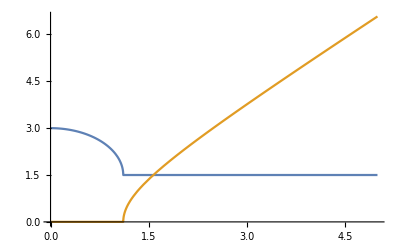

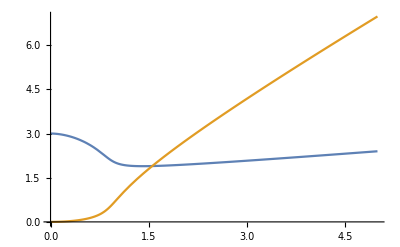

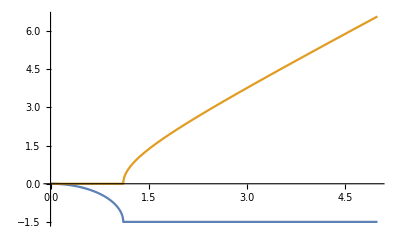

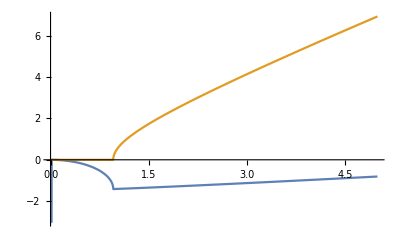

```mathematica
Plot[{Re[ktappx[ωt,10^-3]],-Im[ktappx[ωt,10^-3]]},{ωt,0,5}]
Plot[{Re[kt[ωt,10^-3]],-Im[kt[ωt,10^-3]]},{ωt,0,5}]
Plot[{Re[ktappx[ωt,-10^-3]],-Im[ktappx[ωt,-10^-3]]},{ωt,0,5}]
Plot[{Re[kt[ωt,-10^-3]],-Im[kt[ωt,-10^-3]]},{ωt,0,5}]
```

```mathematica
Manipulate[Plot[Im[10^Logdp*χ[q*10^(Logdp/2),ωt*10^Logdp,0.1*10^Logdp,s*10^Logdp]],{ωt,0,10},ImageSize->Large,PlotRange->{-0.05,1}],{{q,0.5},0,3},{{Logdp,-2},-10,-1},{{s,1},-1,1,2}]
```

```mathematica
qlist={0.02,0.05,0.1,1};
colors={Red,Gray,RGBColor[0,0.5,1],Blue};
stl[n_,thick_]:=Thread[{colors[[;;n]],AbsoluteThickness@thick}];
legend=LineLegend[Directive@@@stl[4,7],{MaTeX["q=0.02",Magnification->2.5],MaTeX["q=0.05",Magnification->2.5],MaTeX["q=0.1",Magnification->2.5],MaTeX["q=1.0",Magnification->2.5]},LegendFunction->Panel];
ticks={{{{0,MaTeX["",Magnification->3.5],{0.03,0}},{0.5,MaTeX["",Magnification->3.5],{0.03,0}},{0.85,Rotate[MaTeX["-\chi''/\chi''_{0}",Magnification->3.5],π/2],{0,0}},{1,Rotate[MaTeX["",Magnification->3.5],π/2],{0.03,0}},{1.5,MaTeX["",Magnification->3.5],{0.03,0}},{2,MaTeX["",Magnification->3.5],{0.03,0}},{3,MaTeX["3",Magnification->3.5],{0.03,0}},{4,MaTeX["4",Magnification->3.5],{0.03,0}}},None},{{{0*7.1/5.1,MaTeX["0",Magnification->3.5],{0.03,0}},{1*7.1/5.1,MaTeX["1",Magnification->3.5],{0.03,0}},{2*7.1/5.1,MaTeX["",Magnification->3.5],{0.03,0}},{2.5*7.1/5.1,MaTeX["\omega/\overline{\omega}_{\star}",Magnification->3.5],{0,0}},
{3*7.1/5.1,MaTeX["",Magnification->3.5],{0.03,0}},{4*7.1/5.1,MaTeX["4",Magnification->3.5],{0.03,0}},{5*7.1/5.1,MaTeX["5",Magnification->3.5],{0.03,0}}},None}};
```

```mathematica
axisbreak = {Polygon[{{0.45,-0.1},{0.65,0.1},{0.75,0.1},{0.55,-0.1}}[[{1,2,3,4}]],VertexColors->{RGBColor[1,1,1,1],RGBColor[1,1,1,1],RGBColor[1,1,1,1],RGBColor[1,1,1,1]}],{Thick,Black,Line[{{0.45,-0.1},{0.65,0.1}}]},{Thick,Black,Line[{{0.55,-0.1},{0.75,0.1}}]}};
```

```mathematica
image1=Plot[ImχAvg[qlist[[1]],ωt*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170,{ωt,0.7,7.1},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,PlotStyle->{colors[[1]],Thickness[0.0085]},Epilog->axisbreak];
```

```mathematica
image2=Plot[ImχAvg[qlist[[2]],ωt*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170,{ωt,0.7,7.1},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,PlotStyle->{colors[[2]],Thickness[0.0085]},Epilog->axisbreak];
```

```mathematica
image3=Plot[ImχAvg[qlist[[3]],ωt*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170,{ωt,0.7,7.1},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,PlotStyle->{colors[[3]],Thickness[0.0085]},Epilog->axisbreak];
```

```mathematica
image4=Plot[ImχAvg[qlist[[4]],ωt*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170,{ωt,0.7,7.1},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,PlotStyle->{colors[[4]],Thickness[0.0085]},Epilog->axisbreak];
```

```mathematica
image1b=Plot[ImχAvg[qlist[[1]],ωt*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170,{ωt,0.5,0.7},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,ColorFunction->(Opacity[(#-0.5)/(0.7-0.5),colors[[1]]]&),PlotStyle->Thickness[0.0085],Epilog->axisbreak];
```

```mathematica
image2b=Plot[ImχAvg[qlist[[2]],ωt*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170,{ωt,0.5,0.7},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,ColorFunction->(Opacity[(#-0.5)/(0.7-0.5),colors[[2]]]&),PlotStyle->Thickness[0.0085],Epilog->axisbreak];
```

```mathematica
image3b=Plot[ImχAvg[qlist[[3]],ωt*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170,{ωt,0.5,0.7},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,ColorFunction->(Opacity[(#-0.5)/(0.7-0.5),colors[[3]]]&),PlotStyle->Thickness[0.0085],Epilog->axisbreak];
```

```mathematica
image4b=Plot[ImχAvg[qlist[[4]],ωt*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170,{ωt,0.5,0.7},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,ColorFunction->(Opacity[(#-0.5)/(0.7-0.5),colors[[4]]]&),PlotStyle->Thickness[0.0085],Epilog->axisbreak];
```

```mathematica
imagenoavg=Plot[Im[χ[qlist[[4]],ωt*10^-3,10^-4,1.1*10^-3]]/170,{ωt,0,7.1},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,PlotStyle->{colors[[4]],Dashing[Large],Thickness[0.0085]},Epilog->axisbreak];
```

```mathematica
region =Graphics[{Polygon[{{-0.1,-0.1},{-0.1,2.2},{0.75,2.2},{0.75,-0.1}}[[{1,2,3,4}]],VertexColors->{RGBColor[0,0,0,0.7],RGBColor[0,0,0,0.7],RGBColor[0,0,0,0],RGBColor[0,0,0,0]}]}] ;
```

```mathematica
figured=Show[Legended[{imagenoavg,image1,image1b,image2,image2b,image3,image3b,image4,image4b},Placed[legend,{0.82,0.755}]],AspectRatio->1,frameStyle["","",50],ImageSize->Large,FrameTicks->ticks,FrameTicksStyle->{{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},{{Black,Thickness[0.005]},{Black,Thickness[0.005]}}},ImagePadding->{{60,15},{55,15}}]
```

```mathematica
qlist={0.02,0.05,0.1,1};
colors={Red,Gray,RGBColor[0,0.5,1],Blue};
stl[n_,thick_]:=Thread[{colors[[;;n]],AbsoluteThickness@thick}];
legend=LineLegend[Directive@@@stl[4,7],{MaTeX["q=0.02",Magnification->2.5],MaTeX["q=0.05",Magnification->2.5],MaTeX["q=0.1",Magnification->2.5],MaTeX["q=1.0",Magnification->2.5]},LegendFunction->Panel];
ticks={{{{0,MaTeX["",Magnification->3.5],{0.03,0}},{0.5,MaTeX["",Magnification->3.5],{0.03,0}},{0.85,Rotate[MaTeX["-\chi''/\chi''_{0}",Magnification->3.5],π/2],{0,0}},{1,Rotate[MaTeX["",Magnification->3.5],π/2],{0.03,0}},{1.5,MaTeX["",Magnification->3.5],{0.03,0}},{2,MaTeX["",Magnification->3.5],{0.03,0}},{3,MaTeX["3",Magnification->3.5],{0.03,0}},{4,MaTeX["4",Magnification->3.5],{0.03,0}}},None},{{{0*7.1/5.1,MaTeX["0",Magnification->3.5],{0.03,0}},{1*7.1/5.1,MaTeX["1",Magnification->3.5],{0.03,0}},{2*7.1/5.1,MaTeX["",Magnification->3.5],{0.03,0}},{2.5*7.1/5.1,MaTeX["\omega/\overline{\omega}_{\star}",Magnification->3.5],{0,0}},
{3*7.1/5.1,MaTeX["",Magnification->3.5],{0.03,0}},{4*7.1/5.1,MaTeX["4",Magnification->3.5],{0.03,0}},{5*7.1/5.1,MaTeX["5",Magnification->3.5],{0.03,0}}},None}};
```

```mathematica
axisbreak = {Polygon[{{0.45,-0.1},{0.65,0.1},{0.75,0.1},{0.55,-0.1}}[[{1,2,3,4}]],VertexColors->{RGBColor[1,1,1,1],RGBColor[1,1,1,1],RGBColor[1,1,1,1],RGBColor[1,1,1,1]}],{Thick,Black,Line[{{0.45,-0.1},{0.65,0.1}}]},{Thick,Black,Line[{{0.55,-0.1},{0.75,0.1}}]}};
```

```mathematica
image1=Plot[ImχAvg[qlist[[1]],ωt*10^-3,10^-4,1.6*10^-3,0.9*10^-3,3.5]/170,{ωt,0.7,7.1},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,PlotStyle->{colors[[1]],Thickness[0.0085]},Epilog->axisbreak];
```

```mathematica
image2=Plot[ImχAvg[qlist[[2]],ωt*10^-3,10^-4,1.6*10^-3,0.9*10^-3,3.5]/170,{ωt,0.7,7.1},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,PlotStyle->{colors[[2]],Thickness[0.0085]},Epilog->axisbreak];
```

```mathematica
image3=Plot[ImχAvg[qlist[[3]],ωt*10^-3,10^-4,1.6*10^-3,0.9*10^-3,3.5]/170,{ωt,0.7,7.1},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,PlotStyle->{colors[[3]],Thickness[0.0085]},Epilog->axisbreak];
```

```mathematica
image4=Plot[ImχAvg[qlist[[4]],ωt*10^-3,10^-4,1.6*10^-3,0.9*10^-3,3.5]/170,{ωt,0.7,7.1},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,PlotStyle->{colors[[4]],Thickness[0.0085]},Epilog->axisbreak];
```

```mathematica
image1b=Plot[ImχAvg[qlist[[1]],ωt*10^-3,10^-4,1.6*10^-3,0.9*10^-3,3.5]/170,{ωt,0.5,0.7},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,ColorFunction->(Opacity[(#-0.5)/(0.7-0.5),colors[[1]]]&),PlotStyle->Thickness[0.0085],Epilog->axisbreak];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
image2b=Plot[ImχAvg[qlist[[2]],ωt*10^-3,10^-4,1.6*10^-3,0.9*10^-3,3.5]/170,{ωt,0.5,0.7},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,ColorFunction->(Opacity[(#-0.5)/(0.7-0.5),colors[[2]]]&),PlotStyle->Thickness[0.0085],Epilog->axisbreak];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
image3b=Plot[ImχAvg[qlist[[3]],ωt*10^-3,10^-4,1.6*10^-3,0.9*10^-3,3.5]/170,{ωt,0.5,0.7},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,ColorFunction->(Opacity[(#-0.5)/(0.7-0.5),colors[[3]]]&),PlotStyle->Thickness[0.0085],Epilog->axisbreak];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
image4b=Plot[ImχAvg[qlist[[4]],ωt*10^-3,10^-4,1.6*10^-3,0.9*10^-3,3.5]/170,{ωt,0.5,0.7},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,ColorFunction->(Opacity[(#-0.5)/(0.7-0.5),colors[[4]]]&),PlotStyle->Thickness[0.0085],Epilog->axisbreak];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
imagenoavg=Plot[Im[χ[qlist[[4]],ωt*10^-3,10^-4,1.6*10^-3]]/170,{ωt,0,7.1},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,PlotStyle->{colors[[4]],Dashing[Large],Thickness[0.0085]},Epilog->axisbreak];
```

```mathematica
region =Graphics[{Polygon[{{-0.1,-0.1},{-0.1,2.2},{0.75,2.2},{0.75,-0.1}}[[{1,2,3,4}]],VertexColors->{RGBColor[0,0,0,0.7],RGBColor[0,0,0,0.7],RGBColor[0,0,0,0],RGBColor[0,0,0,0]}]}] ;
```

```mathematica
figuree=Show[Legended[{imagenoavg,image1,image1b,image2,image2b,image3,image3b,image4,image4b},Placed[legend,{0.82,0.755}]],AspectRatio->1,frameStyle["","",50],ImageSize->Large,FrameTicks->ticks,FrameTicksStyle->{{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},{{Black,Thickness[0.005]},{Black,Thickness[0.005]}}},ImagePadding->{{60,15},{55,15}}]
```

## OPData below this line

```mathematica
ωsq005={0.002,0.008,0.014,0.02,0.026,0.03191,0.038,0.044,0.04993,0.056,0.06192,0.068,0.07391,0.08,0.086,0.092,0.098,0.104,0.11,0.116,0.12194,0.128,0.13393,0.14,0.14592,0.152,0.15791,0.164,0.17,0.176,0.182,0.188,0.194,0.2,0.20594,0.212,0.21793,0.224,0.22992,0.236,0.24191,0.248,0.254,0.26,0.266,0.272,0.278,0.284,0.29,0.296,0.30193,0.308,0.31392,0.32,0.32591,0.33194,0.338,0.344,0.35,0.35592,0.362,0.36791,0.374,0.38,0.386,0.392,0.398,0.404,0.41,0.41593,0.422,0.42793,0.434,0.43992,0.446,0.452,0.458,0.464,0.47,0.476,0.482,0.488,0.494,0.49993,0.506,0.51192,0.518,0.52392,0.53,0.536,0.542,0.548,0.554,0.56,0.566,0.572,0.578,0.58393,0.59,0.59592,0.602,0.60791,0.614,0.62,0.62593,0.632,0.638,0.644,0.65,0.656,0.662,0.668,0.674,0.68,0.686,0.692,0.698,0.704,0.70993,0.716,0.72192,0.727915,0.73391,0.74,0.746,0.752,0.758,0.764,0.77,0.776,0.78194,0.788,0.79393,0.8,0.80592,0.812,0.81791,0.824,0.83,0.836,0.842,0.848,0.854,0.86,0.86594,0.872,0.87793,0.884,0.88992,0.896,0.90191,0.908,0.914,0.92,0.926,0.932,0.938,0.944,0.95,0.956,0.962,0.968,0.974,0.98,0.986,0.99194,0.998,1.00393,1.01,1.01592,1.022,1.02791,1.034,1.04,1.046,1.052,1.058,1.064,1.07,1.07593,1.082,1.08793,1.094,1.09992,1.106,1.112,1.118,1.124,1.13,1.136,1.142,1.148,1.154,1.15993,1.166,1.17192,1.178,1.18392,1.19,1.196,1.202,1.208,1.214,1.22,1.226,1.232,1.238,1.244,1.25,1.25592,1.262,1.26791,1.274,1.28,1.28593,1.292,1.29792,1.304,1.30991,1.316,1.322,1.328,1.334,1.34,1.346,1.352,1.358,1.364,1.36993,1.376,1.38192,1.388,1.39391,1.4,1.406,1.412,1.418,1.424,1.43,1.436,1.44194,1.448,1.45393,1.46,1.46592,1.472,1.47791,1.484,1.49,1.496,1.502,1.508,1.514,1.52,1.52594,1.532,1.53793,1.544,1.54992,1.556,1.56191,1.56794,1.574,1.57993,1.586,1.592,1.598,1.604,1.61,1.616,1.622,1.628,1.634,1.64,1.646,1.65194,1.658,1.66393,1.67,1.67592,1.682,1.68791,1.694,1.7,1.706,1.712,1.718,1.724,1.73,1.73593,1.742,1.74793,1.754,1.75992,1.766,1.772,1.778,1.784,1.79,1.796,1.802,1.808,1.814,1.81993,1.826,1.83192,1.838,1.84392,1.85,1.856,1.862,1.868,1.874,1.88,1.886,1.892,1.898,1.904,1.91,1.916,1.922,1.928,1.934,1.94,1.94593,1.952,1.95792,1.964,1.96991,1.976,1.982,1.988,1.994,2};
χppq005={-0.000074680891,0.00010416474,0.000053409254,0.000009125605,-0.000010113221,-0.000014530598,-0.000017054726,-0.000018993423,-0.000019651928,-0.000018072318,-0.000017972091,-0.000018158846,-0.000020680926,-0.000020818548,-0.000015717798,-0.000011388134,-0.000009919864,-0.000008730328,-0.000008322203,-0.000008277767,-0.000008530222,-0.000007398246,-0.000007916911,-0.000007708965,-0.000007260111,-0.000007525432,-0.000006897169,-0.000007577153,-0.000006709477,-0.000006456516,-0.000007041725,-0.000007116347,-0.000006530599,-0.000006524706,-0.000007120449,-0.000006903295,-0.000007129541,-0.00000606209,-0.000006294004,-0.000006975186,-0.000006893345,-0.000007287393,-0.000007441937,-0.000007583741,-0.00000773706,-0.000007394681,-0.000007008406,-0.000007009927,-0.000007075823,-0.000007464186,-0.00000712943,-0.000007602724,-0.000008568329,-0.00000688201,-0.000007309795,-0.000007639495,-0.000007703678,-0.000007846399,-0.000007948383,-0.000007881877,-0.000007550587,-0.000008258359,-0.000007961871,-0.000007775582,-0.000008094168,-0.000008065781,-0.000008026581,-0.000007775477,-0.000008232726,-0.000008019282,-0.000007856434,-0.000007860432,-0.000008086068,-0.000008727067,-0.000008878398,-0.000008233105,-0.000008224055,-0.000008374515,-0.000008724058,-0.000009432445,-0.000009308731,-0.000008686471,-0.00000919216,-0.000009010413,-0.000009779419,-0.000009475184,-0.000009780526,-0.000009303372,-0.00000877143,-0.000009326165,-0.000009399165,-0.000009885397,-0.000008833067,-0.000010273016,-0.000009525617,-0.000009106082,-0.000008744517,-0.000009273211,-0.000008596787,-0.000009715249,-0.00000899531,-0.00001017461,-0.000010558964,-0.000009435627,-0.000009596656,-0.000009402618,-0.0000098069,-0.000009724978,-0.000010821441,-0.000009788985,-0.000010637834,-0.000009797935,-0.00001057292,-0.000009793961,-0.000009767935,-0.000010659083,-0.000010946106,-0.000012619232,-0.000011333599,-0.000010957891,-0.000011726378,-0.00001189396,-0.000011130125,-0.000010486963,-0.000009842107,-0.000010797391,-0.000010686544,-0.000010304224,-0.000010592595,-0.000011723744,-0.000011883086,-0.000010459706,-0.000010448164,-0.000010646077,-0.000011080784,-0.000011000733,-0.000010576362,-0.000010106217,-0.000011490721,-0.000011572848,-0.000011341862,-0.000011498278,-0.000011236485,-0.000011924406,-0.000011134645,-0.000011114176,-0.000010659775,-0.000011953446,-0.000010320306,-0.000012140622,-0.000010602233,-0.000011578889,-0.000010890783,-0.000010216612,-0.000010761012,-0.000011397536,-0.000011926238,-0.000010757089,-0.000010631416,-0.000010305093,-0.0000112758,-0.000010823159,-0.000011080805,-0.000011533547,-0.000011190589,-0.000010113205,-0.00001245878,-0.000011221728,-0.000010843043,-0.000010310553,-0.000011089197,-0.000010291222,-0.000011296349,-0.0000107621,-0.000010319311,-0.000010252787,-0.000010394541,-0.000010061722,-0.000010385184,-0.000009866836,-0.000008449984,-0.000009699774,-0.00001093625,-0.000009572061,-0.00001018556,-0.000010654677,-0.000009960843,-0.00001014553,-0.000010350576,-0.000010448236,-0.000009352242,-0.000009454238,-0.000008914775,-0.000008120646,-0.0000084501,-0.000008968601,-0.000008919326,-0.00000895317,-0.000008541211,-0.000008899479,-0.000008344352,-0.000008730496,-0.000009975263,-0.000008163752,-0.000007483085,-0.000009826294,-0.000007773091,-0.000007113088,-0.000008007426,-0.00000863157,-0.000008231726,-0.000008561302,-0.00000802476,-0.000008795911,-0.000008063445,-0.000007451888,-0.000006831831,-0.000008710798,-0.000007016366,-0.000007235996,-0.000007911902,-0.000007044563,-0.000006990299,-0.000006056134,-0.000007262124,-0.000007110893,-0.000007541937,-0.000007529551,-0.000006789699,-0.000007184744,-0.000008228617,-0.000005533803,-0.000006853973,-0.000006066982,-0.000007943988,-0.000006168245,-0.000006519709,-0.000004676069,-0.000005942426,-0.000006751516,-0.000006574544,-0.00000648719,-0.000006005094,-0.000005168592,-0.000005817097,-0.00000651213,-0.000006950798,-0.000006773873,-0.000005954569,-0.0000072469,-0.000006545771,-0.000006178356,-0.000005940235,-0.000006259062,-0.000004627991,-0.000005874323,-0.000006342528,-0.000006872381,-0.000006606106,-0.000006867492,-0.0000055503,-0.000005361549,-0.000005617721,-0.000005439697,-0.000005720091,-0.000006597099,-0.000004535868,-0.000006521391,-0.000004995332,-0.000004766136,-0.000006072888,-0.000005035833,-0.000005931058,-0.000004496361,-0.000005571727,-0.000005048782,-0.000005445674,-0.000005026385,-0.000005099735,-0.000005665294,-0.000004894659,-0.000005188317,-0.000004877723,-0.000005849686,-0.000006138332,-0.000005588135,-0.000005588627,-0.000006904216,-0.000005203085,-0.000006032674,-0.000005692868,-0.000005305067,-0.000005572577,-0.000003928734,-0.00000440397,-0.000006183059,-0.000005572836,-0.000006072751,-0.000005350292,-0.000005796284,-0.000005427724,-0.000005637334,-0.000007346413,-0.000003507241,-0.000004787382,-0.000004436397,-0.000004839739,-0.000003899713,-0.000004319686,-0.000003922052,-0.000003669593,-0.000005205025,-0.000005405724,-0.000005817081,-0.000005751054,-0.000004443893,-0.000004618677,-0.000004927533,-0.000004440127,-0.000005225297,-0.000004519926,-0.000003125689,-0.000006082786,-0.000004427847,-0.000003397293,-0.000004133925,-0.000003569192,-0.000005272665,-0.000003729709,-0.000005531818,-0.000005081537,-0.000003280939,-0.00000368429,0
};
χppq005err={0.000004046417,0.000002769523,0.000001883651,0.000001397752,0.000001146408,0.000000982854,0.00000087192,0.000000797759,0.000000742307,0.000000676444,0.00000063175,0.000000607214,0.000000627812,0.000000619344,0.000000540738,0.000000461086,0.000000429495,0.000000400979,0.00000038789,0.00000038553,0.000000392128,0.000000369483,0.000000380305,0.000000377146,0.000000369276,0.000000374815,0.000000357309,0.000000374105,0.000000353925,0.000000349358,0.000000366208,0.000000369038,0.000000355015,0.000000355337,0.000000374397,0.000000368736,0.000000376804,0.000000350694,0.00000035767,0.000000376719,0.000000375868,0.000000388433,0.000000393537,0.000000399519,0.000000405503,0.000000399508,0.000000389711,0.000000389589,0.000000394481,0.000000406917,0.000000397548,0.000000414213,0.000000441265,0.000000396756,0.000000411797,0.000000422005,0.000000425459,0.000000432052,0.000000435757,0.00000043517,0.000000428984,0.000000448518,0.000000443532,0.000000439295,0.000000449777,0.000000450259,0.000000452826,0.000000446507,0.000000461878,0.000000456276,0.000000453176,0.000000455557,0.000000462438,0.000000484728,0.000000490671,0.000000475841,0.000000476341,0.000000482587,0.00000049378,0.000000515024,0.000000514846,0.000000496269,0.000000514063,0.000000512669,0.000000534597,0.000000529246,0.000000541206,0.000000528299,0.000000514057,0.000000530614,0.000000538139,0.000000554751,0.000000525953,0.000000566463,0.00000054665,0.000000538795,0.000000529722,0.000000546793,0.000000528953,0.000000564511,0.000000542846,0.00000058272,0.00000059627,0.000000566412,0.000000572683,0.000000569838,0.000000583,0.000000582235,0.000000615325,0.000000590582,0.000000616716,0.000000593598,0.000000621305,0.000000600688,0.000000600859,0.000000628661,0.00000063854,0.000000690454,0.000000653732,0.000000646395,0.000000668257,0.000000677258,0.000000660242,0.000000641134,0.000000624539,0.000000656184,0.000000654752,0.000000642409,0.000000656392,0.000000693882,0.000000699704,0.000000660251,0.000000664293,0.000000672638,0.000000684834,0.000000687017,0.000000679187,0.000000664058,0.000000708586,0.000000713844,0.000000709722,0.000000716177,0.000000712636,0.000000734415,0.000000712604,0.000000714518,0.000000704455,0.000000749136,0.000000698438,0.000000760004,0.000000712418,0.000000745513,0.000000726608,0.000000706326,0.000000727052,0.000000749591,0.000000771675,0.000000735251,0.000000735366,0.000000726451,0.000000759711,0.000000745403,0.000000758277,0.000000775453,0.000000770535,0.000000730882,0.000000812204,0.000000774129,0.000000766968,0.000000750048,0.000000780707,0.000000758233,0.000000791117,0.000000776111,0.000000763062,0.000000763363,0.000000774542,0.000000761914,0.000000775717,0.000000757886,0.000000704093,0.000000757538,0.000000808525,0.00000075991,0.000000785086,0.000000805472,0.000000784838,0.000000796192,0.000000801099,0.000000809094,0.000000766761,0.000000775377,0.000000749368,0.000000727414,0.000000738783,0.000000760699,0.000000764279,0.000000769959,0.000000753027,0.000000772468,0.000000750408,0.000000769769,0.000000824181,0.000000746931,0.000000718952,0.000000828632,0.000000736633,0.000000708884,0.000000749201,0.000000786183,0.000000773036,0.000000789805,0.000000762516,0.000000801145,0.000000763649,0.000000744639,0.000000711212,0.000000804908,0.00000073246,0.000000739171,0.000000778089,0.000000738772,0.00000074092,0.000000687825,0.000000754465,0.00000075359,0.000000778219,0.000000775733,0.000000738016,0.000000764251,0.000000816134,0.00000067716,0.000000752558,0.000000713409,0.000000817085,0.00000072658,0.00000074158,0.00000062699,0.000000713997,0.000000765149,0.000000762519,0.000000744487,0.000000723537,0.000000678892,0.000000720669,0.00000076516,0.000000788188,0.00000078697,0.000000740514,0.00000082252,0.000000777663,0.00000076068,0.000000743577,0.000000764722,0.000000664148,0.000000739721,0.000000780211,0.000000819365,0.000000800237,0.000000823243,0.000000730763,0.000000729922,0.000000754648,0.000000746287,0.000000756943,0.000000822428,0.000000681572,0.000000820932,0.000000722028,0.000000702003,0.000000804519,0.000000725048,0.00000079281,0.000000697471,0.000000772049,0.000000741933,0.000000773821,0.000000737963,0.000000755839,0.000000794745,0.000000741173,0.000000759591,0.000000742547,0.000000819727,0.00000084067,0.000000800779,0.000000813427,0.000000901325,0.000000779995,0.000000848951,0.000000821139,0.000000797041,0.000000810713,0.00000069065,0.000000735266,0.000000875258,0.000000817515,0.000000873255,0.000000819316,0.000000848565,0.000000819742,0.000000843623,0.000000960971,0.00000066404,0.000000783046,0.000000760552,0.00000080349,0.000000720557,0.000000750533,0.000000718759,0.000000701954,0.000000830847,0.000000851588,0.000000887137,0.000000889506,0.000000772419,0.000000794902,0.00000082479,0.000000787951,0.000000850461,0.000000791408,0.000000667776,0.000000928077,0.000000800425,0.000000704391,0.000000774823,0.000000731779,0.000000879817,0.000000736979,0.000000910025,0.000000869375,0.000000709271,0.000000746606,0
};
ωsq010={0.002,0.008,0.014,0.02,0.026,0.03191,0.038,0.044,0.04993,0.056,0.06192,0.068,0.07391,0.08,0.086,0.092,0.098,0.104,0.11,0.11597,0.12194,0.128,0.13393,0.14,0.14592,0.152,0.15791,0.164,0.17,0.176,0.182,0.188,0.194,0.2,0.20594,0.212,0.21793,0.224,0.22992,0.236,0.24191,0.248,0.254,0.26,0.266,0.272,0.278,0.284,0.29,0.296,0.30193,0.308,0.31392,0.32,0.32591,0.33194,0.338,0.34393,0.35,0.35592,0.362,0.36791,0.374,0.38,0.386,0.392,0.398,0.404,0.41,0.41593,0.422,0.42793,0.434,0.43992,0.446,0.452,0.458,0.464,0.47,0.476,0.482,0.488,0.494,0.5,0.506,0.51192,0.518,0.52392,0.53,0.536,0.542,0.548,0.554,0.56,0.566,0.572,0.578,0.58393,0.59,0.59592,0.602,0.60791,0.614,0.62,0.62593,0.632,0.638,0.644,0.65,0.656,0.662,0.668,0.674,0.68,0.686,0.692,0.698,0.704,0.70993,0.716,0.72192,0.728,0.73391,0.74,0.746,0.752,0.758,0.764,0.77,0.776,0.78194,0.788,0.79393,0.8,0.80592,0.812,0.81791,0.824,0.83,0.836,0.842,0.848,0.854,0.86,0.86594,0.872,0.87793,0.883925,0.88992,0.896,0.90191,0.908,0.914,0.92,0.926,0.932,0.938,0.944,0.95,0.956,0.962,0.968,0.974,0.98,0.986,0.99194,0.998,1.00393,1.01,1.01592,1.022,1.02791,1.034,1.04,1.046,1.052,1.058,1.064,1.07,1.07593,1.082,1.08793,1.094,1.09992,1.106,1.112,1.118,1.124,1.13,1.136,1.142,1.148,1.154,1.15993,1.166,1.17192,1.178,1.18392,1.19,1.196,1.202,1.208,1.214,1.22,1.226,1.232,1.238,1.244,1.25,1.25592,1.262,1.268,1.274,1.28,1.28593,1.292,1.29792,1.304,1.30991,1.316,1.322,1.328,1.334,1.34,1.346,1.352,1.358,1.364,1.36993,1.376,1.38192,1.388,1.39391,1.4,1.406,1.412,1.418,1.424,1.43,1.436,1.44194,1.448,1.45393,1.46,1.46592,1.472,1.47791,1.484,1.49,1.496,1.502,1.508,1.514,1.52,1.52594,1.532,1.53793,1.544,1.54992,1.556,1.56191,1.56794,1.574,1.57993,1.586,1.592,1.598,1.604,1.61,1.616,1.622,1.628,1.634,1.64,1.646,1.652,1.658,1.66393,1.67,1.67592,1.682,1.68791,1.694,1.7,1.706,1.712,1.718,1.724,1.73,1.73593,1.742,1.74793,1.754,1.75992,1.766,1.772,1.778,1.784,1.79,1.796,1.802,1.808,1.814,1.81993,1.826,1.83192,1.838,1.84392,1.85,1.856,1.862,1.868,1.874,1.88,1.886,1.892,1.898,1.904,1.91,1.916,1.922,1.928,1.934,1.94,1.94593,1.952,1.95792,1.964,1.96991,1.976,1.982,1.988,1.994,2
};
χppq010={-0.000046829112,0.000108813564,0.000058187766,-0.000059300696,-0.00012614761,-0.000144170703,-0.000168430981,-0.000165852432,-0.000163363159,-0.000165312005,-0.000169433233,-0.00016087231,-0.000156822593,-0.000134378126,-0.000108222992,-0.000086076328,-0.000070803118,-0.000061190828,-0.000055814082,-0.000057456339,-0.000054182854,-0.000051869749,-0.000046126652,-0.000044904413,-0.000044588836,-0.000044190748,-0.000042170128,-0.000044928753,-0.000038786315,-0.000041654803,-0.000046382288,-0.000044911928,-0.00003850216,-0.000040801021,-0.000040470932,-0.000039806967,-0.000039391048,-0.000037545467,-0.000036382279,-0.000036621615,-0.00003667497,-0.000033294086,-0.000040178785,-0.000041028673,-0.00003944113,-0.00003954396,-0.000038373183,-0.000036609722,-0.000036985458,-0.000039877569,-0.00003518946,-0.000040938771,-0.000040016914,-0.000039264117,-0.000041171352,-0.000039746862,-0.000039835536,-0.000039257242,-0.000036880794,-0.000035377877,-0.000039423574,-0.000041923251,-0.000041291047,-0.000041104178,-0.000040667489,-0.00004074095,-0.000039181389,-0.000043153606,-0.000040356121,-0.000039151159,-0.000040864241,-0.000046390723,-0.000047334852,-0.000042752328,-0.000047782264,-0.000044098607,-0.000046233048,-0.00004448338,-0.000044114853,-0.00004136889,-0.000048444193,-0.000045421375,-0.000046584625,-0.00004194361,-0.000040690701,-0.000044252782,-0.000042294162,-0.000047719311,-0.000043723781,-0.00004498431,-0.000040660973,-0.000042020638,-0.000044125472,-0.00003826904,-0.000034341318,-0.00004131487,-0.000049142815,-0.000040983187,-0.000046508828,-0.000046970885,-0.000042275897,-0.000045670548,-0.00004117788,-0.000040771347,-0.000046426881,-0.000045131544,-0.000046803164,-0.000042888456,-0.000041034578,-0.00004759276,-0.000043932798,-0.000043875579,-0.000040334469,-0.000039532812,-0.000041487781,-0.000039993489,-0.000043061192,-0.000041580941,-0.000042766173,-0.000041769906,-0.000040454662,-0.000043888763,-0.000041208313,-0.000042525574,-0.000039086965,-0.000041634616,-0.000046494447,-0.000050154319,-0.000042688236,-0.000049534961,-0.000046782351,-0.000044907642,-0.000046386837,-0.000042818847,-0.000042730462,-0.000046588749,-0.00004251992,-0.000041070344,-0.000047968031,-0.000048932246,-0.000053691081,-0.000048797045,-0.000044488723,-0.000042972136,-0.000044757866,-0.000038842159,-0.000044729418,-0.000049159407,-0.000045240908,-0.000042081087,-0.000045416523,-0.000041136821,-0.000048380508,-0.000041504475,-0.000041579742,-0.000038244446,-0.000049304702,-0.000041890157,-0.000044082947,-0.000047662574,-0.000050292747,-0.000051015556,-0.000042613036,-0.000037278174,-0.000038865536,-0.000044674644,-0.000047328622,-0.000042679525,-0.000044460418,-0.000044445785,-0.000043740659,-0.000039740328,-0.000030831427,-0.000045452037,-0.000039556325,-0.000034722596,-0.000038596966,-0.000038222785,-0.000036209805,-0.000037736829,-0.000036836749,-0.0000389232,-0.000045485899,-0.000042947605,-0.000040501387,-0.000036780376,-0.000041320642,-0.000044184685,-0.000042614534,-0.000039428511,-0.000040319438,-0.000034931805,-0.000034826578,-0.000032301765,-0.000033674922,-0.000033210767,-0.000036977346,-0.000029231494,-0.000037206628,-0.000046104474,-0.000036440286,-0.000035192511,-0.000035040773,-0.000038103005,-0.000027691533,-0.000031609578,-0.000032901827,-0.000032055194,-0.000030265315,-0.000029528633,-0.000033920461,-0.000032822158,-0.000031282603,-0.000027672981,-0.000031419922,-0.000026707235,-0.000028362,-0.000022937192,-0.000031861326,-0.000031448222,-0.000026473568,-0.000025503799,-0.000026720466,-0.000028266605,-0.000029319086,-0.000028091512,-0.000025745761,-0.000030253516,-0.000031205308,-0.000032018258,-0.000029352036,-0.000024754448,-0.000025005614,-0.000022504301,-0.000027787653,-0.000024134323,-0.000021227833,-0.000017471387,-0.000020503408,-0.000026778633,-0.000029758995,-0.000025977317,-0.000027221027,-0.000026338852,-0.00002524003,-0.000024027658,-0.000018193166,-0.000026094887,-0.000028931934,-0.000021539881,-0.000024901525,-0.000018429901,-0.000020112443,-0.000023593491,-0.000022089394,-0.000018336878,-0.000017161216,-0.000021140693,-0.000026713995,-0.000022833391,-0.000020244405,-0.000020102939,-0.000018874837,-0.000022829756,-0.000026113359,-0.000018681161,-0.000020710153,-0.000022831463,-0.000022004181,-0.000019707005,-0.000022689406,-0.00002177508,-0.000020704626,-0.000023950845,-0.000020309779,-0.000019933488,-0.000022635701,-0.000023368691,-0.000022661771,-0.000022489145,-0.000019618415,-0.000018978335,-0.000018954762,-0.00001805055,-0.00001564359,-0.00001585133,-0.000021235595,-0.000015279015,-0.000017597106,-0.000021585213,-0.000021655717,-0.000017282576,-0.000017816477,-0.000015437046,-0.000016115523,-0.000018225128,-0.000016562399,-0.000013794553,-0.000017957049,-0.000020659677,-0.000019919303,-0.000016033328,-0.000019265163,-0.000019295054,-0.000016946691,-0.000014826684,-0.000020189035,-0.000014069421,-0.00002413012,-0.000017240689,-0.000015282923,-0.000017998126,-0.000024478651,-0.000016362954,-0.000015428412,-0.000015869438,-0.000015036,-0.000014450638,-0.000015167059,-0.000012181792,-0.000011974275,-0.000016813536,-0.000021168834,-0.000013901089,-0.000010918669,-0.000015277774,-0.000018534353,-0.000016138889,-0.000013882969,-0.000013310429,-0.000016086879,-0.000020634366,-0.000016912139,-0.000021886201
};
χppq010err={0.000027153631,0.00002362347,0.000019062357,0.000015383486,0.000012768917,0.000010832447,0.000009499314,0.000008493379,0.000007816583,0.000007357931,0.000006976396,0.000006628758,0.000006363608,0.000005835528,0.000005243818,0.000004652818,0.000004179693,0.000003872379,0.000003676028,0.000003721471,0.000003602953,0.000003521545,0.000003322506,0.000003282984,0.000003291846,0.000003277903,0.00000319929,0.00000329167,0.00000304994,0.000003197114,0.000003367024,0.000003312857,0.00000306726,0.000003166725,0.000003169948,0.000003150468,0.000003144737,0.000003065648,0.000003040381,0.000003056161,0.000003042071,0.000002911846,0.000003215304,0.000003245474,0.000003189785,0.00000321522,0.000003175781,0.000003094127,0.000003123843,0.000003235848,0.000003044956,0.000003310674,0.000003270557,0.000003251169,0.000003347951,0.000003287134,0.000003300944,0.000003272693,0.000003179229,0.000003118295,0.000003309694,0.000003403625,0.000003363964,0.000003382163,0.00000339325,0.000003406941,0.000003332498,0.000003495081,0.000003401869,0.000003348565,0.000003441357,0.00000366413,0.000003703523,0.000003537449,0.000003745281,0.00000359607,0.000003710211,0.000003624186,0.000003617296,0.000003509135,0.000003833061,0.000003715204,0.00000375909,0.000003566546,0.000003515267,0.000003691331,0.0000036002,0.000003821158,0.000003668078,0.000003720998,0.000003566536,0.000003618267,0.000003714723,0.000003479002,0.000003270026,0.000003613567,0.000003962997,0.00000361482,0.000003869694,0.000003890018,0.00000371623,0.000003862981,0.000003695739,0.000003666795,0.000003932509,0.0000038947,0.000003971966,0.000003760311,0.000003711148,0.000004013378,0.000003873011,0.000003847562,0.000003714898,0.000003683272,0.000003772219,0.000003705859,0.000003859253,0.000003794621,0.000003859549,0.000003820766,0.000003756921,0.000003920114,0.000003807183,0.000003906759,0.000003747698,0.000003849999,0.000004106241,0.000004282849,0.000003945117,0.0000042516,0.000004121713,0.000004049768,0.000004127731,0.000003986621,0.000003975107,0.000004174422,0.000003991786,0.000003935607,0.000004259621,0.000004322636,0.000004533544,0.000004279275,0.000004133258,0.000004056991,0.000004168952,0.000003869895,0.000004201545,0.000004372929,0.000004217153,0.000004074431,0.000004231525,0.000004027461,0.000004394805,0.000004074667,0.000004083618,0.000003909062,0.000004471564,0.000004157359,0.00000424182,0.000004428231,0.000004576983,0.000004599694,0.000004214354,0.000003958685,0.000004047058,0.000004326621,0.000004470835,0.000004208543,0.000004323738,0.000004366171,0.000004329248,0.000004146421,0.000003647307,0.000004454816,0.000004142054,0.000003864267,0.000004095179,0.000004087197,0.000003986678,0.000004119981,0.000004023198,0.000004181035,0.000004493492,0.000004350075,0.000004232913,0.000004062782,0.000004347788,0.000004502172,0.000004417114,0.000004270406,0.000004325963,0.000004056795,0.000004018394,0.000003874871,0.000003982024,0.000003953576,0.000004183799,0.000003719942,0.000004212409,0.000004742329,0.000004153108,0.000004110648,0.000004161024,0.000004309209,0.000003658054,0.000003916155,0.00000401585,0.000003961181,0.000003902409,0.000003867967,0.000004146895,0.000004051591,0.000003957991,0.000003746327,0.000004010195,0.000003680652,0.000003824791,0.000003454033,0.000004067342,0.000004007922,0.000003700978,0.00000363717,0.000003749281,0.000003867109,0.000003948103,0.000003872188,0.000003689077,0.000004027139,0.000004116222,0.000004149013,0.000003985728,0.000003677208,0.000003707772,0.000003452012,0.000003835526,0.000003619794,0.000003417549,0.000003129196,0.000003397611,0.000003887886,0.000004084712,0.000003853905,0.000003919328,0.000003904371,0.000003811599,0.000003658407,0.000003204379,0.000003885626,0.000004089748,0.000003526256,0.000003811173,0.000003258067,0.000003408049,0.000003712295,0.000003605432,0.000003270879,0.00000316773,0.000003513951,0.000004022704,0.000003721581,0.000003491394,0.000003482251,0.000003377804,0.000003715171,0.000003962586,0.00000337487,0.000003580055,0.000003785488,0.000003670645,0.000003491494,0.000003772372,0.000003716386,0.000003622947,0.000003904416,0.00000362036,0.000003555594,0.000003767337,0.000003879157,0.000003834622,0.000003797799,0.000003565577,0.00000348765,0.000003515249,0.000003441039,0.000003165217,0.000003200158,0.000003705173,0.000003163529,0.000003450708,0.000003855675,0.000003793265,0.000003399128,0.000003440509,0.000003228202,0.000003271619,0.00000350509,0.000003365307,0.000003043789,0.000003528448,0.000003768543,0.00000370116,0.000003300368,0.000003616042,0.000003664411,0.000003443114,0.00000323803,0.000003812983,0.000003135116,0.000004164342,0.00000349521,0.000003277684,0.000003586807,0.000004211639,0.000003390295,0.000003383556,0.000003393541,0.000003277235,0.000003258635,0.000003344208,0.000002955047,0.000002973081,0.000003546505,0.000003996158,0.000003232667,0.000002793694,0.000003444727,0.000003764469,0.000003545958,0.00000325364,0.000003177884,0.000003481517,0.000003990987,0.000003620125,0.000004132066
};
ωsq016={0.002,0.008,0.014,0.02,0.026,0.03191,0.038,0.044,0.04993,0.056,0.06192,0.068,0.07391,0.08,0.086,0.092,0.098,0.104,0.11,0.116,0.12194,0.128,0.13393,0.14,0.14592,0.152,0.15791,0.164,0.17,0.176,0.182,0.188,0.194,0.2,0.20594,0.212,0.21793,0.224,0.22992,0.236,0.24191,0.248,0.254,0.26,0.266,0.272,0.278,0.284,0.29,0.296,0.30193,0.308,0.31392,0.32,0.32591,0.33194,0.338,0.34393,0.349925,0.35592,0.362,0.36791,0.374,0.38,0.386,0.392,0.398,0.404,0.41,0.41593,0.422,0.42793,0.434,0.43992,0.446,0.452,0.458,0.464,0.47,0.476,0.482,0.488,0.494,0.49993,0.506,0.51192,0.518,0.52392,0.53,0.536,0.542,0.548,0.554,0.56,0.566,0.572,0.578,0.58393,0.59,0.59592,0.602,0.60791,0.614,0.62,0.62593,0.632,0.638,0.644,0.65,0.656,0.662,0.668,0.674,0.68,0.686,0.692,0.698,0.704,0.70993,0.716,0.72192,0.728,0.734,0.74,0.746,0.752,0.758,0.764,0.77,0.776,0.78194,0.788,0.79393,0.8,0.80592,0.812,0.81791,0.824,0.83,0.836,0.842,0.848,0.854,0.86,0.86594,0.872,0.87793,0.884,0.88992,0.896,0.90191,0.908,0.914,0.92,0.926,0.932,0.938,0.944,0.95,0.956,0.962,0.968,0.974,0.98,0.986,0.99194,0.998,1.00393,1.01,1.01592,1.022,1.02791,1.034,1.04,1.046,1.052,1.058,1.064,1.07,1.07593,1.082,1.08793,1.094,1.09992,1.106,1.112,1.118,1.124,1.13,1.136,1.142,1.148,1.154,1.15993,1.166,1.17192,1.178,1.18392,1.19,1.196,1.202,1.208,1.214,1.22,1.226,1.232,1.238,1.244,1.25,1.25592,1.262,1.26791,1.274,1.28,1.28593,1.292,1.29792,1.304,1.30991,1.316,1.322,1.328,1.334,1.34,1.346,1.352,1.358,1.364,1.36993,1.376,1.38192,1.388,1.39391,1.4,1.406,1.412,1.418,1.424,1.43,1.436,1.44194,1.448,1.45393,1.46,1.46592,1.472,1.47791,1.484,1.49,1.496,1.502,1.508,1.514,1.52,1.52594,1.532,1.53793,1.544,1.54992,1.556,1.56191,1.56794,1.574,1.57993,1.586,1.592,1.598,1.604,1.61,1.616,1.622,1.628,1.634,1.64,1.646,1.65194,1.658,1.66393,1.67,1.67592,1.682,1.68791,1.694,1.7,1.706,1.712,1.718,1.724,1.73,1.73593,1.742,1.74793,1.754,1.75992,1.766,1.772,1.778,1.784,1.79,1.796,1.802,1.808,1.814,1.81993,1.826,1.83192,1.838,1.84392,1.85,1.856,1.862,1.868,1.874,1.88,1.886,1.892,1.898,1.904,1.91,1.916,1.922,1.928,1.934,1.94,1.94593,1.952,1.95792,1.964,1.96991,1.976,1.982,1.988,1.994,2
};
χppq016={-0.000069287512,0.000137694962,0.000032081015,-0.000264454181,-0.000460326297,-0.000570607818,-0.000539261853,-0.000582018249,-0.00061280036,-0.000629955137,-0.000618984295,-0.00055111457,-0.00051653717,-0.000440958581,-0.000363948992,-0.000314306696,-0.000260732125,-0.000237282883,-0.00022078033,-0.000212861044,-0.000180916342,-0.000179272728,-0.000167862538,-0.000163922061,-0.000158718438,-0.000145161261,-0.000142557007,-0.000154923701,-0.000126998339,-0.000138545329,-0.000146154387,-0.000137632574,-0.000134650745,-0.00012998582,-0.00011519274,-0.000113354174,-0.000122806444,-0.000133973298,-0.000136006984,-0.000130990735,-0.000131336125,-0.000121348143,-0.000122553814,-0.000126177536,-0.000122503046,-0.000127969038,-0.000128736205,-0.000124838262,-0.000121678797,-0.000129873343,-0.000128647475,-0.000119225443,-0.000118917258,-0.000105294445,-0.000128399058,-0.000124239206,-0.000125519637,-0.000120897286,-0.000126660845,-0.000120979322,-0.000119780859,-0.000123259612,-0.000121518501,-0.000131092849,-0.000128084563,-0.000134299437,-0.0001136537,-0.000120594761,-0.000127264054,-0.000119411703,-0.000131280325,-0.000130253104,-0.000127762435,-0.000123506221,-0.000116799335,-0.000119992843,-0.000130868793,-0.00012460112,-0.000128715389,-0.000115326539,-0.000131663092,-0.000136138272,-0.000123339849,-0.000134246491,-0.000130174441,-0.000125619381,-0.000118805435,-0.000127587463,-0.000124327959,-0.000117209356,-0.00011834932,-0.00012135792,-0.000117879084,-0.000117638637,-0.000126397159,-0.000129332503,-0.000121489209,-0.000120414504,-0.000120088278,-0.000121532789,-0.000131126255,-0.000133247273,-0.00012888707,-0.000113692103,-0.000124307057,-0.000128999091,-0.00013127448,-0.000129616433,-0.000131244118,-0.000119197032,-0.000111361196,-0.000136015657,-0.00013389923,-0.000127956778,-0.000111345507,-0.000117130041,-0.000130678355,-0.000134107763,-0.00012103829,-0.000127694216,-0.000131875148,-0.000137416312,-0.000125882536,-0.00013286037,-0.000136384388,-0.000129344622,-0.000141948276,-0.000134509407,-0.00014146299,-0.000125957182,-0.000126741363,-0.000128304269,-0.000129855479,-0.000133333153,-0.000132622506,-0.000125163651,-0.000117084605,-0.000125689627,-0.000123534868,-0.000116539704,-0.000117120121,-0.000125706721,-0.000117698471,-0.000121607979,-0.000126256476,-0.000124628925,-0.000126730751,-0.000120868289,-0.000123046707,-0.000117850748,-0.000124922266,-0.000130629024,-0.000116657949,-0.000125293361,-0.00011068944,-0.000116898523,-0.000110066795,-0.000110137322,-0.000117372768,-0.000117537395,-0.000119342818,-0.000121601273,-0.000120277019,-0.00011062056,-0.000118851296,-0.000101385981,-0.000125339054,-0.000122137137,-0.00010348028,-0.000120968463,-0.00011709309,-0.000112037487,-0.000116054965,-0.000107935549,-0.000113587545,-0.000103054806,-0.000114812611,-0.000098656021,-0.000099548514,-0.000100119607,-0.000096957685,-0.000094736486,-0.000103006736,-0.000098734769,-0.000090666567,-0.000106775768,-0.000090427251,-0.000088818755,-0.000091401999,-0.000087019987,-0.000084283112,-0.000078289436,-0.000072708782,-0.000080451607,-0.000088943058,-0.000091021509,-0.000079006336,-0.000074995136,-0.000073115513,-0.00007454741,-0.000080454865,-0.000078638713,-0.000082795689,-0.000074128091,-0.000082758889,-0.000090448928,-0.00007684493,-0.000079703058,-0.000076456602,-0.000072862696,-0.000072767452,-0.000080165934,-0.000067369641,-0.000065639013,-0.00007253321,-0.000071918126,-0.000072822277,-0.000060298495,-0.00007373938,-0.000075599543,-0.000066080274,-0.000075160104,-0.000068695887,-0.000060736235,-0.000064998454,-0.000067752511,-0.000062325067,-0.000060564787,-0.000064690256,-0.000066162541,-0.000067768048,-0.000065255231,-0.000057360185,-0.000047897583,-0.000058814299,-0.000059577243,-0.000061140344,-0.000062686624,-0.000058012182,-0.000060831633,-0.000050405467,-0.000051933904,-0.000050412374,-0.000057789659,-0.000060494113,-0.000064798597,-0.000056553213,-0.000044611491,-0.00005610106,-0.000058571261,-0.000056293064,-0.000056555447,-0.000049509341,-0.000057435343,-0.000058728466,-0.000051733556,-0.000049226307,-0.000045393723,-0.00004024211,-0.000045647747,-0.00004263605,-0.000031283722,-0.000037797114,-0.000058075478,-0.000054766257,-0.00004432665,-0.00005152405,-0.000054980412,-0.000061854037,-0.00006047629,-0.000062816061,-0.000051651803,-0.000043266073,-0.000042771549,-0.000043187305,-0.000042857527,-0.000047495975,-0.000051694543,-0.00004375873,-0.00004626461,-0.000045563881,-0.000051035369,-0.000049841737,-0.000041502214,-0.000030514106,-0.000040973725,-0.000042304778,-0.000037755387,-0.000044341254,-0.000041274278,-0.000039546837,-0.000040638344,-0.000046675702,-0.000039863025,-0.000048569458,-0.00004405366,-0.000039118532,-0.000038739008,-0.000042190363,-0.000043310178,-0.000039837856,-0.000046693235,-0.000037633498,-0.000040370496,-0.000036140616,-0.000042574928,-0.000035567092,-0.000034212952,-0.00003688064,-0.000051681771,-0.000041154066,-0.000038038105,-0.000040146684,-0.000038715578,-0.000039520162,-0.000038950154,-0.000038602411,-0.000047718929,-0.000035301865,-0.000034315299,-0.000048024761,-0.000036396541,-0.000042004587,-0.000040912164,-0.00003466677,-0.000030785878,-0.000034317373,-0.000025442008,-0.000037810595,-0.000045400392,-0.000031951286,-0.000023305462,-0.000039141531,-0.000029217703
};
χppq016err={0.000075302977,0.000067985147,0.000056858931,0.000047057425,0.000039386751,0.000033754456,0.000028878213,0.000025893614,0.000023882626,0.00002235253,0.00002115843,0.00001977237,0.000018594646,0.000016709358,0.000015050862,0.000013947318,0.000012580154,0.000011879154,0.000011218001,0.000010972323,0.000010146293,0.000010098153,0.000009784182,0.000009613004,0.000009525293,0.000009154654,0.00000898003,0.000009380744,0.000008486027,0.000008875289,0.000009140211,0.000008846416,0.000008755198,0.00000863428,0.000008169776,0.000008089536,0.000008419134,0.000008803041,0.000008903224,0.000008749929,0.00000876135,0.000008437073,0.000008497755,0.000008646711,0.000008495928,0.000008721491,0.000008741169,0.000008644299,0.000008500203,0.00000883118,0.000008798046,0.000008488148,0.000008490393,0.000007987471,0.00000879857,0.000008675043,0.000008739882,0.000008610107,0.000008827477,0.000008655649,0.000008628925,0.000008731288,0.000008660072,0.000008999619,0.000008911824,0.000009136533,0.000008428761,0.000008714567,0.000008950521,0.000008668632,0.000009055046,0.000009114158,0.000009071592,0.000008906042,0.000008628404,0.000008764386,0.000009217002,0.000008991712,0.000009161627,0.000008668792,0.000009257565,0.000009368665,0.00000894929,0.000009371125,0.00000923311,0.000009081719,0.000008835653,0.000009183871,0.000009102139,0.000008819677,0.000008853226,0.000008972996,0.000008891701,0.000008915647,0.000009224488,0.000009354754,0.000009068939,0.000009040431,0.000009054304,0.000009088551,0.000009484538,0.0000095485,0.000009388836,0.000008840338,0.000009227707,0.000009464935,0.000009527081,0.000009458744,0.000009526482,0.000009086612,0.000008814656,0.000009750796,0.000009698878,0.000009474735,0.00000889986,0.00000910984,0.000009615977,0.000009787952,0.000009336521,0.000009604657,0.000009722828,0.000009938396,0.000009579277,0.000009799604,0.000009925091,0.000009692197,0.000010177879,0.000009880751,0.000010185398,0.000009647147,0.00000967681,0.000009752961,0.000009801211,0.000009922642,0.000009967404,0.000009631569,0.000009377338,0.000009724164,0.000009664265,0.000009385138,0.000009403002,0.000009776194,0.000009458805,0.00000957228,0.000009788832,0.000009739288,0.000009860661,0.00000967047,0.000009734642,0.000009552332,0.000009850478,0.000010075053,0.000009543313,0.000009919519,0.000009290434,0.00000958643,0.000009279674,0.00000930975,0.000009671289,0.000009639951,0.000009745935,0.000009831043,0.000009784155,0.000009407437,0.00000973693,0.000009046791,0.000010040009,0.000009959205,0.000009148826,0.000009901865,0.000009797415,0.000009577469,0.000009773307,0.000009394072,0.000009639844,0.000009171311,0.000009752546,0.000009066191,0.000009128436,0.00000916319,0.000008992426,0.000008896733,0.000009312347,0.000009126358,0.000008706412,0.000009497064,0.000008740444,0.000008668379,0.000008798543,0.000008645914,0.000008513356,0.000008196764,0.000007910808,0.000008339876,0.000008757681,0.00000889092,0.000008236063,0.000008065236,0.000007997308,0.000008117641,0.000008376615,0.00000831536,0.000008621844,0.000008100473,0.000008596711,0.000008963524,0.000008268306,0.000008457337,0.00000825645,0.000008081112,0.000008006772,0.000008475353,0.000007782394,0.000007711771,0.000008061184,0.000008087126,0.000008123026,0.000007362332,0.00000818155,0.000008323152,0.000007809663,0.000008298419,0.000007955875,0.000007565906,0.000007858294,0.000007992679,0.000007606106,0.000007500492,0.000007776698,0.000007876087,0.000007968225,0.000007817076,0.00000739797,0.00000671084,0.000007547602,0.000007499554,0.000007587846,0.00000776402,0.000007439404,0.000007619996,0.000006970416,0.000007082659,0.000006985324,0.000007536941,0.000007693081,0.000007953133,0.000007470576,0.000006677342,0.000007425576,0.000007603408,0.000007442286,0.000007478333,0.000007017247,0.000007594077,0.000007677752,0.00000716831,0.00000703863,0.000006796432,0.000006420735,0.000006704582,0.000006618077,0.000005686008,0.00000622548,0.00000770669,0.000007524681,0.000006804684,0.000007325229,0.000007574268,0.00000803353,0.000007979119,0.000008152886,0.000007330185,0.000006754675,0.00000672864,0.000006691147,0.000006637717,0.000007110022,0.000007453615,0.000006863605,0.000006979516,0.00000694461,0.000007405429,0.000007318705,0.000006601835,0.000005700381,0.00000664689,0.000006774462,0.000006421909,0.000006949423,0.000006655828,0.000006573134,0.000006685258,0.000007156093,0.000006594054,0.00000724508,0.000006953932,0.000006616152,0.000006563585,0.000006875773,0.000007021385,0.000006686778,0.000007305032,0.000006536188,0.000006715031,0.000006379721,0.000006909254,0.000006370724,0.00000626015,0.000006501577,0.000007629674,0.000006864091,0.000006590733,0.000006818771,0.000006645418,0.000006699431,0.000006695593,0.000006754731,0.000007576408,0.000006471774,0.00000631109,0.000007441881,0.000006474937,0.00000697084,0.00000692082,0.00000641851,0.000005973832,0.000006373584,0.000005471664,0.000006703628,0.000007372844,0.000006274768,0.0000053046,0.000006899225,0.000005961037
};
ωsq024={0.002,0.008,0.014,0.02,0.026,0.03191,0.038,0.044,0.04993,0.056,0.06192,0.068,0.07391,0.08,0.086,0.092,0.098,0.104,0.11,0.116,0.12194,0.128,0.13393,0.14,0.14592,0.152,0.15791,0.164,0.17,0.176,0.182,0.188,0.194,0.2,0.20594,0.212,0.21793,0.224,0.22992,0.236,0.24191,0.248,0.254,0.26,0.266,0.272,0.278,0.284,0.29,0.296,0.30193,0.308,0.31392,0.32,0.32591,0.33194,0.338,0.34393,0.35,0.35592,0.362,0.36791,0.374,0.38,0.386,0.392,0.398,0.404,0.41,0.41593,0.422,0.42793,0.434,0.43992,0.446,0.452,0.458,0.464,0.47,0.476,0.482,0.488,0.494,0.49993,0.506,0.51192,0.518,0.52392,0.53,0.536,0.542,0.548,0.554,0.56,0.566,0.572,0.578,0.58393,0.59,0.59592,0.602,0.60791,0.614,0.62,0.62593,0.632,0.638,0.644,0.65,0.656,0.662,0.668,0.674,0.68,0.686,0.692,0.698,0.704,0.70993,0.716,0.72192,0.728,0.73391,0.74,0.746,0.752,0.758,0.764,0.77,0.776,0.78194,0.788,0.79393,0.8,0.80592,0.812,0.81791,0.824,0.83,0.836,0.842,0.848,0.854,0.86,0.86594,0.872,0.87793,0.884,0.88992,0.896,0.90191,0.908,0.914,0.92,0.926,0.932,0.938,0.944,0.95,0.956,0.962,0.968,0.974,0.98,0.986,0.99194,0.998,1.00393,1.01,1.01592,1.022,1.02791,1.034,1.04,1.046,1.052,1.058,1.064,1.07,1.07593,1.082,1.08793,1.094,1.09992,1.106,1.112,1.118,1.124,1.13,1.136,1.142,1.148,1.154,1.15993,1.166,1.17192,1.178,1.18392,1.19,1.196,1.202,1.208,1.214,1.22,1.226,1.232,1.238,1.244,1.25,1.25592,1.262,1.26791,1.274,1.28,1.28593,1.292,1.29792,1.304,1.30991,1.316,1.322,1.328,1.334,1.34,1.346,1.352,1.358,1.364,1.36993,1.376,1.38192,1.388,1.39391,1.4,1.406,1.412,1.418,1.424,1.43,1.436,1.44194,1.448,1.45393,1.46,1.46592,1.472,1.47791,1.484,1.49,1.496,1.502,1.508,1.514,1.52,1.52594,1.532,1.53793,1.544,1.54992,1.556,1.56191,1.56794,1.574,1.57993,1.586,1.592,1.598,1.604,1.61,1.616,1.622,1.628,1.634,1.64,1.646,1.65194,1.658,1.66393,1.67,1.67592,1.682,1.68791,1.694,1.7,1.706,1.712,1.718,1.724,1.73,1.73593,1.742,1.74793,1.754,1.75992,1.766,1.772,1.778,1.784,1.79,1.796,1.802,1.808,1.813965,1.81993,1.826,1.83192,1.838,1.84392,1.85,1.856,1.862,1.868,1.874,1.88,1.886,1.892,1.898,1.904,1.91,1.916,1.922,1.928,1.934,1.94,1.94593,1.952,1.95792,1.964,1.96991,1.976,1.982,1.988,1.994,2
};
χppq024={-0.000134158442,0.000692033366,0.000690166702,-0.000159359743,-0.000942313202,-0.001351626325,-0.001538943391,-0.00156845679,-0.001567888788,-0.001657565618,-0.001620060766,-0.001462742694,-0.001334947057,-0.001174262645,-0.0010064629,-0.000851015829,-0.000714753307,-0.0006170443,-0.000547547172,-0.000538032664,-0.000452550456,-0.000497878277,-0.000461793277,-0.00043035049,-0.00044937209,-0.000438912288,-0.000411645642,-0.000379934625,-0.000363216699,-0.000383781008,-0.000339917605,-0.000347432086,-0.000345723617,-0.000339953804,-0.000349853475,-0.000312653546,-0.000364907988,-0.000348996504,-0.00031977244,-0.000326918386,-0.000342383846,-0.000338418124,-0.000329733437,-0.000288783929,-0.000335478083,-0.000317537523,-0.000343252211,-0.000318303998,-0.000314923015,-0.000333607216,-0.000301647647,-0.000318859599,-0.000328326242,-0.000305702068,-0.000332583434,-0.000322776097,-0.00031039358,-0.000326503436,-0.000327388818,-0.000296380662,-0.000340524847,-0.000315685389,-0.000326468304,-0.000315711565,-0.000320939549,-0.000312897791,-0.000313469874,-0.000323709835,-0.000326330605,-0.000326534529,-0.000315293362,-0.00028662046,-0.000300530787,-0.000322635852,-0.000314184359,-0.000281474161,-0.000296935249,-0.000341735077,-0.000339016836,-0.000317306432,-0.000304791915,-0.000321523031,-0.000329235728,-0.000334473409,-0.000310163539,-0.000309510858,-0.000297455038,-0.000307440345,-0.0003172182,-0.00031308497,-0.000304426092,-0.00030558893,-0.000319058627,-0.000292465427,-0.000294433041,-0.000319094778,-0.000338317931,-0.000302717538,-0.000315905497,-0.000338640714,-0.00030268992,-0.000285994172,-0.000319175756,-0.000326310066,-0.000320823527,-0.000271420337,-0.000281018121,-0.000286784517,-0.000277176415,-0.000277883286,-0.000301856475,-0.000281841452,-0.000292501846,-0.000296823942,-0.00035108001,-0.00031359442,-0.000313525487,-0.000319249434,-0.000290507267,-0.000325095216,-0.000314694006,-0.000289543223,-0.000309361882,-0.000334946416,-0.000339055708,-0.000298515315,-0.000305068161,-0.000281306947,-0.000292345936,-0.000256573941,-0.000304047711,-0.000289998616,-0.0002495841,-0.000278511566,-0.000259913683,-0.000301147342,-0.000252318393,-0.000266803796,-0.000322881106,-0.000277995676,-0.000291370609,-0.000313574992,-0.00030381174,-0.000280037932,-0.000259452182,-0.000278100251,-0.000276991537,-0.000263213856,-0.000263890296,-0.000262826909,-0.000277578607,-0.000246876684,-0.00027959369,-0.000272483198,-0.000300613305,-0.00026226252,-0.000276181649,-0.000291957694,-0.000249906926,-0.000244895404,-0.000261919986,-0.000296298094,-0.000278052616,-0.000245970816,-0.000258977036,-0.000225693187,-0.000271696081,-0.000246922493,-0.000270881993,-0.000269625457,-0.000236580172,-0.000222226097,-0.0002094601,-0.000264374348,-0.000224043581,-0.000235674944,-0.00023508352,-0.000229947436,-0.000214914147,-0.000206308163,-0.000245096555,-0.000216002736,-0.000210164119,-0.000220423272,-0.000212451178,-0.000231979539,-0.000212892206,-0.000193838884,-0.000211343464,-0.000220136807,-0.000174126526,-0.000173101215,-0.000215219321,-0.00020835634,-0.000233087643,-0.000193799998,-0.000181689389,-0.000187740801,-0.000190728123,-0.000189335243,-0.000183092615,-0.000200353068,-0.000166028995,-0.000168156193,-0.00017797516,-0.000139220742,-0.000180275448,-0.00016239653,-0.000166266246,-0.000170855598,-0.000190883126,-0.000185328066,-0.000140743568,-0.000135480451,-0.000151071201,-0.000175202202,-0.000161055411,-0.000135979652,-0.000162663436,-0.000162430076,-0.000164944524,-0.000141838322,-0.000142299023,-0.000161947923,-0.000137917497,-0.000150363427,-0.000111306078,-0.000111982695,-0.000136636753,-0.00017076956,-0.000122748455,-0.000133705718,-0.00012772159,-0.000130639051,-0.000134874152,-0.000131666222,-0.000127866135,-0.000123435739,-0.00012715296,-0.000135137404,-0.00009937488,-0.000107690627,-0.000115906412,-0.000133603394,-0.000110994876,-0.000141784171,-0.000116554278,-0.00011963434,-0.000122580142,-0.000129051678,-0.000125524129,-0.000126194329,-0.00012176184,-0.000124880084,-0.00012267198,-0.000102071087,-0.000093469438,-0.000120330758,-0.00011317076,-0.00010087943,-0.000115702476,-0.000096086379,-0.00011432159,-0.000104245973,-0.000090176836,-0.000111612632,-0.000092615278,-0.000120888711,-0.000111597554,-0.000117166873,-0.000112384381,-0.000112566162,-0.000103300808,-0.00008964941,-0.000091441164,-0.000090241301,-0.00008535823,-0.000097940967,-0.00008052129,-0.000083854245,-0.000070480425,-0.000097379166,-0.000079287155,-0.000086429408,-0.000087607965,-0.000084955641,-0.000080507019,-0.000088319762,-0.000069756442,-0.000084359567,-0.000108357777,-0.000085712261,-0.000092779228,-0.000074375486,-0.000087632847,-0.000072671729,-0.000096047629,-0.000098116198,-0.000085358041,-0.000077709301,-0.000079782408,-0.000095974878,-0.000093634272,-0.000087420665,-0.000078061443,-0.000080549642,-0.000077476021,-0.000097412706,-0.000080276652,-0.000077456981,-0.000071987946,-0.000081396616,-0.00007531354,-0.000062121442,-0.000069611894,-0.000067008901,-0.000072535146,-0.000081151508,-0.000079453118,-0.000084128454,-0.000069000228,-0.000064872686,-0.000065249674,-0.00007162019,-0.000075177859,-0.000067036637,-0.000062429315,-0.000069403443,-0.000065523542,-0.000065396798,-0.000073026385,-0.000065639427,-0.000065023147,-0.000046128987
};
χppq024err={0.00017867515,0.000160764379,0.000133152806,0.00010801043,0.000087894874,0.000072959319,0.000062886707,0.000056756467,0.000051890779,0.000049284588,0.00004719871,0.000044323572,0.000041053818,0.000038190702,0.000034843098,0.00003142713,0.000028564541,0.00002641835,0.00002488774,0.000024606274,0.00002264484,0.000023586892,0.000022726603,0.000021892187,0.00002246614,0.000021999078,0.000021256477,0.000020409565,0.000019994374,0.000020567571,0.000019310432,0.000019509837,0.000019600796,0.000019402268,0.000019719559,0.000018659068,0.000020094348,0.000019718562,0.000018935407,0.000019117073,0.000019570353,0.000019453502,0.000019270885,0.000017978248,0.000019389518,0.000018987685,0.000019676668,0.000019027992,0.000018894384,0.000019560717,0.000018540341,0.000019105778,0.00001941577,0.000018705484,0.00001958948,0.000019246802,0.000018922204,0.000019420642,0.000019459478,0.000018483128,0.000019949627,0.000019185057,0.000019501475,0.000019180666,0.000019334161,0.000019150141,0.000019181454,0.000019557296,0.000019647318,0.000019663283,0.000019300946,0.00001844701,0.000018870359,0.000019592829,0.000019380523,0.000018304694,0.000018686616,0.000020111657,0.000020165846,0.000019484102,0.000019084785,0.000019597538,0.000019942133,0.000020108391,0.000019409724,0.00001937897,0.000019027624,0.000019277024,0.000019616837,0.000019475936,0.000019252722,0.000019448833,0.000019812059,0.000018912507,0.000019060206,0.00001987621,0.000020424106,0.000019379287,0.000019879998,0.000020466092,0.000019342547,0.000018749518,0.000019931212,0.000020144208,0.000019948659,0.000018414797,0.000018833887,0.00001896353,0.000018638709,0.000018702843,0.00001945778,0.000018808366,0.000019243865,0.000019342535,0.000021177338,0.000020008996,0.000020002772,0.000020202233,0.000019374314,0.000020458206,0.000020129532,0.000019291247,0.0000199025,0.000020789448,0.000020974036,0.000019682847,0.000019858487,0.000019216874,0.000019511899,0.000018317475,0.000019949396,0.000019434184,0.000018091387,0.0000191131,0.000018515572,0.000019915839,0.000018170755,0.000018703369,0.000020648948,0.000019173207,0.000019637679,0.000020522913,0.000020190972,0.00001924608,0.000018518323,0.000019175278,0.000019201954,0.000018762515,0.000018803349,0.000018784078,0.000019339142,0.000018176553,0.000019323448,0.000019242802,0.000020261429,0.000018985894,0.000019420569,0.000019956146,0.000018447978,0.000018253503,0.000018921158,0.000020127271,0.000019598345,0.000018467862,0.000018921167,0.000017565569,0.000019342592,0.000018439288,0.000019502315,0.000019474133,0.000018121784,0.000017670964,0.000017095938,0.000019218484,0.000017739913,0.000018144712,0.000018128837,0.000017796544,0.000017367064,0.000017065012,0.000018682299,0.000017489504,0.000017137974,0.000017700215,0.000017443906,0.000018236586,0.00001740424,0.000016760625,0.000017402151,0.000017832944,0.000015863892,0.000015736117,0.000017551183,0.000017359453,0.000018511993,0.000016742354,0.00001625169,0.000016477763,0.000016656764,0.000016687499,0.000016380666,0.000017098629,0.000015737485,0.000015670505,0.000016211701,0.000014307974,0.000016349667,0.00001542688,0.000015704475,0.000016011758,0.000016747647,0.000016689301,0.000014398534,0.000013961659,0.000015064528,0.000016239504,0.000015669319,0.000014357296,0.000015614305,0.000015638234,0.000015838012,0.000014638709,0.000014797441,0.000015787307,0.000014588521,0.000015229324,0.000013101995,0.000012982197,0.000014529585,0.000016086174,0.000013721086,0.000014361417,0.000013955654,0.000014210462,0.000014497954,0.000014300714,0.000014205432,0.000013948094,0.000014124865,0.000014623555,0.000012413111,0.000012926616,0.000013415563,0.000014591549,0.000013240901,0.000015062663,0.0000136282,0.000013800436,0.000013907106,0.000014191559,0.000014132719,0.000014203677,0.00001394204,0.000014101068,0.000014063817,0.000012766834,0.000012160312,0.000013921947,0.000013518534,0.000012799527,0.000013703923,0.00001250698,0.000013543662,0.000013071009,0.000012249722,0.000013571948,0.000012306983,0.000014084275,0.000013501299,0.00001385407,0.000013561035,0.000013681374,0.000012952874,0.000012209497,0.000012313368,0.000012179139,0.000011894223,0.000012759026,0.000011514413,0.000011745143,0.000010842501,0.00001279483,0.000011489673,0.000011997332,0.000012129457,0.000011925656,0.000011691152,0.000012257177,0.000010784422,0.000011886029,0.000013523682,0.000012112287,0.000012577351,0.00001121006,0.000012283664,0.000011133162,0.000012918013,0.000012977566,0.000012120691,0.0000115372,0.000011787987,0.000012885985,0.000012809292,0.000012314837,0.000011572233,0.000011812679,0.000011624331,0.000013069156,0.000011883743,0.000011719815,0.000011427341,0.000011999347,0.000011516029,0.000010463668,0.000011178283,0.000010975116,0.000011190502,0.00001195903,0.000012010249,0.000012238865,0.000011071275,0.000010755014,0.000010830276,0.000011356464,0.000011660084,0.000010824705,0.000010714919,0.000011250709,0.000010920796,0.000010923852,0.000011447159,0.000010812787,0.000010793792,0.000009123764
};
ωsq028={0.002,0.008,0.014,0.02,0.026,0.03191,0.038,0.044,0.04993,0.056,0.06192,0.068,0.07391,0.08,0.086,0.092,0.098,0.104,0.11,0.116,0.12194,0.128,0.13393,0.14,0.14592,0.152,0.15791,0.164,0.17,0.176,0.182,0.188,0.194,0.2,0.20594,0.212,0.21793,0.224,0.22992,0.236,0.24191,0.248,0.254,0.26,0.266,0.272,0.278,0.284,0.29,0.296,0.30193,0.308,0.31392,0.32,0.32591,0.33194,0.338,0.34393,0.35,0.356,0.362,0.36791,0.374,0.38,0.386,0.392,0.398,0.404,0.41,0.41593,0.422,0.42793,0.434,0.43992,0.446,0.452,0.458,0.464,0.47,0.476,0.482,0.488,0.494,0.49993,0.506,0.51192,0.518,0.52392,0.53,0.536,0.542,0.548,0.554,0.56,0.566,0.572,0.578,0.58393,0.59,0.59592,0.602,0.60791,0.614,0.62,0.62593,0.632,0.638,0.644,0.65,0.656,0.662,0.668,0.674,0.68,0.686,0.692,0.698,0.704,0.70993,0.716,0.72192,0.728,0.73391,0.739955,0.746,0.752,0.758,0.764,0.77,0.776,0.78194,0.788,0.79393,0.8,0.80592,0.812,0.81791,0.824,0.83,0.836,0.842,0.848,0.854,0.86,0.86594,0.872,0.87793,0.884,0.88992,0.896,0.90191,0.908,0.914,0.92,0.926,0.932,0.938,0.944,0.95,0.956,0.962,0.968,0.974,0.98,0.986,0.99194,0.998,1.00393,1.01,1.01592,1.022,1.02791,1.034,1.04,1.046,1.052,1.058,1.064,1.07,1.07593,1.082,1.08793,1.094,1.09992,1.106,1.112,1.118,1.124,1.13,1.136,1.142,1.148,1.154,1.15993,1.166,1.17192,1.178,1.18392,1.19,1.196,1.202,1.208,1.214,1.22,1.226,1.232,1.238,1.244,1.25,1.25592,1.262,1.26791,1.274,1.28,1.28593,1.292,1.29792,1.304,1.30991,1.316,1.322,1.328,1.334,1.34,1.346,1.352,1.358,1.364,1.36993,1.376,1.38192,1.388,1.39391,1.4,1.406,1.412,1.418,1.424,1.43,1.436,1.44194,1.448,1.45393,1.46,1.46592,1.472,1.47791,1.484,1.49,1.496,1.502,1.508,1.514,1.52,1.52594,1.532,1.53793,1.544,1.54992,1.556,1.56191,1.56794,1.574,1.57993,1.586,1.592,1.598,1.604,1.61,1.616,1.622,1.628,1.634,1.64,1.646,1.65194,1.658,1.66393,1.67,1.67592,1.682,1.68791,1.694,1.7,1.706,1.712,1.718,1.724,1.73,1.73593,1.742,1.74793,1.754,1.75992,1.766,1.772,1.778,1.784,1.79,1.796,1.802,1.808,1.814,1.81993,1.826,1.83192,1.838,1.84392,1.85,1.856,1.862,1.868,1.874,1.88,1.886,1.892,1.898,1.904,1.91,1.916,1.922,1.928,1.934,1.94,1.94593,1.952,1.95792,1.964,1.96991,1.976,1.982,1.988,1.994,2
};
χppq028={-0.000238413382,0.001475252221,0.001382639627,0.000148653391,-0.001064708587,-0.001747563738,-0.002008651432,-0.002214588827,-0.002202289289,-0.002338239865,-0.002288290376,-0.001992646595,-0.00185019886,-0.001557244653,-0.001292839205,-0.001115079005,-0.000994350505,-0.000806427488,-0.000780653985,-0.000729197204,-0.000703332999,-0.000648846475,-0.000642643016,-0.000571998106,-0.000584365974,-0.000544430273,-0.000549198661,-0.00057657366,-0.000545789448,-0.000494653195,-0.000487849703,-0.00052046161,-0.000509694329,-0.000509944369,-0.000501123092,-0.000495805494,-0.000460332626,-0.000447482164,-0.000419112371,-0.000431419572,-0.00044891706,-0.00044451579,-0.00047912866,-0.000434289988,-0.000426383461,-0.000431750191,-0.000429644628,-0.000412430297,-0.000426379315,-0.000470186392,-0.000444904379,-0.000428255545,-0.000456474148,-0.000436549745,-0.000428173477,-0.000460522931,-0.000463917329,-0.00047116477,-0.000440518104,-0.000417643975,-0.000424419649,-0.00043674215,-0.00046877313,-0.000439263471,-0.000440981755,-0.000444581948,-0.000446820993,-0.000475435044,-0.000418728597,-0.000406181214,-0.00039062464,-0.000432528924,-0.000406533415,-0.000412544492,-0.000443074158,-0.000421952037,-0.00042005309,-0.00044280291,-0.000402960289,-0.000458891349,-0.00046501886,-0.000463954516,-0.000474038708,-0.000430000559,-0.000439021371,-0.000429360366,-0.00040956505,-0.000425392487,-0.00043845169,-0.000449897327,-0.000443872949,-0.000436249846,-0.000428439687,-0.000389178805,-0.000390873501,-0.000385142856,-0.000399426073,-0.000426513853,-0.000409764619,-0.000415733003,-0.000391476342,-0.000398265751,-0.000369193465,-0.000375949856,-0.000411153437,-0.000397009021,-0.00043502331,-0.000433012346,-0.00048166302,-0.000441178963,-0.000442866518,-0.000384262089,-0.000396775513,-0.000415296734,-0.000458393793,-0.000431681616,-0.000415294038,-0.00041412271,-0.000418901967,-0.000409373351,-0.00039379415,-0.00042251522,-0.000480881881,-0.000425351053,-0.000432935588,-0.000404628602,-0.000429575898,-0.000382566105,-0.000424618693,-0.000433285257,-0.000413432451,-0.000437845657,-0.000421037911,-0.000416868625,-0.000412149499,-0.000396205984,-0.000372526083,-0.000385324454,-0.00036402092,-0.000356068706,-0.000351103084,-0.000345512182,-0.000362404289,-0.000425585968,-0.000409871353,-0.000394315101,-0.00035371118,-0.000354804609,-0.000403603682,-0.000374289406,-0.000364906516,-0.000367575178,-0.000366409535,-0.0003675667,-0.000383092773,-0.00035326832,-0.000350751383,-0.000374982037,-0.000376541219,-0.000350053168,-0.000365075209,-0.000357368057,-0.000378300982,-0.00037478133,-0.000356466514,-0.000357919487,-0.000377536174,-0.000324443132,-0.000299656556,-0.000351124147,-0.000327863098,-0.00034167889,-0.000327330183,-0.000316880514,-0.00034317459,-0.000331026897,-0.000339548372,-0.00031450249,-0.000309318045,-0.000341017428,-0.00033426389,-0.000282051069,-0.000302682182,-0.000319159511,-0.000324842295,-0.000314420325,-0.000299034595,-0.000287134399,-0.000306987457,-0.000287544561,-0.000282595778,-0.000301825953,-0.000308905965,-0.000259955104,-0.000264574934,-0.000301469408,-0.000267460078,-0.000203298646,-0.000257371341,-0.000227975474,-0.000246605139,-0.000245453222,-0.000256029921,-0.000235166942,-0.00023770823,-0.00028855907,-0.000263949057,-0.000211335794,-0.000243028668,-0.000211843196,-0.000216670936,-0.000198623668,-0.000233008815,-0.0002086232,-0.0002164037,-0.000221025927,-0.000256538184,-0.000241476778,-0.000218514073,-0.000215663572,-0.000226170848,-0.000230406109,-0.000179639556,-0.000180738792,-0.000189321948,-0.000186681882,-0.000181428828,-0.000177002291,-0.000187485251,-0.000197269956,-0.000180868885,-0.000192433529,-0.000194059963,-0.000156481204,-0.000170132747,-0.000163193408,-0.000173302162,-0.000192947391,-0.000137784736,-0.000173303577,-0.00016086642,-0.000137225196,-0.000169032781,-0.000182445382,-0.000176224615,-0.000162670745,-0.000138531213,-0.000174652025,-0.000147731817,-0.000154964347,-0.000150439757,-0.000157429503,-0.000141396071,-0.000131204743,-0.000151472698,-0.000147963021,-0.000146376879,-0.000164132537,-0.000120968094,-0.000137052935,-0.000142283612,-0.000126111688,-0.00014110119,-0.000126362851,-0.000105354581,-0.000152727668,-0.000128812205,-0.000132102341,-0.000138173442,-0.000134263897,-0.000116939234,-0.00013300038,-0.000130895172,-0.000137827515,-0.000136710007,-0.000109310618,-0.00010406672,-0.000135006295,-0.000141869297,-0.000136894967,-0.000120395062,-0.000102344384,-0.000110405315,-0.00012250409,-0.0000972774,-0.000144753188,-0.000139873964,-0.000116824891,-0.000135492524,-0.000123964395,-0.000097795646,-0.000105052382,-0.000107027015,-0.000114766458,-0.000092367204,-0.000105529394,-0.000116630051,-0.000123581682,-0.000103556265,-0.000095395737,-0.000090935912,-0.000093164365,-0.000087646551,-0.000090609624,-0.000119581687,-0.000136025544,-0.000110003673,-0.000094320651,-0.00010571346,-0.000116097212,-0.00010757655,-0.000088508242,-0.000101637544,-0.000114836279,-0.000096266634,-0.000095672493,-0.000101022932,-0.000088350082,-0.000096848741,-0.000083422842,-0.000085765299,-0.000096055799,-0.000110854695,-0.000088028051,-0.000090708716,-0.000084492811,-0.000083968305,-0.000130040125,-0.00011173949,-0.00008663928,-0.000086859059,-0.00009128599,-0.000077091879,-0.000074997022
};
χppq028err={0.000253795852,0.000228262841,0.000189205897,0.000152256365,0.000123387371,0.000102703276,0.000088315265,0.000079326356,0.000073282674,0.000069707842,0.000066330969,0.000061346933,0.000058078122,0.000052278765,0.00004709044,0.000043086679,0.000040318328,0.000036204142,0.000035511395,0.000034206795,0.00003333574,0.000031741799,0.000031526634,0.00002987535,0.000030446123,0.000029323148,0.000029152124,0.000029899906,0.000029022309,0.000027669631,0.000027489766,0.000028469211,0.000028066218,0.00002818452,0.000027951283,0.000027809532,0.000026738165,0.00002648977,0.000025703728,0.000025985276,0.000026499088,0.00002650352,0.000027503259,0.00002614004,0.000025991016,0.000026127494,0.000026051964,0.000025539902,0.000025971811,0.000027333729,0.000026649052,0.000026092988,0.000027078236,0.000026478571,0.000026125626,0.000027187742,0.000027322226,0.000027691688,0.000026819315,0.000026048308,0.00002628553,0.000026634208,0.00002759533,0.00002667755,0.00002684222,0.000027002736,0.000026915918,0.000027887921,0.00002633818,0.000025697586,0.000025242361,0.000026710946,0.000025865178,0.00002604565,0.000026971104,0.000026358428,0.000026430357,0.000027126816,0.000025769844,0.000027647404,0.000027911324,0.000027797942,0.00002801313,0.000026831885,0.000027103565,0.000026935739,0.00002634293,0.000026758709,0.000027125777,0.000027492239,0.000027293251,0.000027180673,0.000026962939,0.000025635837,0.000025755553,0.000025621384,0.000026158886,0.000026980584,0.000026362672,0.000026594086,0.00002589072,0.000026106822,0.000025045536,0.000025496489,0.00002676798,0.000026195564,0.000027348526,0.000027387545,0.000028967736,0.00002764176,0.000027791942,0.000025819494,0.000026270127,0.000026813054,0.000028343979,0.000027445996,0.000026861265,0.000026825231,0.00002712071,0.00002663272,0.000026203397,0.000027195983,0.000029126958,0.000027395837,0.000027847146,0.000026781259,0.00002752981,0.000026071427,0.00002744557,0.000027815507,0.000027229612,0.000027973169,0.000027449666,0.000027485299,0.000027258129,0.000026677399,0.000025805387,0.000026455559,0.000025622638,0.000025387706,0.000025224223,0.000025123678,0.000025603778,0.000027738442,0.00002717176,0.000026739508,0.000025257541,0.00002543924,0.000027165797,0.000026188536,0.000025963627,0.000026074905,0.00002604887,0.000026072347,0.000026696346,0.000025651282,0.000025497725,0.000026382739,0.000026576618,0.000025519277,0.000026137312,0.000025803943,0.000026802667,0.000026439419,0.00002581928,0.00002582861,0.000026577726,0.000024741986,0.000023788432,0.000025718144,0.000024731527,0.000025558698,0.00002475464,0.000024507271,0.000025630936,0.000025124942,0.000025442758,0.000024584698,0.000024326004,0.000025756752,0.000025456131,0.000023474099,0.000024155193,0.000024944562,0.000025034123,0.000024529413,0.000023977881,0.000023549929,0.000024449678,0.000023801024,0.000023468687,0.000024277866,0.000024536153,0.00002255512,0.000022819888,0.000024382308,0.000023003695,0.00001987042,0.000022605311,0.000021265205,0.000022086472,0.000021936316,0.000022656886,0.000021646895,0.000021736806,0.00002382342,0.000022940702,0.000020455797,0.000021943236,0.00002058529,0.00002086108,0.000019895661,0.000021687564,0.000020521513,0.000020892705,0.000021157778,0.000022758786,0.000022077848,0.000021041016,0.000020762557,0.000021517549,0.0000215285,0.000019103551,0.000019266441,0.000019711002,0.000019542903,0.000019223061,0.000019038258,0.000019661681,0.000020252269,0.000019258483,0.000019809024,0.000019952246,0.000017933432,0.00001879755,0.000018432639,0.000018948238,0.000020111022,0.000016939743,0.000019126154,0.000018364553,0.000017086041,0.000018981893,0.000019671916,0.000019215842,0.000018486888,0.000016952107,0.000019236981,0.000017709621,0.000018188136,0.000017949377,0.000018178156,0.000017305004,0.00001670212,0.000018076795,0.000017789799,0.000017734035,0.000018882623,0.000016272338,0.000017114516,0.000017440559,0.000016521106,0.000017440845,0.000016660025,0.000015091652,0.000018199735,0.000016576537,0.000016715495,0.000017318196,0.000017189338,0.000016054167,0.000017084798,0.000016909636,0.000017348894,0.000017250425,0.00001555019,0.000015031003,0.00001728139,0.000017545063,0.000017374611,0.000016371518,0.000014994388,0.000015706676,0.000016442998,0.000014809597,0.000017842177,0.000017691612,0.000015937153,0.000017435345,0.000016712029,0.000014705265,0.000015394465,0.000015625486,0.000016127221,0.000014520479,0.000015357648,0.000016172753,0.000016764083,0.000015438681,0.000014689582,0.000014274393,0.000014574989,0.000014179647,0.000014283669,0.000016574772,0.000017635358,0.000015847329,0.000014724306,0.000015698574,0.00001635224,0.000015866734,0.000014274311,0.000015189071,0.000016336811,0.000014959087,0.000014907003,0.000015460662,0.000014212551,0.000015132279,0.00001394867,0.000014193252,0.000015080296,0.000016034823,0.000014342849,0.000014644115,0.000014262188,0.000014090947,0.000017503484,0.000016348146,0.000014574627,0.000014623729,0.000014903113,0.000013455258,0.000013332775
};
ωsq036={0.002,0.008,0.014,0.02,0.026,0.03191,0.038,0.044,0.04993,0.056,0.06192,0.068,0.07391,0.08,0.086,0.092,0.098,0.104,0.11,0.116,0.12194,0.127935,0.13393,0.14,0.14592,0.152,0.15791,0.164,0.17,0.176,0.182,0.188,0.194,0.2,0.20594,0.212,0.21793,0.224,0.22992,0.236,0.24191,0.248,0.254,0.26,0.266,0.272,0.278,0.284,0.29,0.296,0.30193,0.308,0.31392,0.32,0.32591,0.33194,0.338,0.34393,0.35,0.35592,0.362,0.36791,0.374,0.38,0.386,0.392,0.398,0.404,0.41,0.41593,0.422,0.42793,0.434,0.43992,0.446,0.452,0.458,0.464,0.47,0.476,0.482,0.488,0.494,0.49993,0.506,0.512,0.518,0.52392,0.53,0.536,0.542,0.548,0.554,0.56,0.566,0.572,0.578,0.58393,0.59,0.59592,0.602,0.60791,0.614,0.62,0.62593,0.632,0.638,0.644,0.65,0.656,0.662,0.668,0.674,0.68,0.686,0.692,0.698,0.704,0.70993,0.716,0.72192,0.728,0.73391,0.74,0.746,0.752,0.758,0.764,0.77,0.776,0.78194,0.788,0.79393,0.8,0.80592,0.812,0.81791,0.824,0.83,0.836,0.842,0.848,0.854,0.86,0.86594,0.872,0.87793,0.884,0.88992,0.895915,0.90191,0.908,0.914,0.92,0.926,0.932,0.938,0.944,0.95,0.956,0.962,0.968,0.974,0.98,0.986,0.99194,0.998,1.00393,1.01,1.01592,1.022,1.02791,1.034,1.04,1.046,1.052,1.058,1.064,1.07,1.07593,1.082,1.08793,1.094,1.09992,1.106,1.112,1.118,1.124,1.13,1.136,1.142,1.148,1.154,1.15993,1.166,1.17192,1.178,1.18392,1.19,1.196,1.202,1.208,1.214,1.22,1.226,1.232,1.238,1.244,1.25,1.25592,1.262,1.26791,1.274,1.279965,1.28593,1.292,1.29792,1.304,1.30991,1.316,1.322,1.328,1.334,1.34,1.346,1.352,1.358,1.364,1.36993,1.376,1.38192,1.388,1.39391,1.4,1.406,1.412,1.418,1.424,1.43,1.436,1.44194,1.448,1.45393,1.46,1.46592,1.472,1.47791,1.484,1.49,1.496,1.502,1.508,1.514,1.52,1.52594,1.532,1.53793,1.544,1.54992,1.556,1.56191,1.56794,1.574,1.57993,1.586,1.592,1.598,1.604,1.61,1.616,1.622,1.628,1.634,1.64,1.646,1.65194,1.658,1.664,1.67,1.67592,1.682,1.68791,1.694,1.7,1.706,1.712,1.718,1.724,1.73,1.73593,1.742,1.74793,1.754,1.75992,1.766,1.772,1.778,1.784,1.79,1.796,1.802,1.808,1.814,1.81993,1.826,1.83192,1.838,1.84392,1.85,1.856,1.862,1.868,1.874,1.88,1.886,1.892,1.898,1.904,1.91,1.916,1.922,1.928,1.934,1.94,1.94593,1.952,1.95792,1.964,1.96991,1.976,1.982,1.988,1.994,2
};
χppq036={-0.000005598147,0.004370663316,0.004496741831,0.001228844899,-0.001687767577,-0.002827280546,-0.003409564337,-0.003484766767,-0.003549293426,-0.003651218513,-0.003430008749,-0.003505937043,-0.003057365696,-0.002652226629,-0.002202436465,-0.001763994375,-0.001591414348,-0.001417526214,-0.001308378564,-0.001297715491,-0.001223021339,-0.001133984751,-0.001101827835,-0.001048506765,-0.001014761813,-0.001092117415,-0.000969787776,-0.000857981721,-0.00082268168,-0.000908434382,-0.000896382529,-0.00082950921,-0.000818931973,-0.00084276918,-0.000837730667,-0.000795566003,-0.0007835602,-0.000836189419,-0.000773750535,-0.000862747811,-0.000826719605,-0.000797814498,-0.000787965512,-0.000771995624,-0.000801750378,-0.000777242389,-0.000786937964,-0.000816252769,-0.000764061497,-0.000787863944,-0.000858127111,-0.000865379306,-0.000773939877,-0.000702052913,-0.000793462532,-0.000764822599,-0.000850238595,-0.000815041674,-0.000757432132,-0.000814323903,-0.000783072879,-0.000747718625,-0.000793545937,-0.000802320018,-0.000796955205,-0.000850949222,-0.00083244578,-0.000812191769,-0.000785218308,-0.000731114547,-0.000796630229,-0.000799688245,-0.000769956224,-0.000696735353,-0.000731744028,-0.000753518182,-0.000727893914,-0.000763571178,-0.000788196617,-0.000777343628,-0.000786677263,-0.000761735698,-0.00076942418,-0.000716028006,-0.000768411664,-0.00076376412,-0.000773919002,-0.000831524565,-0.000722369725,-0.000709043295,-0.000837477562,-0.000781247497,-0.000772327265,-0.000758068888,-0.000736231734,-0.000759474348,-0.000776705562,-0.000721394884,-0.000785387537,-0.000772814665,-0.000706198966,-0.000805500484,-0.000764904204,-0.000771973008,-0.000814797943,-0.000754373804,-0.000865242803,-0.000762486157,-0.000748988639,-0.000767665964,-0.000808685599,-0.000782297225,-0.000750877213,-0.000764738161,-0.000760473282,-0.000705244638,-0.000774248126,-0.000755516212,-0.000759277697,-0.000733318778,-0.000712241901,-0.000751208866,-0.000733882598,-0.000684081021,-0.000699585808,-0.000705102874,-0.000755958983,-0.000669890309,-0.00070729669,-0.000727411349,-0.000662366536,-0.000691234464,-0.000705543655,-0.000749466178,-0.000718586455,-0.00068768862,-0.000711269758,-0.000673717461,-0.00070760793,-0.000683380688,-0.000708126236,-0.000652897753,-0.000704897323,-0.000748251768,-0.000670678078,-0.000639054945,-0.00068556844,-0.00060779204,-0.00065400706,-0.000654159863,-0.000658874014,-0.000627661181,-0.000639037839,-0.000624168933,-0.000595564452,-0.000632489325,-0.000609857521,-0.000622306167,-0.000679529443,-0.000665679139,-0.000588405863,-0.000592789141,-0.000574624697,-0.000556473648,-0.000531358104,-0.000582870558,-0.000594024287,-0.000554278021,-0.000580566293,-0.000563005334,-0.000535414909,-0.000531145961,-0.000539472084,-0.000503776425,-0.000578162504,-0.000543643927,-0.000517381343,-0.000513475243,-0.000525071562,-0.000448225239,-0.000518114325,-0.000518527437,-0.000504804697,-0.000504802229,-0.000505394953,-0.00047782716,-0.000453907175,-0.000473296515,-0.000469220422,-0.000453790835,-0.000410275068,-0.00047910619,-0.000421177631,-0.000440979473,-0.000423405801,-0.000397736124,-0.000376514131,-0.000419658844,-0.000397259364,-0.000392463757,-0.00043723088,-0.000405244531,-0.00042506353,-0.000359889587,-0.000359777259,-0.000390856539,-0.000367117258,-0.000383554891,-0.000353940834,-0.000382893699,-0.000415957171,-0.000356673857,-0.000355476135,-0.00033915706,-0.000360010606,-0.000399106465,-0.000360786197,-0.000345711267,-0.000355595393,-0.000358200496,-0.000302803448,-0.000302396987,-0.000347542053,-0.000277423543,-0.000308097748,-0.000286100183,-0.000317952505,-0.000293705159,-0.000263354093,-0.00029155938,-0.000271659434,-0.000301236538,-0.000284277866,-0.000290584367,-0.000234810902,-0.000267118881,-0.000329028415,-0.000302236595,-0.000251371199,-0.000254286076,-0.00029492596,-0.000281812523,-0.000262949824,-0.000249233088,-0.000243608836,-0.00026058113,-0.000241433333,-0.000231573483,-0.000257126426,-0.000266149779,-0.000223756689,-0.000190660466,-0.000211097452,-0.000271644031,-0.000261449302,-0.000250841008,-0.000210370561,-0.000235344977,-0.000219566137,-0.000228163599,-0.000238460783,-0.00019970495,-0.000182243605,-0.000172015769,-0.000202486652,-0.000241121818,-0.000200648914,-0.000197270229,-0.000194926181,-0.000217499516,-0.000213757123,-0.000186185043,-0.000242332378,-0.000195965601,-0.000199370982,-0.000189787104,-0.000185491042,-0.000178988915,-0.000199904584,-0.000172806264,-0.000188248056,-0.000209042658,-0.00020172388,-0.000191476939,-0.000188341311,-0.000146709139,-0.000172735057,-0.000165335015,-0.00019260408,-0.000172346682,-0.00017878579,-0.000173445376,-0.000156850901,-0.000173845862,-0.000183204253,-0.000158830576,-0.000150016899,-0.000178534372,-0.000183685786,-0.000174402727,-0.000161531886,-0.000171476863,-0.000173937116,-0.000133914046,-0.000149294851,-0.000174665347,-0.000138535128,-0.000125153226,-0.000145876747,-0.000134860746,-0.000138357637,-0.000120195302,-0.000125757454,-0.000122320378,-0.000153838412,-0.000160228865,-0.000152540651,-0.000123925345,-0.000147672855,-0.00014103957,-0.000131968073,-0.000119280353,-0.000127283316,-0.000132760239,-0.000112622295,-0.000118556996,-0.000133116711,-0.000154025731,-0.000157709966,-0.000156547239,-0.000191122987,-0.000132534292,-0.000119531144,-0.0001493733
};
χppq036err={0.000433431003,0.000380029331,0.000303110571,0.000237178928,0.000189183832,0.000156335574,0.00013369436,0.000120187515,0.000111204467,0.000105617685,0.000099309631,0.000096918332,0.0000890482,0.000081496719,0.000073302628,0.000065443731,0.0000618272,0.000058097662,0.000055187761,0.00005472789,0.000052892088,0.000050506968,0.000049797826,0.000048603687,0.000047621294,0.000049365684,0.000046326362,0.000043665407,0.000042664468,0.000044827226,0.0000448257,0.000042904939,0.000042661638,0.000043249168,0.000043099531,0.000042142756,0.000041856896,0.000043024516,0.000041473347,0.000043821426,0.000042962041,0.000042206185,0.000041962767,0.000041646491,0.000042599449,0.000041876352,0.000042036507,0.000042858899,0.000041554791,0.000042102621,0.000043884694,0.000044232072,0.000041981209,0.000039987536,0.000042417794,0.000041731908,0.000044076357,0.000043013105,0.000041509822,0.000043104309,0.000042380168,0.000041507872,0.000042759979,0.000042782382,0.000042734285,0.000044154702,0.000043603535,0.000043070402,0.000042612161,0.000041214431,0.000042960985,0.000043081558,0.000042163651,0.000040208151,0.000041383515,0.000041894828,0.000041253265,0.000042138037,0.000042865498,0.000042640115,0.000043007695,0.000042280372,0.000042502172,0.000041037766,0.000042580449,0.000042403696,0.000042846527,0.000044416941,0.000041301423,0.000040821879,0.00004455618,0.000043002623,0.000042793459,0.00004232249,0.000042052332,0.000042570143,0.000043224236,0.000041564682,0.00004325123,0.000043055801,0.000041015176,0.000044058718,0.00004281102,0.000043018147,0.000044226493,0.000042606964,0.000045595161,0.000042759706,0.000042581181,0.000043070183,0.000044385927,0.000043631356,0.00004273302,0.000043135273,0.000043144666,0.00004127817,0.000043402732,0.000042991164,0.000043020636,0.000042153144,0.000041796307,0.000042995004,0.00004247926,0.000041134775,0.000041592642,0.000041693661,0.000043254868,0.000040612941,0.000041824863,0.000042205136,0.000040338893,0.000041333489,0.000041751621,0.000042964937,0.000042394887,0.000041346102,0.000042210925,0.000040973754,0.000041931628,0.000041355873,0.000042087322,0.000040473199,0.00004211338,0.000043164866,0.000040938013,0.000040046176,0.000041416402,0.000039123732,0.000040492894,0.000040648243,0.000040740944,0.000039665743,0.000040163262,0.000039855189,0.00003865385,0.000040084717,0.00003929607,0.000039568156,0.000041507889,0.000041050737,0.000038658293,0.00003897127,0.000038346154,0.000037695996,0.00003678076,0.000038673467,0.000039003547,0.000037865829,0.000038948028,0.000038079159,0.00003722918,0.000037187814,0.000037252405,0.000036055233,0.000038650745,0.000037241235,0.000036603301,0.000036501322,0.000036899363,0.000034036331,0.000036690583,0.00003675898,0.00003643053,0.00003628977,0.000036419213,0.000035352408,0.000034446342,0.000035232181,0.000035082952,0.00003444408,0.000032857799,0.000035720845,0.000033135769,0.000034007278,0.000033617953,0.0000326003,0.00003164853,0.000033465586,0.000032500942,0.000032478972,0.000034103495,0.000032900329,0.000033605264,0.000030773271,0.000031081212,0.000032300945,0.00003131545,0.000032133042,0.000030882551,0.000032032292,0.000033403339,0.000030813396,0.000031065334,0.000030187577,0.000031134518,0.000032707909,0.000031459222,0.000030772436,0.000031165798,0.000031151428,0.000028694953,0.000028709628,0.000030666775,0.000027492674,0.000029095776,0.000028104052,0.000029417097,0.000028272643,0.000026947522,0.000028506847,0.00002746635,0.000028737158,0.0000279042,0.000028365604,0.000025464656,0.0000272674,0.000030391081,0.000028933448,0.00002653364,0.000026519151,0.000028487119,0.000027924113,0.000027169209,0.000026537572,0.000026234246,0.000027146473,0.000026182844,0.000025430078,0.000026885443,0.000027472359,0.000025165282,0.000023249992,0.000024463531,0.00002786907,0.00002716035,0.000026296345,0.000024489716,0.000025785665,0.000024883411,0.000025419733,0.000026107349,0.000023900259,0.000022885389,0.000022191847,0.000024002682,0.000026240491,0.000024127027,0.000023749833,0.000023496614,0.000025216228,0.000025014901,0.000023188675,0.000026341085,0.000023760327,0.000023983121,0.00002363476,0.000023243923,0.000022823536,0.000024324142,0.000022541394,0.000023425592,0.000024739552,0.000024404196,0.000023785095,0.000023434366,0.00002065613,0.000022505695,0.000022132116,0.000023733116,0.000022647241,0.000022983778,0.000022698671,0.000021736605,0.000022619229,0.000023395562,0.000021718157,0.000021079053,0.00002304241,0.000023507526,0.000022697159,0.000021984036,0.000022356524,0.000022819706,0.000019934347,0.000021386245,0.000022856277,0.000020397218,0.000019306851,0.00002089051,0.000020072369,0.000020192976,0.000018926653,0.000019354385,0.000019417324,0.000021610657,0.000022092418,0.000021567197,0.000019522563,0.000021410557,0.000020944861,0.000020113115,0.000019057149,0.000019804083,0.000020166136,0.000018574734,0.000019113208,0.000020370902,0.000021895417,0.000022083421,0.000021988057,0.000024530397,0.000020316667,0.000019232204,0.000021684869
};
ωsq050={0.002,0.008,0.014,0.02,0.026,0.03191,0.038,0.044,0.04993,0.056,0.06192,0.068,0.07391,0.08,0.086,0.092,0.098,0.104,0.11,0.116,0.12194,0.128,0.13393,0.14,0.14592,0.152,0.15791,0.164,0.17,0.176,0.182,0.188,0.194,0.2,0.20594,0.212,0.21793,0.224,0.22992,0.236,0.24191,0.248,0.254,0.26,0.266,0.272,0.278,0.284,0.29,0.296,0.30193,0.308,0.31392,0.32,0.32591,0.33194,0.338,0.34393,0.35,0.35592,0.361915,0.36791,0.374,0.38,0.386,0.392,0.398,0.404,0.41,0.41593,0.422,0.42793,0.434,0.43992,0.446,0.452,0.458,0.464,0.47,0.476,0.482,0.488,0.494,0.49993,0.506,0.51192,0.518,0.52392,0.53,0.536,0.542,0.548,0.554,0.56,0.566,0.572,0.578,0.58393,0.59,0.59592,0.602,0.60791,0.614,0.62,0.62593,0.632,0.638,0.644,0.65,0.656,0.662,0.668,0.674,0.68,0.686,0.692,0.698,0.704,0.70993,0.716,0.72192,0.728,0.73391,0.74,0.746,0.752,0.758,0.764,0.77,0.776,0.78194,0.788,0.79393,0.8,0.80592,0.812,0.81791,0.824,0.83,0.836,0.842,0.848,0.854,0.86,0.86594,0.872,0.87793,0.884,0.88992,0.896,0.90191,0.908,0.914,0.92,0.926,0.932,0.938,0.944,0.95,0.956,0.962,0.968,0.974,0.98,0.986,0.99194,0.998,1.00393,1.01,1.01592,1.022,1.02791,1.034,1.04,1.046,1.052,1.058,1.064,1.07,1.07593,1.082,1.08793,1.094,1.09992,1.106,1.112,1.118,1.124,1.13,1.136,1.142,1.148,1.154,1.15993,1.166,1.17192,1.178,1.18392,1.19,1.196,1.202,1.208,1.214,1.22,1.226,1.232,1.238,1.244,1.25,1.25592,1.262,1.26791,1.274,1.28,1.28593,1.292,1.29792,1.304,1.30991,1.316,1.322,1.328,1.334,1.34,1.346,1.352,1.358,1.364,1.36993,1.376,1.38192,1.388,1.39391,1.4,1.406,1.412,1.418,1.424,1.43,1.436,1.44194,1.448,1.45393,1.46,1.46592,1.472,1.47791,1.484,1.49,1.496,1.502,1.508,1.514,1.52,1.52594,1.532,1.53793,1.544,1.54992,1.556,1.56191,1.56794,1.574,1.57993,1.586,1.592,1.598,1.604,1.61,1.616,1.622,1.628,1.634,1.64,1.646,1.65194,1.658,1.66393,1.67,1.67592,1.682,1.68791,1.694,1.7,1.706,1.712,1.718,1.724,1.73,1.73593,1.742,1.74793,1.754,1.75992,1.766,1.772,1.778,1.784,1.79,1.796,1.802,1.808,1.814,1.81993,1.826,1.83192,1.838,1.84392,1.85,1.856,1.862,1.868,1.874,1.88,1.886,1.892,1.898,1.904,1.91,1.916,1.922,1.928,1.934,1.94,1.94593,1.952,1.95792,1.964,1.96991,1.976,1.982,1.988,1.994,2
};
χppq050={0.001417038393,0.012725348307,0.012502975468,0.004828530882,-0.001906552958,-0.004922224022,-0.006569770587,-0.007279911721,-0.007141172739,-0.007026155885,-0.00677844771,-0.006563727566,-0.006090991954,-0.005354998983,-0.0043155242,-0.0037875811,-0.00313773813,-0.002837632587,-0.00254276782,-0.002675736422,-0.002540256588,-0.002235909501,-0.002303292379,-0.002187414086,-0.00218128137,-0.002028930644,-0.001963109062,-0.002027526742,-0.001881685235,-0.001809872573,-0.001787184133,-0.00180312835,-0.00180050773,-0.001893474797,-0.00182819981,-0.001488627637,-0.001616548883,-0.001583823483,-0.001597841006,-0.001478638935,-0.001772467982,-0.00141072592,-0.001473891487,-0.001602655058,-0.001618160918,-0.001564385905,-0.001595148784,-0.001440682674,-0.00157886845,-0.001487328439,-0.001503189589,-0.001585885388,-0.001639010569,-0.001453271222,-0.001400424351,-0.001415756066,-0.001518482463,-0.001422805883,-0.001645854794,-0.001692771285,-0.00159026766,-0.001470299891,-0.001483220872,-0.001600580901,-0.001523758156,-0.001371184651,-0.001545251861,-0.001461767585,-0.001602866798,-0.00158393731,-0.001395937577,-0.001535017065,-0.00136037925,-0.001436774333,-0.001355884794,-0.001602107879,-0.001284445532,-0.001497529386,-0.001397472473,-0.001569639667,-0.001274838136,-0.00131004693,-0.001554601609,-0.001608435357,-0.001451182562,-0.001439362685,-0.00141479303,-0.001575667988,-0.001381963998,-0.00145151626,-0.001232201105,-0.001336118189,-0.001419357056,-0.00144485235,-0.001600748922,-0.001393900392,-0.001335898635,-0.001311043383,-0.00144552878,-0.001379012683,-0.001554876185,-0.001454318706,-0.001393435399,-0.001364508216,-0.001461448132,-0.001382117559,-0.0013807624,-0.001562145485,-0.001436189246,-0.001309684591,-0.001446285389,-0.001539653548,-0.0014227079,-0.001468358582,-0.00129227181,-0.001506194523,-0.001502985939,-0.001492375138,-0.001467485334,-0.001354255397,-0.001403335001,-0.00146111969,-0.001369841833,-0.001289161174,-0.001219881931,-0.001448017371,-0.001349733008,-0.001223760129,-0.001278253971,-0.001399892539,-0.001311146792,-0.001334082382,-0.001224076195,-0.00131285168,-0.001207553887,-0.001232367969,-0.001337136497,-0.00129959126,-0.001284773448,-0.001343668915,-0.001269826602,-0.001273528438,-0.001266557484,-0.001255253958,-0.001364367901,-0.001315672477,-0.001141239403,-0.001292279418,-0.001278299899,-0.001189565337,-0.001212069854,-0.001237926605,-0.001231318235,-0.001227893027,-0.001260891814,-0.001203408652,-0.001154081089,-0.001145749449,-0.00111449191,-0.001130722148,-0.00123895533,-0.001171915478,-0.001209700931,-0.001169896029,-0.001043560762,-0.001125187928,-0.001038935102,-0.001009511862,-0.001168355782,-0.001129993209,-0.001078674072,-0.001131270577,-0.001026440295,-0.001005538068,-0.001158625534,-0.001147532387,-0.001015153801,-0.001023077198,-0.001020597818,-0.000959759582,-0.001015864702,-0.001082874496,-0.000984100685,-0.000845557313,-0.000887553377,-0.000960537508,-0.000886165069,-0.000886291052,-0.00082355556,-0.000892156325,-0.000819326332,-0.000930069489,-0.000860036409,-0.000843895715,-0.000840560998,-0.000773354718,-0.00081074877,-0.000859173176,-0.000822363233,-0.000659720494,-0.00084141736,-0.000715546947,-0.00075484804,-0.000693484451,-0.000734523903,-0.000794423917,-0.000751775128,-0.000751108613,-0.000668913371,-0.000667256349,-0.000617738086,-0.000675796305,-0.000652542855,-0.000632233906,-0.000771188358,-0.000631905173,-0.000611305425,-0.000536482803,-0.000624435107,-0.000664595108,-0.000595879207,-0.000544783538,-0.000667397614,-0.000589290603,-0.000554664167,-0.000606877421,-0.000591779825,-0.000501759858,-0.000632025742,-0.000497486446,-0.000513721166,-0.000581035911,-0.000555309015,-0.000607286891,-0.00053611828,-0.000527731497,-0.000556887716,-0.00049956853,-0.000513105067,-0.000520384691,-0.000495040075,-0.000532871153,-0.000485764049,-0.000566527004,-0.000447406709,-0.000472289074,-0.000545314372,-0.000586763957,-0.000477953087,-0.000540066551,-0.000466872967,-0.000422926134,-0.000514285853,-0.000506720188,-0.000486775533,-0.000393941273,-0.000533985573,-0.000409636786,-0.000455219037,-0.000425641352,-0.000510333943,-0.000450210014,-0.000425314735,-0.000423042796,-0.000413744773,-0.000444043885,-0.000384178936,-0.000326953441,-0.00042376912,-0.000474991653,-0.00035772585,-0.000401765338,-0.000347851724,-0.000368600835,-0.00044648868,-0.000345837396,-0.000408055772,-0.000406485457,-0.000372945438,-0.000412940651,-0.000421555329,-0.000371132866,-0.000395534899,-0.000387733323,-0.000363568774,-0.000259740151,-0.000304556635,-0.000280482598,-0.000319420741,-0.000299324725,-0.000304850052,-0.000269927322,-0.000349081485,-0.000322404982,-0.000396106139,-0.000313564831,-0.000361503925,-0.000303149155,-0.000380594946,-0.000289023532,-0.000336772618,-0.000418304944,-0.000238184944,-0.000288487675,-0.000296844034,-0.000362519431,-0.00026588163,-0.000256730539,-0.000306125761,-0.000319830884,-0.000251324077,-0.000302193438,-0.000300637663,-0.000294464803,-0.000255130204,-0.000307807077,-0.000367607487,-0.00027806541,-0.000301615827,-0.000312706959,-0.000282113168,-0.000189884586,-0.000353464268,-0.000302005924,-0.000279021561,-0.000324796313,-0.000285550333,-0.000298301645,-0.000204704383,-0.000288660402,-0.00026961734,-0.00029105972,-0.000261589316,-0.000340930524
};
χppq050err={0.000809007677,0.000717005053,0.000589334503,0.000475614806,0.000393013879,0.000335354394,0.000293326464,0.000263940974,0.000238070559,0.000220111175,0.000207509877,0.000194983213,0.000180828679,0.000167249833,0.000148683368,0.000136984126,0.000123445475,0.000116237831,0.000109035576,0.000111354217,0.00010758757,0.000101357532,0.000102088309,0.000099591543,0.000099249806,0.000095748996,0.000093494724,0.000094230458,0.000090705879,0.000089857298,0.000088942622,0.000089393308,0.000088871074,0.000091788816,0.0000900956,0.000081239501,0.000084148705,0.00008351357,0.000084530391,0.000081153312,0.000089150987,0.000079363633,0.000081032214,0.000084192319,0.000085247825,0.000083666924,0.000084714062,0.000080282572,0.000084335392,0.000081610063,0.000082163573,0.000084566907,0.000085835083,0.000080599417,0.000079387498,0.000079860874,0.000083034559,0.00008072972,0.000086453482,0.000087837229,0.000084759261,0.000081407113,0.000082056632,0.000084980853,0.000083442213,0.000078884872,0.00008395082,0.000082123134,0.000085600935,0.000085248853,0.000080066667,0.000083765119,0.000079029659,0.000081647857,0.000078620176,0.000085653348,0.000076537682,0.000082709973,0.000080315482,0.000084807048,0.000076658356,0.000077146408,0.000084560553,0.000086003802,0.000081770265,0.000081594218,0.00008084319,0.000085360081,0.000080001369,0.000081896894,0.000075331928,0.00007886627,0.000081115572,0.000081780609,0.000086341783,0.000080567916,0.000078786829,0.000078320049,0.000082060808,0.000080126092,0.000085213712,0.000082760225,0.000080563438,0.000079827507,0.000083142491,0.000080687733,0.000080360099,0.000085775746,0.000081926519,0.000078787797,0.00008264815,0.000085674413,0.00008155235,0.000083691241,0.000078456015,0.000084456089,0.000084470454,0.000083772994,0.000083320824,0.000080188343,0.000081687527,0.000083492452,0.000080959565,0.000078435828,0.000076629736,0.00008302119,0.000080167834,0.000076336539,0.000078130641,0.000081132976,0.000079140429,0.000080268004,0.000076568686,0.000079106856,0.00007582191,0.000076455737,0.000079826977,0.000078841439,0.000078552849,0.000079951195,0.000078086284,0.000078602905,0.00007803363,0.000077590552,0.000081487659,0.000080037782,0.000074465006,0.000079463213,0.000078795055,0.000075912021,0.000077347752,0.000077741871,0.000077633963,0.000077588602,0.000078391133,0.000076609761,0.000074822698,0.000074619171,0.000073660404,0.000074422006,0.000077804424,0.000075860077,0.000077153285,0.000075688925,0.00007150753,0.00007417747,0.000072070593,0.000070122202,0.00007560541,0.000075035083,0.00007305748,0.00007459586,0.00007131754,0.000070028978,0.000075655165,0.000075726697,0.000071473608,0.000071099677,0.0000707281,0.00006946868,0.000071114057,0.000073720358,0.000070308842,0.000064357111,0.000066243617,0.000068903004,0.000066138466,0.000066784057,0.000064663923,0.000067016271,0.000064132511,0.000068120111,0.000065502998,0.000065026413,0.000064774897,0.000062006877,0.000063579144,0.000065588345,0.000064749019,0.000057467248,0.000065024299,0.000060336226,0.000061493932,0.000059104349,0.000061078231,0.000063726395,0.000061870908,0.000062274151,0.000058511044,0.000058612104,0.000055694637,0.000058395353,0.000057467605,0.000056834799,0.000063100947,0.000057041119,0.000055596974,0.00005209721,0.000056331795,0.000058332146,0.000055376178,0.000053171309,0.000058803607,0.000055035054,0.000052851679,0.000055926433,0.000055452122,0.000051231483,0.000057245337,0.000050210706,0.000051927329,0.000054910106,0.00005367574,0.000056197923,0.00005286323,0.000052214254,0.000053596816,0.000050938704,0.000051532605,0.00005226407,0.000051381851,0.00005303299,0.000050396789,0.000054284758,0.000048526336,0.000049784114,0.000053771946,0.000055707982,0.000050337469,0.000053520089,0.000049736048,0.00004752834,0.000052230056,0.000051697909,0.000050432315,0.000045102213,0.000052872294,0.000046284527,0.000049610051,0.000047214127,0.000052336462,0.000048755699,0.000048102588,0.000047227864,0.000047118588,0.00004899077,0.000045165821,0.000042089064,0.000047924513,0.000050283992,0.000043200363,0.000046284187,0.000043397394,0.000044567461,0.000048668495,0.000043097129,0.000046683578,0.000046819213,0.000044425717,0.000047280569,0.000047663621,0.000044589568,0.000046209332,0.000045876594,0.000043998119,0.000037306585,0.000040519297,0.000038647542,0.00004142368,0.000040563851,0.000040575635,0.000037941287,0.000043823361,0.000041461527,0.000046232792,0.000040949725,0.00004439611,0.000041117407,0.000045021486,0.000039091669,0.000042969324,0.000047927221,0.000035636926,0.000039381709,0.000040274064,0.000044473689,0.000038181104,0.000038060822,0.000040729796,0.000041457865,0.000037245377,0.000040981947,0.000040726576,0.000040702735,0.000037800848,0.000041721455,0.000044784513,0.00003957787,0.000040850239,0.000041634899,0.000039710154,0.000032218522,0.000044018891,0.000041331085,0.000039233556,0.000042527122,0.000039783319,0.000041605369,0.000033349236,0.000040643118,0.000038696621,0.000040560047,0.000038308034,0.000043896511
};
```

## ODData below this line

```mathematica
ωsODq005={0.002,0.008,0.014,0.01986,0.026,0.032,0.03786,0.044,0.05,0.05587,0.062,0.068,0.07388,0.08,0.086,0.092,0.098,0.104,0.11,0.116,0.122,0.128,0.134,0.13987,0.146,0.152,0.15787,0.164,0.17,0.17588,0.182,0.188,0.19389,0.2,0.206,0.21189,0.218,0.224,0.23,0.236,0.242,0.248,0.254,0.26,0.266,0.272,0.27788,0.284,0.28985,0.29589,0.302,0.30786,0.3139,0.32,0.326,0.332,0.338,0.344,0.35,0.356,0.362,0.368,0.374,0.38,0.386,0.39186,0.398,0.404,0.40986,0.4159,0.422,0.42787,0.434,0.44,0.44588,0.452,0.458,0.464,0.47,0.476,0.482,0.488,0.494,0.5,0.506,0.51187,0.518,0.524,0.52987,0.536,0.542,0.54788,0.554,0.56,0.56589,0.572,0.578,0.58389,0.59,0.596,0.602,0.608,0.614,0.62,0.626,0.632,0.638,0.644,0.64988,0.656,0.66186,0.66789,0.674,0.67986,0.6859,0.692,0.698,0.704,0.71,0.716,0.722,0.728,0.734,0.74,0.74585,0.752,0.758,0.76386,0.77,0.776,0.78187,0.7879,0.794,0.79987,0.806,0.812,0.81788,0.824,0.83,0.836,0.842,0.848,0.854,0.86,0.86586,0.872,0.878,0.88387,0.89,0.896,0.90188,0.908,0.914,0.91988,0.926,0.932,0.93789,0.944,0.95,0.956,0.962,0.968,0.974,0.98,0.986,0.992,0.998,1.00388,1.01,1.016,1.02189,1.028,1.03386,1.03989,1.046,1.052,1.0579,1.064,1.07,1.076,1.082,1.088,1.094,1.1,1.106,1.112,1.11785,1.124,1.13,1.13586,1.1419,1.148,1.15387,1.16,1.166,1.17187,1.178,1.184,1.19,1.196,1.202,1.208,1.214,1.22,1.226,1.232,1.23786,1.244,1.25,1.25587,1.262,1.268,1.27388,1.28,1.286,1.29188,1.298,1.304,1.30989,1.316,1.322,1.328,1.334,1.34,1.346,1.352,1.358,1.364,1.37,1.37588,1.382,1.38785,1.39389,1.4,1.40586,1.41189,1.418,1.424,1.4299,1.436,1.442,1.448,1.454,1.46,1.466,1.472,1.478,1.484,1.49,1.496,1.502,1.50786,1.5139,1.52,1.52587,1.532,1.538,1.54387,1.55,1.556,1.562,1.568,1.574,1.58,1.586,1.592,1.598,1.604,1.60987,1.616,1.622,1.62787,1.634,1.64,1.64588,1.652,1.658,1.66388,1.67,1.676,1.682,1.688,1.694,1.7,1.706,1.712,1.718,1.724,1.72988,1.736,1.742,1.74788,1.754,1.75985,1.76589,1.772,1.778,1.78389,1.79,1.796,1.802,1.808,1.814,1.82,1.826,1.832,1.838,1.844,1.85,1.856,1.86186,1.86789,1.873875,1.87986,1.8859,1.892,1.89787,1.904,1.91,1.916,1.922,1.928,1.934,1.94,1.946,1.952,1.958,1.96386,1.97,1.976,1.98187,1.988,1.994,1.99987
};
χppODq005={-0.000032469899,-0.000041835924,-0.000014741393,-0.000013297367,-0.000014546491,-0.000013589365,-0.00001366554,-0.00001388065,-0.000013814794,-0.000011890737,-0.000009889837,-0.000010288525,-0.000011619562,-0.000012586135,-0.000011139418,-0.000008517079,-0.000006821962,-0.000005775074,-0.000005103902,-0.000004897995,-0.000004815727,-0.000004713043,-0.000004749265,-0.000004615847,-0.000004410324,-0.000004452911,-0.000004420862,-0.000004267549,-0.00000408419,-0.000004035171,-0.000003998913,-0.00000414382,-0.00000422358,-0.00000423407,-0.000004264917,-0.00000411097,-0.000004101473,-0.000004079251,-0.000004219751,-0.000004353,-0.000004256086,-0.000004189794,-0.000004174245,-0.00000436154,-0.000004547551,-0.000004578117,-0.000004669635,-0.000004810823,-0.000004750327,-0.000004895513,-0.000004847791,-0.000004778452,-0.00000496918,-0.000004847283,-0.000005073935,-0.0000053645,-0.000005498208,-0.000005547645,-0.00000551255,-0.000005726046,-0.000005720406,-0.000005716226,-0.000006336979,-0.000006510356,-0.000006246683,-0.000006203697,-0.000006241489,-0.000006262929,-0.000006164704,-0.000006112177,-0.000006235006,-0.000006251971,-0.000006195755,-0.000006467578,-0.000006679526,-0.000006686785,-0.000006763138,-0.00000679746,-0.000006658273,-0.000006716824,-0.000006969763,-0.000007025684,-0.000007104876,-0.000007075512,-0.000007008556,-0.000007449391,-0.000007484239,-0.00000678597,-0.000006765336,-0.000007112365,-0.000007396612,-0.000007671253,-0.000007635074,-0.00000730671,-0.000007222038,-0.000007387168,-0.000007692754,-0.000007623829,-0.000007582886,-0.000007871849,-0.000007811601,-0.000007738311,-0.000007912668,-0.000008278872,-0.000008411752,-0.000008079201,-0.000008075712,-0.0000081608,-0.000008188279,-0.000008154996,-0.000007686264,-0.00000808724,-0.000008592653,-0.000008404449,-0.000008253653,-0.000008163248,-0.000007924027,-0.000008054285,-0.000008461954,-0.000008641121,-0.00000845541,-0.000008836026,-0.00000967358,-0.000009557406,-0.000009262753,-0.000009137015,-0.000009700056,-0.000009765724,-0.00000924318,-0.000009554692,-0.000009868043,-0.000010002692,-0.000009965831,-0.000009805374,-0.00000966306,-0.000009613138,-0.000009780397,-0.000009969137,-0.000010090967,-0.000010262327,-0.000010152303,-0.000009675275,-0.000009699984,-0.000010042346,-0.000009972197,-0.000009956285,-0.000010292749,-0.000010314567,-0.000010154567,-0.000010455337,-0.000010784263,-0.000010993119,-0.000010869261,-0.000010643884,-0.000010164412,-0.000010190087,-0.000010538124,-0.000010635607,-0.00001056104,-0.000010522724,-0.000010368777,-0.000010560662,-0.00001063182,-0.000010182129,-0.000010347185,-0.000010781105,-0.000010996547,-0.000010952303,-0.000010832158,-0.000010868527,-0.000010745223,-0.000010678461,-0.000011201158,-0.00001078632,-0.000010353222,-0.000010624694,-0.000010214163,-0.000009912418,-0.000009588739,-0.000009910198,-0.000010773629,-0.000010428571,-0.000009725844,-0.000009591348,-0.000009212543,-0.000009194359,-0.000009720432,-0.000009721476,-0.000009181714,-0.000009071826,-0.000009704177,-0.000009360111,-0.000008924512,-0.000009467753,-0.000009365696,-0.000009056908,-0.000008518064,-0.000008149467,-0.000008463507,-0.000008192468,-0.000008259418,-0.000008676976,-0.000008673879,-0.000008527129,-0.00000851346,-0.000008352176,-0.000007784393,-0.000007745522,-0.000008484016,-0.000008606969,-0.000008142676,-0.000007875694,-0.000007871601,-0.000008070905,-0.000007863798,-0.000007471708,-0.000006875792,-0.000007254457,-0.000007509472,-0.000007153847,-0.000006948923,-0.000007043033,-0.000007049018,-0.000007234039,-0.000007428105,-0.000007253092,-0.000007237866,-0.000007352601,-0.00000780385,-0.000007405968,-0.000006575418,-0.000006920061,-0.000006962109,-0.000006771699,-0.000007553354,-0.000007203196,-0.000006988911,-0.000006957967,-0.000006667392,-0.000006593682,-0.000006981463,-0.000007117444,-0.000006955853,-0.000006949662,-0.000006511997,-0.000006557805,-0.000006491399,-0.000006698436,-0.000007036971,-0.000006840452,-0.000007007238,-0.000006758337,-0.000006130879,-0.000005935523,-0.000005900026,-0.000006147151,-0.000006528177,-0.000006825564,-0.000007016324,-0.000006832947,-0.000006286467,-0.000006576988,-0.000007301641,-0.000006495657,-0.000006081352,-0.00000670476,-0.000006224763,-0.00000608102,-0.000006535991,-0.000006572204,-0.000005996414,-0.000006292159,-0.00000679427,-0.000005969605,-0.000005706304,-0.000005977791,-0.00000623381,-0.000006308316,-0.00000653319,-0.000006444277,-0.000005927479,-0.000005789279,-0.000005559134,-0.000006010731,-0.000006746252,-0.000006467312,-0.000006408749,-0.000006240318,-0.000005994025,-0.00000608745,-0.000005583671,-0.00000532333,-0.000005496392,-0.000005416748,-0.00000538671,-0.000005212461,-0.00000534148,-0.000006184148,-0.00000638252,-0.000006066791,-0.00000610609,-0.000005704513,-0.000005321499,-0.000005520631,-0.000005328111,-0.000005211868,-0.000005096966,-0.00000500475,-0.000005793912,-0.00000583982,-0.00000540556,-0.000005513664,-0.000005251211,-0.000005195063,-0.000005512736,-0.00000542838,-0.000004974529,-0.000004916334,-0.000005392279,-0.000006006488,-0.000006040472,-0.000005290027,-0.000005501027,-0.000005639208,-0.00000528707,-0.000005135532,-0.000004946777,-0.000005128015,-0.000005898124,-0.000006513898,-0.000006029577,-0.000005215966,-0.000005114339,-0.000004957533
};
χppODq005err={0.000002076181,0.000001773201,0.000001206204,0.000000728711,0.00000048632,0.000000403734,0.000000369523,0.000000348159,0.000000333289,0.000000304139,0.000000274075,0.000000273257,0.000000286605,0.000000297723,0.000000280788,0.00000024625,0.000000221226,0.000000205057,0.000000194663,0.000000191555,0.000000190465,0.000000188781,0.000000189639,0.000000187708,0.000000184533,0.000000184484,0.000000183893,0.00000018145,0.000000178236,0.000000177938,0.000000177824,0.000000181722,0.000000184368,0.000000185262,0.000000186748,0.000000184278,0.000000185,0.000000185242,0.000000189005,0.000000192674,0.000000191396,0.000000190735,0.00000019102,0.000000196041,0.000000201082,0.000000202719,0.000000205602,0.000000209446,0.000000209012,0.000000213034,0.000000212846,0.000000212074,0.000000217068,0.000000215331,0.000000221278,0.000000228353,0.000000231963,0.000000234249,0.000000234439,0.00000023967,0.000000240593,0.000000241581,0.000000255356,0.000000259828,0.000000255589,0.000000255821,0.000000257623,0.000000259218,0.000000258148,0.000000257957,0.000000261571,0.000000262984,0.000000262897,0.000000269766,0.000000275221,0.000000276379,0.000000279045,0.000000280826,0.000000279033,0.000000281132,0.000000287597,0.000000290258,0.000000292796,0.0000002931,0.00000029321,0.000000303609,0.000000305387,0.000000291798,0.000000292496,0.000000301121,0.000000308275,0.000000315317,0.000000315741,0.000000310026,0.000000309367,0.000000313903,0.000000321714,0.000000321454,0.000000321938,0.000000329356,0.00000032898,0.000000328666,0.00000033381,0.000000342631,0.000000346793,0.000000341285,0.000000342511,0.00000034581,0.000000347415,0.000000347808,0.0000003393,0.000000349336,0.000000361439,0.000000358936,0.000000356887,0.0000003561,0.000000352352,0.000000356503,0.000000366413,0.000000371575,0.00000036924,0.000000379047,0.00000039782,0.000000397086,0.00000039254,0.000000391178,0.000000404577,0.00000040736,0.000000397753,0.000000405765,0.000000413719,0.000000417924,0.000000418798,0.000000417268,0.000000415681,0.000000416126,0.00000042117,0.000000426397,0.000000430692,0.000000435907,0.000000435361,0.000000426615,0.000000428738,0.000000437711,0.000000437553,0.00000043904,0.000000447852,0.000000449859,0.000000447874,0.000000456356,0.000000465413,0.00000047122,0.000000469824,0.000000466864,0.000000458422,0.000000460477,0.000000469694,0.000000473578,0.000000473623,0.000000474447,0.000000472584,0.000000478839,0.000000482069,0.000000473025,0.000000478868,0.000000490849,0.000000497097,0.000000497776,0.000000496568,0.00000049952,0.000000498445,0.000000497927,0.00000051182,0.00000050407,0.000000495513,0.000000504024,0.000000495802,0.000000489597,0.000000483546,0.000000493669,0.000000516019,0.000000509795,0.00000049439,0.000000492045,0.000000484192,0.000000485579,0.000000500476,0.000000502141,0.000000489602,0.000000488327,0.000000506994,0.000000499615,0.000000489175,0.000000505891,0.000000505148,0.000000498573,0.000000485289,0.000000475873,0.000000486535,0.000000480145,0.000000483682,0.000000497593,0.000000498651,0.000000495978,0.00000049767,0.000000494621,0.00000047858,0.000000479152,0.000000503875,0.000000509186,0.000000496835,0.000000489826,0.000000491085,0.000000499458,0.000000494857,0.000000484305,0.000000465699,0.00000047977,0.000000490089,0.000000479316,0.00000047394,0.000000478987,0.000000480501,0.000000488585,0.000000497175,0.000000492658,0.000000493345,0.00000049888,0.000000515997,0.000000504148,0.000000476377,0.000000489774,0.000000492385,0.000000487739,0.000000517,0.000000506812,0.000000500743,0.000000500856,0.00000049204,0.000000490571,0.000000506413,0.000000513322,0.00000050965,0.000000511245,0.000000496135,0.000000498919,0.000000497503,0.000000507403,0.000000521935,0.000000515972,0.00000052409,0.000000516114,0.000000492761,0.000000486892,0.000000486273,0.000000498026,0.000000515369,0.000000528491,0.000000537532,0.000000531768,0.000000511907,0.000000525242,0.000000555493,0.0000005255,0.000000509792,0.000000537142,0.000000519044,0.000000515197,0.000000535923,0.00000053877,0.000000515882,0.000000529799,0.000000551825,0.000000518494,0.000000509015,0.000000523532,0.000000535674,0.000000539129,0.000000550326,0.000000549342,0.000000528388,0.000000523386,0.000000514321,0.000000536918,0.000000571503,0.000000561127,0.000000559246,0.000000553052,0.000000544559,0.000000550463,0.000000528254,0.000000517452,0.000000527864,0.000000526078,0.000000524902,0.000000517275,0.000000526266,0.000000567941,0.00000057844,0.000000566175,0.000000570881,0.000000552975,0.00000053378,0.000000544353,0.000000537223,0.000000533677,0.000000528943,0.000000523674,0.000000565938,0.000000571665,0.000000550952,0.000000557341,0.000000544956,0.000000544997,0.00000056431,0.00000056071,0.000000536531,0.00000053503,0.000000563734,0.000000596597,0.000000599975,0.00000056274,0.000000575507,0.000000585088,0.000000567189,0.000000560702,0.000000551725,0.00000056324,0.000000606194,0.000000639271,0.000000617944,0.000000575022,0.000000570208,0.000000564176
};
ωsODq010={0.002,0.008,0.014,0.01986,0.026,0.03193,0.03786,0.044,0.05,0.05587,0.062,0.068,0.07388,0.08,0.086,0.092,0.098,0.104,0.11,0.116,0.122,0.128,0.134,0.13987,0.146,0.152,0.15787,0.164,0.17,0.17588,0.182,0.188,0.19389,0.2,0.206,0.21189,0.218,0.224,0.23,0.236,0.242,0.248,0.254,0.26,0.266,0.272,0.27788,0.284,0.28985,0.29589,0.302,0.30786,0.3139,0.32,0.326,0.332,0.338,0.344,0.35,0.356,0.362,0.368,0.374,0.38,0.386,0.39186,0.398,0.404,0.40986,0.41593,0.422,0.42787,0.434,0.44,0.44588,0.452,0.458,0.464,0.47,0.476,0.482,0.488,0.494,0.5,0.506,0.51187,0.518,0.524,0.52987,0.536,0.542,0.54788,0.554,0.56,0.56589,0.572,0.578,0.58389,0.59,0.596,0.602,0.608,0.614,0.62,0.626,0.632,0.638,0.644,0.64988,0.656,0.66186,0.66789,0.674,0.67986,0.6859,0.692,0.698,0.704,0.71,0.716,0.722,0.728,0.734,0.74,0.74585,0.752,0.758,0.76386,0.77,0.776,0.78187,0.7879,0.794,0.8,0.806,0.812,0.81788,0.824,0.83,0.836,0.842,0.848,0.854,0.86,0.86586,0.872,0.878,0.88387,0.89,0.896,0.90188,0.908,0.914,0.91988,0.926,0.932,0.93789,0.944,0.95,0.956,0.962,0.968,0.974,0.98,0.986,0.992,0.998,1.00388,1.01,1.016,1.02189,1.028,1.03386,1.03989,1.046,1.052,1.0579,1.064,1.07,1.076,1.082,1.088,1.094,1.1,1.106,1.112,1.11785,1.124,1.13,1.13586,1.1419,1.148,1.15387,1.16,1.166,1.17187,1.178,1.184,1.19,1.196,1.202,1.208,1.214,1.22,1.226,1.232,1.23786,1.244,1.25,1.25587,1.262,1.268,1.27388,1.28,1.286,1.29188,1.298,1.304,1.30989,1.316,1.322,1.328,1.334,1.34,1.346,1.352,1.358,1.364,1.37,1.37588,1.382,1.38785,1.39389,1.4,1.40586,1.41189,1.418,1.424,1.4299,1.436,1.442,1.448,1.454,1.46,1.466,1.472,1.478,1.484,1.48986,1.496,1.502,1.50786,1.5139,1.52,1.52587,1.532,1.538,1.54387,1.55,1.556,1.562,1.568,1.574,1.58,1.586,1.592,1.598,1.604,1.60987,1.616,1.622,1.62787,1.634,1.64,1.64588,1.652,1.658,1.66388,1.67,1.676,1.682,1.688,1.694,1.7,1.706,1.712,1.718,1.724,1.72988,1.736,1.742,1.74788,1.754,1.75985,1.76589,1.772,1.778,1.78389,1.79,1.796,1.802,1.808,1.814,1.82,1.826,1.832,1.838,1.844,1.85,1.856,1.86186,1.86789,1.874,1.87986,1.8859,1.892,1.89787,1.904,1.91,1.916,1.922,1.928,1.934,1.94,1.946,1.952,1.958,1.96386,1.97,1.976,1.98187,1.988,1.994,1.99987
};
χppODq010={-0.000298869453,-0.000713657771,-0.000506322019,-0.000285767789,-0.000204347902,-0.000174620393,-0.000156141907,-0.000148743275,-0.000134275422,-0.000113092767,-0.000095469395,-0.000088276742,-0.000093503921,-0.000098010797,-0.000086936889,-0.000065321519,-0.000052707428,-0.000043724853,-0.000041353125,-0.00003821115,-0.000036273444,-0.000033314507,-0.000032008725,-0.000031943545,-0.000031415994,-0.000030565937,-0.000030078305,-0.000029983292,-0.00002966789,-0.000027438652,-0.000028719228,-0.000028047236,-0.00002505217,-0.000027398997,-0.000027070764,-0.000025234001,-0.000025693033,-0.000026512262,-0.000025953434,-0.000025139264,-0.000025984593,-0.000027025191,-0.000027293204,-0.000028368747,-0.000027576007,-0.000026586712,-0.000028536375,-0.000029765236,-0.000027915859,-0.000028182586,-0.000028679251,-0.000029880279,-0.000030454496,-0.000030387354,-0.000030245704,-0.000029346628,-0.000031629268,-0.000031643658,-0.00003531008,-0.000033296914,-0.000032477126,-0.000034996519,-0.000036718195,-0.000038901696,-0.000037720344,-0.000037310054,-0.000036607778,-0.000038986731,-0.000040127372,-0.000038231208,-0.000039465646,-0.000038334135,-0.000039631686,-0.000037489497,-0.000037200513,-0.000040787863,-0.000038118507,-0.000037721788,-0.00004065582,-0.000040074538,-0.00003897077,-0.000039994329,-0.000041779828,-0.00003946742,-0.000037608897,-0.000039993156,-0.000041945687,-0.000040201499,-0.00004066358,-0.0000394405,-0.000040232462,-0.000040392276,-0.000039880829,-0.000041058495,-0.00004141789,-0.000038795013,-0.000036874586,-0.000040852275,-0.000042655772,-0.000040241318,-0.000041219741,-0.000043528147,-0.000041670963,-0.000043939883,-0.000041582808,-0.000042080645,-0.000042469006,-0.000045964534,-0.000042465668,-0.000042212188,-0.000044307696,-0.000042045134,-0.000042014066,-0.000044777473,-0.000044181911,-0.000044849965,-0.000044342097,-0.000044482684,-0.000043340928,-0.000043915378,-0.000041806592,-0.000045009126,-0.000047127473,-0.000045486083,-0.000043736131,-0.000045138901,-0.000046318784,-0.000047968052,-0.000047280156,-0.000045574625,-0.000046515435,-0.000047787514,-0.000049493129,-0.000048826608,-0.000045499808,-0.00004667794,-0.000045618846,-0.000045123651,-0.000046713152,-0.000046724433,-0.000045808145,-0.000046446275,-0.000045735017,-0.000046316457,-0.000047221684,-0.000049725615,-0.000049894111,-0.000044422266,-0.000046018875,-0.000046063445,-0.000044378962,-0.000044734748,-0.000045829595,-0.000048220049,-0.000045770853,-0.000045076135,-0.000043802712,-0.000046064693,-0.000045815872,-0.000043569106,-0.000044618376,-0.000045809105,-0.000045119548,-0.000043866249,-0.000041134255,-0.000040955789,-0.000043936514,-0.000046254915,-0.000044280633,-0.000042587752,-0.000043355438,-0.000045187062,-0.000044702321,-0.000048029691,-0.000043204743,-0.000040925967,-0.000040534285,-0.000043459016,-0.000043385193,-0.000041146731,-0.000041434566,-0.000044790035,-0.000042268879,-0.000038243656,-0.000038716247,-0.000037979609,-0.000037710908,-0.000038735986,-0.000038525332,-0.000037421342,-0.000034593819,-0.000032830737,-0.000034144273,-0.000034620461,-0.00003421306,-0.00003232586,-0.000032626917,-0.000029636428,-0.000032748825,-0.000033544055,-0.000036058509,-0.000033180623,-0.000031443848,-0.000030807976,-0.000030982861,-0.000030759606,-0.000030220115,-0.000031568873,-0.000030469752,-0.000030676945,-0.000034495496,-0.000033593748,-0.00003050163,-0.000030260452,-0.000026540658,-0.000029184528,-0.000031828722,-0.00003306113,-0.000032711221,-0.000031487413,-0.000028957123,-0.000028552695,-0.000027937017,-0.000026744494,-0.000027131463,-0.000023946666,-0.000027043026,-0.000026687258,-0.000028012933,-0.000029273325,-0.000026608159,-0.000026060882,-0.0000209171,-0.000023557147,-0.000025884522,-0.000024776849,-0.000026747563,-0.000026352146,-0.000028070552,-0.000026253673,-0.000023131067,-0.000022382796,-0.000023771536,-0.000025451958,-0.00002467226,-0.000024461583,-0.000024095089,-0.00002476967,-0.000023872573,-0.000023969505,-0.000025924186,-0.000025509584,-0.000022248694,-0.000021554775,-0.000024237055,-0.000025620227,-0.000022816713,-0.000021166308,-0.000020177547,-0.000019952597,-0.000019997186,-0.000022504806,-0.000023610121,-0.000019612331,-0.000022918803,-0.000024405313,-0.000023892143,-0.000021158007,-0.00001922978,-0.000020739663,-0.000019424186,-0.000018288251,-0.000020938414,-0.000021941555,-0.000023577425,-0.000021426352,-0.000020768951,-0.000021225788,-0.000020691673,-0.000020525696,-0.000019363271,-0.000018249699,-0.00001957711,-0.000020242503,-0.000021329786,-0.000021612208,-0.000020847476,-0.000019755249,-0.000019757208,-0.000018539584,-0.000019743096,-0.000020120958,-0.000021406674,-0.000021136666,-0.000019448384,-0.000019300921,-0.00001851765,-0.000016924678,-0.000016865679,-0.000016886616,-0.000019796087,-0.000018078517,-0.000016570491,-0.000019017625,-0.000018714464,-0.000016656604,-0.000016069129,-0.000014740747,-0.000014986591,-0.000017183314,-0.000016520641,-0.000017600818,-0.000017650178,-0.000017171007,-0.000017351679,-0.000017534232,-0.000016629662,-0.000013519659,-0.000017086004,-0.000018311528,-0.000017489217,-0.000015510076,-0.00001638552,-0.000018638159,-0.000016161171,-0.000016859825,-0.000016489708,-0.000014246259,-0.000015276582,-0.000015643452,-0.00001726249,-0.000017781671,-0.00001831557,-0.000017118689
};
χppODq010err={0.000016782855,0.000015161765,0.00001108967,0.000007157475,0.000005144162,0.000004396664,0.000003949898,0.000003713653,0.0000034673,0.000003155883,0.000002867291,0.000002749439,0.00000281264,0.000002853691,0.000002684662,0.000002334972,0.000002104581,0.000001922941,0.000001869757,0.000001800873,0.000001757829,0.000001692901,0.000001661625,0.000001665791,0.000001658191,0.000001625644,0.000001612313,0.000001613718,0.0000016078,0.000001547753,0.000001587537,0.000001573098,0.000001489498,0.000001561565,0.000001555825,0.00000150399,0.000001521335,0.00000154857,0.000001535211,0.000001515549,0.00000154243,0.000001576702,0.000001587807,0.000001621363,0.000001601524,0.000001577195,0.000001638118,0.000001675607,0.000001625972,0.000001636785,0.000001656568,0.000001694352,0.000001713418,0.000001714391,0.000001714163,0.000001693014,0.000001760489,0.000001764021,0.000001866027,0.000001816246,0.000001798436,0.000001870427,0.000001919077,0.000001980721,0.000001955515,0.000001947905,0.000001933253,0.000002000079,0.00000203345,0.000001987624,0.000002024043,0.000001998012,0.000002036724,0.000001985242,0.000001982094,0.0000020799,0.000002012654,0.000002007445,0.000002088157,0.000002077523,0.000002054585,0.000002084632,0.000002135602,0.000002080781,0.00000203429,0.000002101331,0.00000215604,0.00000211405,0.000002130729,0.000002103762,0.000002128766,0.000002135753,0.000002127196,0.000002164399,0.000002177936,0.00000211171,0.00000206182,0.000002174916,0.000002228871,0.000002167796,0.000002197725,0.000002264639,0.00000222074,0.000002286084,0.000002226598,0.000002243604,0.000002258987,0.000002354573,0.000002267052,0.000002266117,0.00000232576,0.000002270118,0.000002274196,0.000002352562,0.000002342894,0.000002363579,0.000002357111,0.000002367187,0.000002337624,0.000002356169,0.00000230229,0.000002396444,0.000002456433,0.000002419549,0.000002377344,0.000002420403,0.000002455929,0.000002502767,0.000002491112,0.000002451871,0.000002481959,0.000002518678,0.000002566001,0.000002554911,0.000002473249,0.000002511495,0.000002485001,0.000002474616,0.000002524005,0.0000025287,0.000002512392,0.000002533396,0.000002519742,0.000002541567,0.000002571367,0.000002641577,0.000002651506,0.000002505865,0.000002559818,0.000002566414,0.000002520642,0.000002535128,0.000002573005,0.000002645233,0.000002579803,0.000002565058,0.000002533915,0.00000260297,0.000002600315,0.00000254332,0.000002578388,0.00000261681,0.000002601537,0.000002570858,0.000002493505,0.000002493399,0.000002585457,0.000002661257,0.000002611956,0.000002564928,0.000002593023,0.000002649223,0.000002638984,0.000002744712,0.00000260777,0.000002541615,0.000002532938,0.000002627829,0.000002632311,0.000002567645,0.000002582182,0.000002690527,0.000002620675,0.000002497327,0.000002515666,0.000002494351,0.000002494031,0.000002531396,0.000002530419,0.000002495401,0.000002407873,0.000002348232,0.000002397071,0.000002420387,0.000002408613,0.000002345,0.00000236163,0.000002255563,0.000002376698,0.000002409109,0.000002505089,0.000002407994,0.000002344469,0.000002325206,0.000002336261,0.000002332798,0.000002318455,0.000002371841,0.00000233666,0.000002348166,0.000002494228,0.000002467538,0.000002358857,0.000002349034,0.00000220108,0.000002317468,0.000002422578,0.000002472309,0.000002464062,0.000002423803,0.000002327224,0.000002314203,0.000002297204,0.000002250461,0.000002269734,0.000002139739,0.000002275571,0.000002261806,0.000002324569,0.000002381377,0.000002273285,0.000002256491,0.000002026503,0.000002154698,0.000002263459,0.000002218907,0.000002305118,0.000002295906,0.000002372813,0.000002295645,0.000002161584,0.00000212845,0.000002198447,0.000002280303,0.000002249942,0.000002246362,0.000002234791,0.000002268283,0.000002232218,0.000002238299,0.000002331322,0.000002315918,0.000002167649,0.000002136149,0.000002269245,0.000002340743,0.000002207881,0.00000213007,0.000002085652,0.00000207755,0.000002081879,0.000002214626,0.000002272715,0.000002071979,0.000002248173,0.000002324335,0.000002303459,0.000002171515,0.000002072878,0.000002155382,0.000002094157,0.000002037605,0.000002179924,0.000002233716,0.000002317779,0.000002215195,0.000002185353,0.000002216764,0.000002194109,0.000002185089,0.000002126124,0.000002071483,0.000002145332,0.000002183573,0.000002245013,0.00000226639,0.00000222733,0.000002173623,0.000002179375,0.000002117263,0.000002185704,0.000002210958,0.000002282657,0.000002269852,0.00000218396,0.000002181097,0.000002140982,0.000002049178,0.000002051877,0.000002054996,0.000002227963,0.000002131385,0.000002040489,0.000002192,0.000002176455,0.000002061474,0.000002030553,0.00000194178,0.000001968489,0.000002115798,0.000002073078,0.000002140722,0.000002147895,0.00000212004,0.000002136198,0.00000215142,0.000002102594,0.000001897672,0.000002135118,0.000002221401,0.000002169971,0.000002048992,0.000002110206,0.000002255512,0.000002098948,0.00000214768,0.000002129501,0.000001979031,0.000002054638,0.000002083028,0.000002194206,0.000002229304,0.000002270972,0.00000220006
};
ωsODq016={0.002,0.008,0.014,0.01986,0.026,0.032,0.03786,0.044,0.05,0.05587,0.062,0.068,0.07388,0.08,0.086,0.092,0.098,0.104,0.11,0.116,0.122,0.128,0.134,0.13987,0.146,0.152,0.15787,0.164,0.17,0.17588,0.182,0.188,0.19389,0.2,0.206,0.21189,0.218,0.224,0.23,0.236,0.242,0.248,0.254,0.26,0.266,0.272,0.27788,0.284,0.28985,0.29589,0.302,0.30786,0.3139,0.32,0.326,0.332,0.338,0.344,0.35,0.356,0.362,0.368,0.374,0.38,0.386,0.39186,0.398,0.404,0.40986,0.4159,0.422,0.42787,0.434,0.44,0.44588,0.452,0.458,0.464,0.47,0.476,0.482,0.488,0.494,0.5,0.506,0.51187,0.518,0.524,0.52987,0.536,0.542,0.54788,0.554,0.56,0.56589,0.572,0.578,0.58389,0.59,0.596,0.602,0.608,0.614,0.62,0.626,0.632,0.638,0.644,0.65,0.656,0.66186,0.66789,0.674,0.67986,0.6859,0.692,0.698,0.704,0.71,0.716,0.722,0.728,0.734,0.74,0.74585,0.752,0.758,0.76386,0.77,0.776,0.78187,0.7879,0.794,0.79987,0.806,0.812,0.81788,0.824,0.83,0.836,0.842,0.848,0.854,0.86,0.86586,0.872,0.878,0.88387,0.89,0.896,0.90188,0.908,0.914,0.91988,0.926,0.932,0.93789,0.944,0.95,0.956,0.962,0.968,0.974,0.98,0.986,0.992,0.998,1.00388,1.01,1.016,1.02189,1.028,1.033945,1.03989,1.046,1.052,1.0579,1.064,1.07,1.076,1.082,1.088,1.094,1.1,1.106,1.112,1.11785,1.124,1.13,1.13586,1.1419,1.148,1.15387,1.16,1.166,1.17187,1.178,1.184,1.19,1.196,1.202,1.208,1.214,1.22,1.226,1.232,1.23786,1.244,1.25,1.25587,1.262,1.268,1.27388,1.28,1.286,1.29188,1.298,1.304,1.30989,1.316,1.322,1.328,1.334,1.34,1.346,1.352,1.358,1.364,1.37,1.37588,1.382,1.38785,1.39389,1.4,1.40586,1.41189,1.417945,1.424,1.4299,1.436,1.442,1.448,1.454,1.46,1.466,1.472,1.478,1.484,1.48986,1.496,1.502,1.50786,1.5139,1.52,1.52587,1.532,1.538,1.54387,1.55,1.556,1.562,1.568,1.574,1.58,1.586,1.592,1.598,1.604,1.60987,1.616,1.622,1.62787,1.634,1.64,1.64588,1.652,1.658,1.66388,1.67,1.676,1.682,1.688,1.694,1.7,1.706,1.712,1.718,1.724,1.72988,1.736,1.742,1.74788,1.754,1.75985,1.76589,1.772,1.778,1.78389,1.79,1.796,1.802,1.808,1.814,1.82,1.826,1.832,1.838,1.844,1.85,1.856,1.86186,1.86789,1.874,1.87986,1.8859,1.892,1.89787,1.904,1.91,1.916,1.922,1.928,1.934,1.94,1.946,1.952,1.958,1.96386,1.97,1.976,1.98187,1.988,1.994,1.99987
};
χppODq016={-0.000453646784,-0.000592553555,-0.000575566121,-0.000702687236,-0.000709383216,-0.000702616277,-0.000656769457,-0.000579887162,-0.000486605388,-0.000419271601,-0.000360662609,-0.000356437831,-0.000389374139,-0.00037063688,-0.000295441028,-0.000225499469,-0.000170516452,-0.000148173955,-0.000150600404,-0.000141100421,-0.000128866061,-0.000108960959,-0.000106033063,-0.000109233141,-0.000098628224,-0.000102317339,-0.00010291981,-0.000094112347,-0.000103082167,-0.000094862285,-0.000090664944,-0.000088351883,-0.000085611902,-0.000094124776,-0.000089100339,-0.000087427883,-0.000081782842,-0.000085279755,-0.000077963228,-0.000078191243,-0.000078740519,-0.000078618112,-0.0000923682,-0.000081642584,-0.000073654145,-0.000089810958,-0.000086892555,-0.000085866682,-0.000090384942,-0.000086210887,-0.000096164882,-0.000089202021,-0.00009367532,-0.000093362622,-0.000093276021,-0.000099841,-0.000098412771,-0.000113063027,-0.000098038489,-0.000105664837,-0.000101231706,-0.000116532241,-0.000093294326,-0.000093996366,-0.000101476397,-0.000103977457,-0.000105693586,-0.000099524927,-0.000117721956,-0.000105732617,-0.000119846026,-0.000117622958,-0.00011687523,-0.000108582621,-0.00012108373,-0.000122269666,-0.000119084115,-0.000113273097,-0.000115594619,-0.000118270724,-0.000119113072,-0.000115615201,-0.000116559494,-0.000121972391,-0.0001090692,-0.000109134975,-0.000122662725,-0.000112546607,-0.000119997837,-0.000117595083,-0.000125482142,-0.000132637908,-0.00010969718,-0.000118192934,-0.000112688076,-0.000110254448,-0.000113960379,-0.000115337895,-0.000117456857,-0.00010983836,-0.000116926485,-0.000116410481,-0.000121927252,-0.000128261765,-0.000117955363,-0.000131806764,-0.000115151509,-0.000122279431,-0.000114782974,-0.000122554826,-0.000106856389,-0.000114177607,-0.000101851555,-0.000114491085,-0.000115097114,-0.000113090547,-0.000115542112,-0.00012613113,-0.000116893306,-0.000125565404,-0.000117410135,-0.000119105448,-0.000115350438,-0.000124328845,-0.000110571192,-0.000113332918,-0.000115420134,-0.000122065687,-0.000129688791,-0.000128218564,-0.000115727232,-0.000120729266,-0.000120219945,-0.000128098923,-0.000126320551,-0.00012184575,-0.000119765959,-0.000130316405,-0.000138501347,-0.000118970805,-0.000119417996,-0.000118485558,-0.000116203724,-0.000116243473,-0.000114031662,-0.000126154222,-0.000128501289,-0.000130087304,-0.000123838188,-0.000122886821,-0.000137202055,-0.000122405756,-0.000115017496,-0.000122416261,-0.000122796042,-0.000117442845,-0.000124740459,-0.000111168173,-0.000120702368,-0.000127886591,-0.000124185188,-0.000125207701,-0.000104304045,-0.000113797743,-0.000117013977,-0.000119835587,-0.000113386421,-0.000128443239,-0.000116538674,-0.000112743019,-0.000107412294,-0.000107265841,-0.000112003931,-0.000112965211,-0.000115184337,-0.00009318871,-0.000101118281,-0.000103037755,-0.000107418906,-0.000105873987,-0.000123458266,-0.000103340054,-0.00009670002,-0.000091632524,-0.000095897769,-0.000090790783,-0.000098907237,-0.000096122733,-0.000084187632,-0.000090053588,-0.000097119773,-0.000087927009,-0.00008601021,-0.000093617924,-0.000079156012,-0.000093944792,-0.00008754422,-0.000081113076,-0.00008698536,-0.000087483115,-0.000094285825,-0.000079846098,-0.000088155618,-0.000089381535,-0.000087747724,-0.000075517903,-0.00007323637,-0.000091676189,-0.000077221262,-0.000071337064,-0.0000764766,-0.000084343524,-0.000077245457,-0.000076322729,-0.000077384088,-0.000071094283,-0.000072235385,-0.000078919686,-0.000071041822,-0.000063203208,-0.000057282445,-0.00005592832,-0.000076232278,-0.000064960704,-0.000067045688,-0.000065269723,-0.000065161008,-0.000061219609,-0.000060567935,-0.000066906445,-0.000053987738,-0.00007028403,-0.000065314974,-0.000068796192,-0.000063015676,-0.000063256655,-0.000055872523,-0.000054895498,-0.000065662252,-0.000060997868,-0.000055826625,-0.000060482048,-0.000059847121,-0.000062186606,-0.000054528058,-0.000051490506,-0.000059758095,-0.000063949631,-0.00005555081,-0.000051454096,-0.000057028367,-0.000060696587,-0.000053392989,-0.000049911578,-0.000051187614,-0.000055677893,-0.000044376569,-0.000059952945,-0.000054854254,-0.000050002489,-0.000056160578,-0.000057929869,-0.000064282884,-0.000051165163,-0.000055154853,-0.000056561058,-0.000068725123,-0.000041269197,-0.000055390108,-0.000054457613,-0.000059524298,-0.000054691351,-0.000046577131,-0.000048854146,-0.000051253169,-0.000050100465,-0.000053122869,-0.000051364699,-0.000058457987,-0.000050718107,-0.00005281989,-0.000039216034,-0.000046599609,-0.000042719279,-0.000044371089,-0.000034171123,-0.000047756386,-0.000048662579,-0.00003681774,-0.000047159875,-0.000047572994,-0.00004239718,-0.000045174574,-0.000047372497,-0.000038073615,-0.00004638369,-0.000039888857,-0.000044592121,-0.000050753933,-0.00004084465,-0.000044884193,-0.000045381849,-0.00005401956,-0.000046186557,-0.000039084797,-0.000044709493,-0.000043225527,-0.000035271588,-0.000035273649,-0.000042915782,-0.000038178783,-0.00003587868,-0.000035353002,-0.000046220127,-0.000044975201,-0.000039481169,-0.00004188073,-0.000040485912,-0.000032176302,-0.000045733583,-0.000047572453,-0.000029944054,-0.000037015252,-0.000039107512,-0.00004169895,-0.000034048453,-0.000037977343,-0.000043224401,-0.000032942302,-0.000029897328,-0.000026507782,-0.000038313859,-0.000042974477,-0.00004546778
};
χppODq016err={0.000065127152,0.000053304173,0.000036638724,0.000025820806,0.000020363074,0.000017870446,0.000016401965,0.00001482959,0.000013467803,0.000012360445,0.000011309259,0.000011169217,0.000011575584,0.000011286577,0.000010042538,0.000008765342,0.000007638788,0.000007194,0.000007240968,0.00000701094,0.000006730915,0.000006210142,0.000006131352,0.00000620836,0.000005884936,0.000005972253,0.000005993271,0.000005732229,0.000006001902,0.000005765916,0.000005649642,0.000005582146,0.00000550827,0.000005782237,0.000005623822,0.000005588645,0.000005409016,0.000005532148,0.000005303536,0.000005317113,0.000005340985,0.000005336475,0.000005799419,0.000005447549,0.000005189173,0.000005741813,0.000005640487,0.000005627365,0.000005780624,0.000005661789,0.000005976693,0.000005762517,0.00000590445,0.000005906925,0.000005915902,0.000006136404,0.0000060895,0.000006536112,0.000006093773,0.000006333712,0.000006204177,0.000006668357,0.000005979746,0.000006009963,0.000006252487,0.000006322301,0.000006390711,0.000006210191,0.000006772876,0.000006425845,0.000006842599,0.000006792024,0.000006769365,0.00000653592,0.000006915867,0.000006959384,0.000006881745,0.000006714813,0.000006792304,0.000006886582,0.000006906153,0.000006813793,0.000006856931,0.000007010025,0.00000664599,0.000006658649,0.000007069835,0.00000677254,0.000007006346,0.000006949956,0.00000717213,0.000007391438,0.000006739494,0.000007000996,0.000006849958,0.000006779901,0.000006899605,0.000006954091,0.000007025345,0.000006800861,0.000007027578,0.000007021778,0.00000719747,0.000007385827,0.000007096084,0.00000750359,0.000007039612,0.000007242155,0.000007028919,0.00000727778,0.000006797258,0.000007037968,0.000006653603,0.000007065057,0.000007097564,0.000007034073,0.000007132926,0.000007467406,0.000007190036,0.000007469721,0.000007233133,0.000007284692,0.000007183949,0.00000746263,0.000007042413,0.000007139097,0.000007214953,0.000007437913,0.000007664186,0.000007637968,0.000007261304,0.000007423601,0.00000742602,0.000007670568,0.000007627654,0.000007495561,0.000007441681,0.000007781564,0.000008028273,0.000007451414,0.000007478297,0.000007452811,0.0000073909,0.000007395014,0.000007337241,0.000007732873,0.000007816556,0.00000786277,0.000007684419,0.000007671045,0.000008111105,0.000007667633,0.000007438202,0.000007673737,0.000007707096,0.000007547972,0.000007796357,0.000007362146,0.000007681247,0.000007917215,0.000007815234,0.00000786016,0.000007187588,0.000007511352,0.000007618204,0.000007727111,0.000007507281,0.000008014524,0.000007637815,0.000007526686,0.000007358448,0.000007351438,0.000007534032,0.000007580926,0.000007656711,0.000006897603,0.000007189233,0.000007270319,0.000007443547,0.000007395603,0.000007985494,0.000007317154,0.000007084662,0.000006906249,0.000007071826,0.000006903582,0.000007212536,0.00000710897,0.000006653703,0.000006893624,0.000007171509,0.000006836698,0.000006766417,0.000007062805,0.000006506938,0.000007108966,0.000006860531,0.000006612115,0.00000684682,0.000006880798,0.000007153458,0.000006604823,0.000006931907,0.000006980062,0.000006932149,0.000006452479,0.000006345091,0.000007122632,0.000006536389,0.000006301902,0.000006521188,0.000006877804,0.000006572081,0.000006542439,0.000006593833,0.000006334618,0.000006390611,0.000006687652,0.00000634656,0.000006002153,0.000005717884,0.000005651533,0.000006622719,0.00000611536,0.000006211259,0.00000614699,0.00000612706,0.000005940754,0.000005934014,0.000006240285,0.000005609548,0.000006416705,0.000006196148,0.000006363685,0.000006105144,0.000006125187,0.000005747377,0.000005720687,0.000006252807,0.000006035712,0.000005780454,0.000006042684,0.00000600189,0.000006139574,0.000005744106,0.000005580984,0.000006015521,0.000006250802,0.000005810666,0.000005624698,0.000005925732,0.000006116358,0.000005739247,0.000005554938,0.000005642215,0.00000588585,0.000005261934,0.000006114121,0.000005863815,0.000005591577,0.000005932059,0.000006046862,0.000006364266,0.000005680564,0.000005903756,0.000006020251,0.000006636346,0.000005136828,0.000005955162,0.000005916758,0.000006190741,0.000005949922,0.000005484444,0.000005627188,0.000005786399,0.000005714435,0.000005876499,0.000005818474,0.000006196349,0.000005772377,0.000005900988,0.000005085101,0.000005571847,0.000005334696,0.000005453036,0.000004770441,0.00000566283,0.000005707076,0.000004952599,0.000005636375,0.000005667693,0.000005374048,0.000005547944,0.000005673776,0.000005078046,0.000005640638,0.000005228425,0.000005545929,0.000005918403,0.000005315064,0.000005575973,0.000005608932,0.000006115116,0.000005661742,0.000005220989,0.000005612517,0.00000549861,0.00000497752,0.000004969113,0.000005507907,0.000005215913,0.000005045766,0.000005021176,0.000005752462,0.000005677053,0.000005319893,0.00000548824,0.000005411542,0.000004811532,0.000005760028,0.000005872456,0.000004663685,0.000005197625,0.000005339807,0.000005533105,0.000005017958,0.000005284787,0.000005657299,0.00000493751,0.000004699029,0.000004444025,0.000005350624,0.000005673534,0.000005831246
};
ωsODq024={0.002,0.008,0.014,0.01986,0.026,0.032,0.03786,0.044,0.05,0.05587,0.062,0.068,0.07388,0.08,0.086,0.092,0.098,0.104,0.11,0.116,0.122,0.128,0.134,0.13987,0.146,0.152,0.15787,0.164,0.17,0.17588,0.182,0.188,0.19389,0.2,0.206,0.21189,0.218,0.224,0.23,0.236,0.242,0.248,0.254,0.26,0.266,0.272,0.27788,0.284,0.28985,0.29589,0.302,0.30786,0.3139,0.32,0.326,0.332,0.338,0.344,0.35,0.356,0.362,0.368,0.374,0.38,0.386,0.39186,0.398,0.404,0.40986,0.4159,0.422,0.42787,0.434,0.44,0.44588,0.452,0.458,0.464,0.47,0.476,0.482,0.488,0.494,0.5,0.506,0.51187,0.518,0.524,0.52987,0.536,0.542,0.54788,0.554,0.56,0.56589,0.572,0.578,0.58389,0.59,0.596,0.602,0.608,0.614,0.62,0.626,0.632,0.638,0.644,0.64988,0.656,0.66186,0.66789,0.674,0.67986,0.6859,0.692,0.698,0.704,0.71,0.716,0.722,0.728,0.734,0.74,0.74585,0.752,0.758,0.76386,0.77,0.776,0.78187,0.7879,0.794,0.79987,0.806,0.812,0.81788,0.824,0.83,0.836,0.842,0.848,0.854,0.86,0.86586,0.872,0.877935,0.88387,0.89,0.896,0.90188,0.908,0.914,0.91988,0.926,0.932,0.93789,0.944,0.95,0.956,0.962,0.968,0.974,0.98,0.986,0.992,0.998,1.00388,1.01,1.016,1.02189,1.028,1.03386,1.03989,1.046,1.052,1.0579,1.064,1.07,1.076,1.082,1.088,1.094,1.1,1.106,1.112,1.11785,1.124,1.13,1.13586,1.1419,1.148,1.15387,1.16,1.166,1.17187,1.178,1.184,1.19,1.196,1.202,1.208,1.214,1.22,1.226,1.232,1.23786,1.244,1.25,1.25587,1.261935,1.268,1.27388,1.28,1.286,1.29188,1.298,1.304,1.30989,1.316,1.322,1.328,1.334,1.34,1.346,1.352,1.358,1.364,1.37,1.37588,1.382,1.38785,1.39389,1.4,1.40586,1.41189,1.418,1.424,1.4299,1.436,1.442,1.448,1.454,1.46,1.466,1.472,1.478,1.484,1.48986,1.496,1.502,1.50786,1.5139,1.52,1.52587,1.532,1.538,1.54387,1.55,1.556,1.562,1.568,1.574,1.58,1.586,1.592,1.598,1.604,1.60987,1.616,1.622,1.62787,1.634,1.64,1.646,1.652,1.658,1.66388,1.67,1.676,1.682,1.688,1.694,1.7,1.706,1.712,1.718,1.724,1.72988,1.736,1.742,1.74788,1.754,1.75985,1.76589,1.772,1.778,1.78389,1.79,1.796,1.802,1.808,1.814,1.82,1.826,1.832,1.838,1.844,1.85,1.856,1.86186,1.86789,1.874,1.87986,1.8859,1.892,1.89787,1.904,1.91,1.916,1.922,1.928,1.934,1.94,1.946,1.952,1.958,1.96386,1.97,1.976,1.98187,1.988,1.994,1.99987
};
χppODq024={-0.000982186862,-0.000668231578,-0.000687144432,-0.00141468478,-0.001871907089,-0.001910290043,-0.001861325315,-0.001584771642,-0.001304050275,-0.001163072725,-0.001129516137,-0.001145028514,-0.001161489087,-0.001026412617,-0.000833003889,-0.000611634007,-0.000493922683,-0.000425403633,-0.000363801861,-0.000363693642,-0.000329189644,-0.000335058059,-0.000335102307,-0.000305809345,-0.000271311855,-0.00027406792,-0.000254299143,-0.000252690589,-0.000248231027,-0.000220706526,-0.000243212499,-0.000235718286,-0.000237675655,-0.000237799843,-0.000232411073,-0.000205671407,-0.000225433887,-0.000217872003,-0.000197458632,-0.000211614504,-0.000209270881,-0.000214203615,-0.000213267349,-0.000199987626,-0.000218277153,-0.000208276316,-0.000230046768,-0.000214317395,-0.000226875435,-0.000241796903,-0.000225737395,-0.000214351138,-0.000218327372,-0.000244077453,-0.000228168487,-0.000235697502,-0.00023156442,-0.000251369462,-0.000235043222,-0.000245560903,-0.000253099404,-0.000261422405,-0.000261817408,-0.000260272131,-0.000277837605,-0.00024736993,-0.000274232624,-0.00027436074,-0.000268243229,-0.000287950064,-0.000262044243,-0.000272706119,-0.000271158934,-0.000291651402,-0.000290271654,-0.000253451009,-0.0002636843,-0.000268677305,-0.000272880354,-0.000281654219,-0.000287108487,-0.000266279716,-0.000281787693,-0.000293899112,-0.000264306734,-0.000278840712,-0.000278422506,-0.000271528308,-0.000273842033,-0.000277603996,-0.000264171234,-0.000274130007,-0.000257470289,-0.000268525299,-0.000275456552,-0.000302001386,-0.000270203686,-0.000308618624,-0.000261576893,-0.000272355906,-0.000277861699,-0.000244211226,-0.000294633725,-0.000285947472,-0.000262331642,-0.000278581977,-0.00028638973,-0.000270280419,-0.000288320123,-0.000282139039,-0.000275820584,-0.000293404472,-0.000274376792,-0.0003074894,-0.00027629066,-0.000265376451,-0.000263955996,-0.000270033625,-0.000282714144,-0.000290457937,-0.0002787862,-0.00029849373,-0.000270970146,-0.000306572402,-0.000285907024,-0.000289902531,-0.000271028425,-0.000303107583,-0.000289169014,-0.00026298864,-0.000292525135,-0.00028204707,-0.000276222224,-0.000302725536,-0.00032958451,-0.000306567744,-0.000286634796,-0.000279284319,-0.000301500529,-0.000289612817,-0.000296838938,-0.000308724843,-0.000282343681,-0.00030611022,-0.000293998012,-0.000276806809,-0.000276617489,-0.000285612505,-0.00028341611,-0.000274045287,-0.000292698368,-0.000289051454,-0.000298089426,-0.000300055905,-0.000262998911,-0.000273812845,-0.000292815382,-0.000269841905,-0.00025290927,-0.000234032211,-0.000243394993,-0.000245633993,-0.000259282085,-0.000256166253,-0.000259282695,-0.000253934545,-0.000279901229,-0.000249158562,-0.000271717036,-0.000251528081,-0.000223443379,-0.000237157433,-0.000228726979,-0.000254433503,-0.000249922686,-0.000238954856,-0.000233853391,-0.000214475083,-0.000261388887,-0.000243015063,-0.000217446778,-0.000216160025,-0.000249373151,-0.000212699539,-0.000241755068,-0.000227106169,-0.00020234865,-0.000229684968,-0.000239395919,-0.000200989377,-0.000198989146,-0.000202074177,-0.000188456969,-0.000195763967,-0.000204171177,-0.000184758087,-0.000166347751,-0.000175570523,-0.000178806747,-0.00018075849,-0.00022127969,-0.000180158156,-0.000177919754,-0.000190217276,-0.000174050661,-0.000172362513,-0.000172678801,-0.000167087459,-0.00015313255,-0.000159546645,-0.000143499041,-0.000156384023,-0.000171443564,-0.000156048234,-0.000182922325,-0.000163293572,-0.00016411964,-0.000152336919,-0.000182281117,-0.000169429016,-0.000161375997,-0.000142585848,-0.00016836527,-0.000139665477,-0.000151481232,-0.00014007132,-0.000150390113,-0.000154879717,-0.000140064216,-0.000118938695,-0.000137601954,-0.000146764812,-0.000150426014,-0.000145500206,-0.000129493978,-0.000143166797,-0.000157572894,-0.000137179691,-0.000147740296,-0.00011524156,-0.000115085612,-0.000138395113,-0.000105240748,-0.000110660512,-0.000128941786,-0.000122714296,-0.000125408155,-0.000141468138,-0.000132027082,-0.000115650846,-0.000103785396,-0.000121101132,-0.000127847483,-0.000128965581,-0.000128726296,-0.000116517576,-0.00011587456,-0.00010752078,-0.000095448412,-0.00011556235,-0.000117795366,-0.000110456821,-0.00008559309,-0.000088546871,-0.000118854084,-0.000101106403,-0.000112689389,-0.000117156278,-0.00012777358,-0.000111422668,-0.000122334549,-0.000119193563,-0.000104218111,-0.000111412857,-0.000109500417,-0.000106175365,-0.000105800255,-0.000111312581,-0.000108106534,-0.000095841123,-0.000086409234,-0.000100499218,-0.000107338324,-0.000090980385,-0.000108308344,-0.000118010398,-0.000103961258,-0.000106354622,-0.000093989075,-0.000099615479,-0.000083208221,-0.000093203281,-0.000098869816,-0.000083094014,-0.000095710649,-0.00009325449,-0.000085234064,-0.00007997949,-0.000094421076,-0.000099210205,-0.000092323565,-0.000098109289,-0.000098577248,-0.000067186212,-0.000082908231,-0.000078892638,-0.00011512763,-0.000064139757,-0.0000771298,-0.000104433114,-0.000088845468,-0.000071902792,-0.000086930829,-0.000094414087,-0.000088492733,-0.000097571426,-0.000086388281,-0.000086079156,-0.0000830245,-0.000094760189,-0.00007346501,-0.000075938748,-0.000082057345,-0.00008741581,-0.000077327709,-0.000080065178,-0.000088129223,-0.000076822995,-0.000081574083,-0.000075186695,-0.000072139169,-0.000088002516,-0.000076638018,-0.000071193012
};
χppODq024err={0.000175320855,0.000146202991,0.000104810167,0.000076206938,0.000060761661,0.000052476535,0.000047864125,0.000042722614,0.000038136474,0.000035440056,0.000034634167,0.000034602429,0.000034569262,0.000032291443,0.00002898922,0.000024929625,0.000022423223,0.000020763433,0.000019271474,0.000019322882,0.000018339946,0.000018544905,0.000018644225,0.000017771184,0.00001675085,0.000016910992,0.0000161592,0.000016101074,0.000015984313,0.000015045785,0.000015835915,0.000015652031,0.000015694316,0.000015670669,0.000015497183,0.000014635833,0.000015383227,0.000015109209,0.000014364664,0.000014903599,0.000014826181,0.000014972713,0.000014949787,0.000014536534,0.000015198396,0.000014864657,0.00001558049,0.000015082364,0.000015574407,0.000016066584,0.000015532766,0.000015097066,0.000015288639,0.000016175621,0.00001561329,0.000015904156,0.000015751763,0.000016480413,0.000015961103,0.000016321966,0.000016554054,0.000016809612,0.000016903135,0.00001684557,0.000017393387,0.000016472021,0.000017306622,0.000017357373,0.000017193203,0.000017786149,0.000017039747,0.000017389354,0.000017380478,0.000017996035,0.000017995174,0.000016758249,0.000017135165,0.000017322433,0.000017468236,0.000017781857,0.000017956227,0.000017317681,0.000017794342,0.000018238391,0.000017235768,0.000017771247,0.000017773571,0.000017587861,0.000017667376,0.000017783328,0.000017369151,0.000017721273,0.000017166017,0.000017585684,0.000017828269,0.000018657076,0.000017647932,0.000018851631,0.000017415978,0.000017786226,0.000017993258,0.000016896281,0.000018569672,0.000018254981,0.000017517555,0.00001808569,0.000018312684,0.00001781898,0.000018433326,0.000018211896,0.000018021409,0.000018633562,0.000018069776,0.000019086333,0.000018124649,0.000017764442,0.000017786709,0.000017939372,0.000018398287,0.000018639013,0.00001831248,0.000018922961,0.000018067153,0.000019195105,0.000018565994,0.000018760154,0.000018189837,0.000019185354,0.000018820684,0.000017954278,0.000018889466,0.000018551744,0.000018373451,0.000019225283,0.000020160106,0.000019452585,0.000018787592,0.00001861406,0.000019283695,0.000018980587,0.000019204901,0.000019602267,0.000018745036,0.000019580916,0.000019218539,0.000018600837,0.000018641903,0.000018977623,0.000018869077,0.000018558332,0.000019211369,0.000019128318,0.000019435046,0.000019548822,0.000018343356,0.000018687427,0.000019335907,0.00001854618,0.000017981506,0.000017312961,0.000017654937,0.000017749662,0.000018228397,0.000018159047,0.000018296152,0.000018207404,0.000019095914,0.000018004509,0.000018848326,0.000018126865,0.000017066699,0.000017615021,0.000017267603,0.000018281899,0.000018156874,0.000017756018,0.000017607992,0.000016827771,0.000018619637,0.000017977509,0.000016988875,0.000016955819,0.000018250278,0.000016857948,0.000017935612,0.000017429132,0.000016495529,0.000017558458,0.000017961937,0.000016470928,0.00001639738,0.000016541447,0.00001594538,0.00001634138,0.000016666233,0.00001585684,0.000015051825,0.000015417028,0.000015663002,0.000015763538,0.000017457218,0.000015716899,0.000015686676,0.00001623468,0.000015498205,0.000015448947,0.000015486645,0.000015213133,0.000014609229,0.000014922279,0.000014141131,0.000014755867,0.000015473627,0.00001473159,0.000016026817,0.0000152053,0.000015200682,0.000014646657,0.000016001967,0.000015473894,0.000015125759,0.000014251374,0.000015499881,0.000014122647,0.000014675835,0.000014165751,0.000014693684,0.000014848492,0.000014202401,0.000013072959,0.0000140558,0.000014545021,0.000014778685,0.000014500775,0.000013739432,0.000014423988,0.00001510014,0.000014105596,0.000014717609,0.000012998777,0.000013053259,0.000014327385,0.000012417413,0.000012762131,0.000013825976,0.000013446343,0.000013671048,0.000014468202,0.000013985471,0.000013092503,0.000012475954,0.000013370525,0.000013862273,0.000013842526,0.000013868127,0.000013220588,0.000013205012,0.000012708473,0.000012052018,0.000013251793,0.000013378186,0.000012900604,0.000011409534,0.000011617877,0.000013522054,0.000012429269,0.000013116164,0.000013408619,0.000014056723,0.000013098474,0.000013692645,0.000013465736,0.000012745824,0.000013166934,0.00001305143,0.000012842437,0.000012870021,0.000013160836,0.000012991918,0.00001224695,0.000011621825,0.00001255517,0.000012998846,0.000011970033,0.0000130237,0.000013656037,0.000012855518,0.000013003471,0.00001225552,0.000012611406,0.000011455378,0.000012170605,0.000012616817,0.000011516405,0.000012399151,0.000012257699,0.000011712896,0.000011299441,0.000012348631,0.00001270829,0.000012184576,0.000012507847,0.000012600916,0.000010470794,0.000011596428,0.000011333001,0.000013724309,0.000010167929,0.000011104609,0.000013034723,0.000012031963,0.000010896213,0.000011954579,0.000012516324,0.000012118562,0.000012693703,0.000012007932,0.000012043121,0.000011764734,0.000012545127,0.000011097801,0.000011379574,0.000011764553,0.000012145434,0.00001130855,0.000011563053,0.000012186047,0.000011421048,0.000011857516,0.000011295339,0.000010949513,0.000012280674,0.000011525863,0.000011039075
};
ωsODq028={0.002,0.008,0.014,0.01986,0.026,0.032,0.03786,0.044,0.05,0.05587,0.062,0.068,0.07388,0.08,0.086,0.092,0.098,0.104,0.11,0.116,0.122,0.128,0.134,0.13987,0.146,0.152,0.15787,0.164,0.17,0.17588,0.182,0.187945,0.19389,0.2,0.206,0.21189,0.218,0.224,0.23,0.236,0.242,0.248,0.254,0.26,0.266,0.272,0.27788,0.284,0.28985,0.29589,0.302,0.30786,0.3139,0.32,0.326,0.332,0.338,0.344,0.35,0.356,0.362,0.368,0.374,0.38,0.386,0.39186,0.398,0.404,0.40986,0.4159,0.422,0.42787,0.434,0.44,0.44588,0.452,0.458,0.464,0.47,0.476,0.482,0.488,0.494,0.5,0.506,0.51187,0.518,0.524,0.52987,0.536,0.542,0.54788,0.554,0.56,0.56589,0.571945,0.578,0.58389,0.59,0.596,0.602,0.608,0.614,0.62,0.626,0.632,0.638,0.644,0.64988,0.656,0.66186,0.66789,0.674,0.67986,0.6859,0.692,0.698,0.704,0.71,0.716,0.722,0.728,0.734,0.74,0.74585,0.752,0.758,0.76386,0.77,0.776,0.78187,0.7879,0.794,0.79987,0.806,0.812,0.81788,0.824,0.83,0.836,0.842,0.848,0.854,0.86,0.86586,0.872,0.878,0.88387,0.89,0.896,0.90188,0.908,0.914,0.91988,0.926,0.932,0.93789,0.944,0.95,0.956,0.962,0.968,0.974,0.98,0.986,0.992,0.998,1.00388,1.01,1.016,1.02189,1.028,1.03386,1.03989,1.046,1.052,1.0579,1.064,1.07,1.076,1.082,1.088,1.094,1.1,1.106,1.112,1.11785,1.124,1.13,1.13586,1.1419,1.148,1.15387,1.16,1.166,1.17187,1.178,1.184,1.19,1.196,1.202,1.208,1.214,1.22,1.226,1.232,1.23786,1.244,1.25,1.25587,1.262,1.268,1.27388,1.28,1.286,1.29188,1.298,1.304,1.30989,1.316,1.322,1.328,1.334,1.34,1.346,1.352,1.358,1.364,1.37,1.37588,1.382,1.38785,1.39389,1.4,1.40586,1.41189,1.418,1.424,1.4299,1.436,1.442,1.448,1.454,1.46,1.466,1.472,1.478,1.484,1.48986,1.496,1.502,1.50786,1.5139,1.52,1.52587,1.532,1.538,1.54387,1.55,1.556,1.562,1.568,1.574,1.58,1.586,1.592,1.598,1.604,1.60987,1.616,1.622,1.62787,1.634,1.64,1.64588,1.652,1.658,1.66388,1.67,1.676,1.682,1.688,1.694,1.7,1.706,1.712,1.718,1.72394,1.72988,1.736,1.742,1.74788,1.754,1.75985,1.76589,1.772,1.778,1.78389,1.79,1.796,1.802,1.808,1.814,1.82,1.826,1.832,1.838,1.844,1.85,1.856,1.86186,1.86789,1.874,1.87986,1.8859,1.892,1.89787,1.904,1.91,1.916,1.922,1.928,1.934,1.94,1.946,1.952,1.958,1.96386,1.97,1.976,1.98187,1.988,1.994,1.99987
};
χppODq028={-0.001388449106,-0.001792665576,-0.001329057765,-0.00227685218,-0.002690850646,-0.002686844279,-0.002437659836,-0.002145447276,-0.001862112186,-0.001605745059,-0.001575127853,-0.001645622887,-0.001701772718,-0.001418693306,-0.001129755878,-0.000836126883,-0.000653595649,-0.000591535497,-0.000522090565,-0.000520372002,-0.000456659159,-0.000450343612,-0.000422151767,-0.000412255124,-0.000385928403,-0.000405743985,-0.000370960563,-0.000359355622,-0.000343938928,-0.000335569313,-0.000313665382,-0.000331475846,-0.000329176746,-0.000311500599,-0.0003242372,-0.000302989194,-0.000282415991,-0.000267784903,-0.000290570133,-0.000285715171,-0.000270556162,-0.000303655372,-0.000324446572,-0.000288885306,-0.000268563267,-0.000283116743,-0.000301771813,-0.000291843328,-0.000287219449,-0.00027938016,-0.000299955902,-0.000324414649,-0.000315531218,-0.00030773388,-0.000326573465,-0.000338056697,-0.000334706304,-0.000298719347,-0.000320785164,-0.000366471273,-0.000377612257,-0.000332164007,-0.000320179445,-0.000358572311,-0.00035337052,-0.000359133884,-0.000348564048,-0.000350585126,-0.000367755064,-0.000387843144,-0.000355711644,-0.000346156497,-0.000338661035,-0.000338158735,-0.000406325277,-0.000406698965,-0.000364182091,-0.000346888062,-0.000373965703,-0.000343574083,-0.000350619586,-0.000357455002,-0.000382109079,-0.0004179638,-0.000410763411,-0.000376231279,-0.000367358227,-0.000409626122,-0.000412114503,-0.000403743897,-0.000358079001,-0.000368644978,-0.000359540928,-0.000404268447,-0.000395696022,-0.000418089368,-0.000382919687,-0.000377191812,-0.000393769083,-0.000345821649,-0.00040625055,-0.000404750887,-0.00039927365,-0.000392374065,-0.000416814597,-0.000383142517,-0.000387355837,-0.000445905482,-0.000420812466,-0.000384170749,-0.000378006128,-0.000388707407,-0.000401212746,-0.000411010007,-0.000346849876,-0.00036069576,-0.000408278537,-0.000417413627,-0.000372363483,-0.000381789855,-0.000369472131,-0.00042254219,-0.00042449415,-0.000382365849,-0.000369577671,-0.000419790916,-0.000384896375,-0.000370261989,-0.000382895157,-0.000390859416,-0.000376254441,-0.000376302298,-0.000416248785,-0.000361576859,-0.000388763484,-0.000370621894,-0.000404376254,-0.000391813775,-0.000405102507,-0.000442485239,-0.000406953183,-0.00045017429,-0.000397276838,-0.000378501456,-0.000372611992,-0.000373880201,-0.000380216474,-0.000374927775,-0.00040479996,-0.00038893514,-0.000367594242,-0.000335450707,-0.000364426197,-0.000375279006,-0.000368766875,-0.000397334722,-0.000412507108,-0.000370924833,-0.0003685011,-0.000337220622,-0.000363143268,-0.000397569254,-0.000376233132,-0.000397202887,-0.000334280712,-0.000360724574,-0.00037283001,-0.00041977551,-0.000418014454,-0.000421566777,-0.000343872367,-0.000304298587,-0.000357004428,-0.000359691612,-0.000349399111,-0.000345961342,-0.000332259331,-0.000323651994,-0.000325518436,-0.000310826103,-0.000308333168,-0.000325680857,-0.00032928936,-0.000312820219,-0.000298529753,-0.000307150721,-0.000308742133,-0.000313598244,-0.000282323208,-0.000265564068,-0.000273445972,-0.000270686859,-0.000254075348,-0.000292602821,-0.00026454418,-0.000272489851,-0.00028196186,-0.00026594076,-0.000271582004,-0.000287282993,-0.000241343693,-0.000246423167,-0.000259723993,-0.000222928992,-0.000234927076,-0.000248598351,-0.00028478993,-0.000256085224,-0.000216355045,-0.000226232864,-0.000233092108,-0.000212986085,-0.000236593369,-0.000206534575,-0.00020306325,-0.000209529501,-0.000222366192,-0.000225182329,-0.000230261845,-0.000196189979,-0.000193453735,-0.000200604086,-0.000207554184,-0.000189394682,-0.000212920882,-0.000224754324,-0.000175591781,-0.00021285102,-0.000196165824,-0.000199463405,-0.000182706169,-0.000172403739,-0.000182423821,-0.000200273796,-0.000198155744,-0.000165308147,-0.00016787143,-0.00018011632,-0.000204020074,-0.000191266351,-0.000172272154,-0.000158798985,-0.000179305027,-0.000143280665,-0.000160426824,-0.000173573837,-0.000144622841,-0.000179380412,-0.000147052059,-0.000154240262,-0.00016754249,-0.000137313744,-0.000171068346,-0.000165689153,-0.000173128631,-0.000174946012,-0.000136253824,-0.00014786775,-0.000139630399,-0.000158956461,-0.000154217059,-0.000122114059,-0.000149547891,-0.000159346189,-0.000148140743,-0.000164484743,-0.00017129244,-0.000146432095,-0.000137436035,-0.000157041675,-0.000141910604,-0.000165459153,-0.000133221935,-0.00014457969,-0.000124232581,-0.000128198321,-0.000127315676,-0.000166044302,-0.000133187938,-0.000134917579,-0.000132735676,-0.000114974472,-0.000097620136,-0.000123514324,-0.000127992939,-0.000142883771,-0.000120435598,-0.000121215458,-0.000148086433,-0.000140964536,-0.000164520649,-0.000131578596,-0.000113164498,-0.000095339683,-0.000108531615,-0.000142867216,-0.000138338734,-0.000144614915,-0.000127876662,-0.000133553348,-0.000124589705,-0.000142452347,-0.000131197997,-0.000114481922,-0.000091017331,-0.000112040841,-0.000110015101,-0.000114666785,-0.000116715363,-0.000106551542,-0.000101328068,-0.000100678077,-0.000104551379,-0.000128023269,-0.000104017461,-0.000074779021,-0.00010899517,-0.000097357235,-0.000100986661,-0.000086640594,-0.000126747331,-0.000106893582,-0.000117690688,-0.000117689936,-0.000102225204,-0.000090108567,-0.00009817052,-0.000121487901,-0.000107156618,-0.000091569222,-0.000093642247,-0.000114111668,-0.000084774241,-0.000105897955
};
χppODq028err={0.000248810373,0.000209130718,0.000150928409,0.000111496139,0.000087783803,0.000075561395,0.000067973327,0.000061530653,0.00005607966,0.000051377687,0.000050203911,0.000050624398,0.000051117843,0.00004658914,0.000041671465,0.000035892108,0.000031665237,0.000030170852,0.000028438947,0.00002840657,0.000026628812,0.000026528908,0.000025678826,0.000025407752,0.00002454892,0.000025036609,0.000023881464,0.000023536262,0.000023089069,0.000022846291,0.000022051033,0.000022622616,0.000022572916,0.000022029189,0.000022479098,0.000021764629,0.000021009682,0.000020498338,0.000021337308,0.000021190603,0.000020681916,0.000021907955,0.000022630631,0.000021367626,0.000020598888,0.000021164003,0.000021908224,0.000021521857,0.000021430354,0.00002109719,0.000021909687,0.000022733357,0.000022480956,0.000022222972,0.000022923979,0.000023324089,0.000023231331,0.000021984875,0.00002270895,0.000024340834,0.000024772075,0.000023242467,0.000022779459,0.00002409351,0.00002397757,0.000024238633,0.000023874175,0.00002399942,0.000024502522,0.000025166276,0.000024151839,0.000023927474,0.000023610936,0.000023605794,0.000025990088,0.000026007316,0.000024579259,0.000024011467,0.000024912114,0.000023962227,0.000024155034,0.00002446132,0.000025312916,0.000026471115,0.000026252544,0.000025105927,0.000024830829,0.000026295322,0.00002638625,0.000026081395,0.00002462845,0.000024951778,0.000024705877,0.00002622338,0.000025987944,0.000026651448,0.000025577209,0.000025407029,0.000026025538,0.000024367224,0.000026461506,0.000026367045,0.000026305768,0.000025993706,0.000026858316,0.000025741146,0.000025889575,0.000027756494,0.000027004497,0.000025826873,0.000025692674,0.000026065913,0.000026488481,0.00002676348,0.00002465552,0.000025181574,0.000026785401,0.000027159229,0.000025630673,0.000025974114,0.000025543392,0.000027371642,0.000027495834,0.0000260844,0.000025680675,0.000027372787,0.000026255124,0.000025708809,0.000026173453,0.000026420651,0.00002598622,0.000025935847,0.00002733299,0.000025525285,0.000026489028,0.000025839541,0.000026968399,0.000026654683,0.000027085898,0.000028310619,0.000027170864,0.000028599022,0.000026926625,0.000026262786,0.000026115748,0.000026145155,0.000026403378,0.000026208738,0.000027251426,0.000026783469,0.000026060738,0.000024885522,0.000025981074,0.000026424762,0.000026132206,0.000027210656,0.000027678329,0.000026350515,0.000026259667,0.000025116094,0.000026132313,0.000027292378,0.000026641843,0.000027342053,0.000025163725,0.000026106059,0.000026524473,0.000028179272,0.000028159644,0.000028323949,0.00002550741,0.000023997683,0.000025988835,0.000026205597,0.000025856925,0.000025684586,0.000025160819,0.000024956251,0.000025030478,0.000024484702,0.000024352805,0.00002503204,0.000025183675,0.000024654232,0.000024080682,0.000024383835,0.000024445702,0.000024694992,0.000023470398,0.000022817857,0.000023107684,0.000022975443,0.000022319336,0.00002400698,0.000022753397,0.000023122787,0.000023525384,0.000022914114,0.00002318687,0.000023870713,0.000021946472,0.000022152534,0.00002278849,0.000021072391,0.000021607511,0.000022258983,0.000023822389,0.000022644538,0.000020858439,0.000021288797,0.000021584692,0.000020726504,0.000021854612,0.000020409797,0.000020195549,0.000020565899,0.000021224874,0.000021380902,0.000021592222,0.00001999762,0.000019920564,0.000020266302,0.000020590502,0.000019696831,0.000020966579,0.00002151716,0.000019065263,0.000020961072,0.000020114359,0.000020382054,0.000019419646,0.000018878249,0.000019409157,0.00002040399,0.000020241996,0.00001859934,0.000018703531,0.000019404115,0.000020710028,0.000020010779,0.000018932587,0.000018275895,0.000019432352,0.00001737322,0.000018421987,0.000019148795,0.000017554318,0.000019496351,0.000017701914,0.000018166865,0.000018931363,0.000017189662,0.000019107882,0.000018835379,0.000019253105,0.000019274652,0.000017028193,0.000017826863,0.000017332574,0.000018477871,0.000018258304,0.00001628687,0.00001800025,0.000018586107,0.00001794046,0.000018887553,0.000019292237,0.000017822749,0.000017345786,0.000018555392,0.000017644298,0.000018997558,0.000017123393,0.000017816429,0.000016552861,0.0000168391,0.000016760641,0.000019241971,0.000017073208,0.000017294931,0.00001718001,0.000015962971,0.000014705351,0.000016644854,0.000016873815,0.000017880523,0.000016457432,0.000016456953,0.000018262352,0.00001778935,0.000019232113,0.000017177122,0.000015994292,0.000014651394,0.000015638996,0.000017980741,0.000017755464,0.000018168064,0.000017118823,0.000017429593,0.000016867305,0.000018085203,0.000017392832,0.000016261757,0.000014438965,0.000016079209,0.000016005587,0.000016341783,0.00001646747,0.000015645988,0.000015293772,0.000015252675,0.000015676398,0.000017305611,0.000015570051,0.000013148758,0.000015922654,0.000015085227,0.000015415756,0.000014289773,0.000017239964,0.000015807612,0.000016636692,0.000016689555,0.000015602507,0.000014600624,0.000015313182,0.000016985695,0.000015935446,0.000014897891,0.000014993931,0.000016508897,0.000014177269,0.000015933629
};
ωsODq036={0.002,0.008,0.014,0.01986,0.026,0.032,0.03786,0.044,0.05,0.05587,0.062,0.068,0.07388,0.08,0.086,0.092,0.098,0.104,0.11,0.116,0.122,0.128,0.134,0.13987,0.146,0.152,0.15787,0.164,0.17,0.17588,0.182,0.188,0.19389,0.2,0.206,0.21189,0.218,0.224,0.23,0.236,0.242,0.248,0.254,0.26,0.266,0.272,0.27788,0.284,0.28985,0.29589,0.302,0.30786,0.3139,0.32,0.326,0.332,0.338,0.344,0.35,0.356,0.362,0.368,0.374,0.38,0.386,0.39186,0.398,0.404,0.40986,0.4159,0.422,0.42787,0.434,0.44,0.44588,0.452,0.458,0.464,0.47,0.476,0.482,0.488,0.494,0.5,0.506,0.51187,0.518,0.524,0.52987,0.536,0.542,0.54788,0.554,0.56,0.56589,0.572,0.578,0.58389,0.59,0.596,0.602,0.608,0.614,0.62,0.626,0.632,0.638,0.644,0.64988,0.656,0.66186,0.66789,0.674,0.67986,0.6859,0.692,0.698,0.704,0.71,0.716,0.722,0.728,0.734,0.74,0.74585,0.752,0.758,0.76386,0.77,0.776,0.78187,0.7879,0.794,0.79987,0.806,0.812,0.81788,0.824,0.83,0.836,0.842,0.848,0.854,0.86,0.86586,0.872,0.878,0.88387,0.89,0.896,0.90188,0.908,0.914,0.91988,0.926,0.932,0.93789,0.944,0.95,0.956,0.962,0.968,0.974,0.98,0.986,0.992,0.998,1.00388,1.01,1.016,1.02189,1.028,1.03386,1.03989,1.046,1.052,1.0579,1.064,1.07,1.076,1.082,1.088,1.094,1.1,1.106,1.111925,1.11785,1.124,1.13,1.13586,1.1419,1.148,1.15387,1.16,1.166,1.17187,1.178,1.184,1.19,1.196,1.202,1.208,1.214,1.22,1.226,1.232,1.23786,1.244,1.25,1.25587,1.262,1.268,1.27388,1.28,1.286,1.29188,1.298,1.304,1.30989,1.316,1.322,1.328,1.334,1.34,1.346,1.352,1.358,1.364,1.37,1.37588,1.382,1.38785,1.39389,1.4,1.40586,1.41189,1.418,1.424,1.4299,1.436,1.442,1.448,1.454,1.46,1.466,1.472,1.478,1.484,1.48986,1.49593,1.502,1.50786,1.5139,1.52,1.52587,1.532,1.538,1.54387,1.55,1.556,1.562,1.568,1.574,1.58,1.586,1.592,1.598,1.604,1.60987,1.616,1.622,1.62787,1.634,1.64,1.64588,1.652,1.658,1.66388,1.67,1.676,1.682,1.688,1.694,1.7,1.706,1.712,1.718,1.724,1.72988,1.736,1.742,1.74788,1.754,1.75985,1.76589,1.772,1.778,1.78389,1.79,1.796,1.802,1.808,1.814,1.82,1.826,1.832,1.838,1.844,1.85,1.856,1.86186,1.86789,1.874,1.87995,1.8859,1.892,1.89787,1.904,1.91,1.916,1.922,1.928,1.934,1.94,1.946,1.952,1.958,1.96386,1.97,1.976,1.98187,1.988,1.994,1.99987
};
χppODq036={-0.002624692801,-0.003105434078,-0.003046144556,-0.003819447952,-0.004462919132,-0.004644070933,-0.004155582542,-0.003535079499,-0.002918412833,-0.002778119102,-0.002770774525,-0.002987838043,-0.002955395182,-0.002673253791,-0.001947928421,-0.001420201978,-0.001079672776,-0.001102272941,-0.000955108068,-0.000882506416,-0.000700013429,-0.000679779421,-0.000722218873,-0.00069667388,-0.000662288648,-0.000643124961,-0.000565956551,-0.00060347162,-0.000545201791,-0.000559619352,-0.00058958496,-0.000547830769,-0.000528068845,-0.000536352218,-0.0005213622,-0.000507535488,-0.000456963868,-0.00052106347,-0.000487833766,-0.000447742977,-0.000423738164,-0.000507345158,-0.000529854298,-0.000548521156,-0.000527740322,-0.000530467038,-0.000521658779,-0.000500284342,-0.000555535571,-0.000601315497,-0.000521594832,-0.000471419838,-0.000547941989,-0.000487979992,-0.0004812462,-0.000537928014,-0.000613230478,-0.000629438682,-0.000538706458,-0.000533383277,-0.000578535815,-0.000643884287,-0.000611313285,-0.000597219206,-0.000595496517,-0.000670735671,-0.000604815552,-0.000570752513,-0.000612842401,-0.000645383692,-0.00061321372,-0.000626452848,-0.000633141308,-0.000647666383,-0.000658028082,-0.000641624786,-0.000664154491,-0.000608690824,-0.000659052547,-0.000604997381,-0.000620650751,-0.000695590484,-0.000641296628,-0.00062168352,-0.000672491725,-0.00065252044,-0.000666093655,-0.000605389952,-0.000630898547,-0.000623091062,-0.000624081802,-0.000731977555,-0.000659717377,-0.000657891787,-0.000695023403,-0.000617075971,-0.000703303118,-0.0007083436,-0.000675071292,-0.000584839829,-0.000599760201,-0.000634018458,-0.000658809876,-0.000623140251,-0.000627928525,-0.000612762249,-0.000695092738,-0.00070003275,-0.000723983267,-0.000665950564,-0.00060806772,-0.000651041909,-0.000697060767,-0.000660442572,-0.000646485076,-0.000638291536,-0.000621137265,-0.000598596816,-0.000640293803,-0.000689955305,-0.000664015562,-0.000643050444,-0.000699906735,-0.000724026859,-0.00063657812,-0.000694563071,-0.000686654608,-0.000662765842,-0.000690816151,-0.000666467088,-0.000660127151,-0.000672672899,-0.000705853179,-0.000677294295,-0.000681116858,-0.000650630485,-0.000614302596,-0.000646402296,-0.000687524023,-0.000670345696,-0.000672837862,-0.000707066406,-0.000674953275,-0.000651223935,-0.00066595059,-0.000620958175,-0.000642377068,-0.000650565551,-0.000655611449,-0.000680609526,-0.000602250656,-0.00070512623,-0.000664524587,-0.000601645689,-0.000651324398,-0.000660353424,-0.00070850897,-0.00062660219,-0.000652814009,-0.000550169664,-0.000573537416,-0.000610807138,-0.000646916358,-0.00070915631,-0.000624371612,-0.000642735673,-0.000577225618,-0.000528229861,-0.000582053075,-0.000575749502,-0.000549000465,-0.00059411989,-0.000531082451,-0.000526937522,-0.000517594782,-0.000557649426,-0.000561031957,-0.000510711639,-0.00049256059,-0.000488613353,-0.000473792286,-0.000550254228,-0.000516678644,-0.000488130377,-0.000543919282,-0.00051997623,-0.000476529905,-0.000453260603,-0.000471012803,-0.000490625503,-0.000467862005,-0.00045537745,-0.000403386956,-0.000458683954,-0.000494592855,-0.000446754018,-0.000432828806,-0.000401926729,-0.000421843119,-0.000403849357,-0.000418233047,-0.000434237877,-0.000425424601,-0.000397547573,-0.000413148911,-0.000362029813,-0.000405705473,-0.000330813866,-0.000359233014,-0.000399750478,-0.00033927933,-0.00032998978,-0.00033698478,-0.000355718867,-0.000373530363,-0.000360565879,-0.000398108115,-0.000317980916,-0.000301770442,-0.000338692961,-0.000338836519,-0.000304435908,-0.000328071962,-0.000306770187,-0.000311921156,-0.000278854992,-0.000332255077,-0.000293803852,-0.000323107939,-0.000318193618,-0.000339400037,-0.000307229001,-0.000286824931,-0.000302210937,-0.000258491589,-0.00030320655,-0.000313258128,-0.00026713807,-0.000307909396,-0.000253908474,-0.000287566115,-0.000277799425,-0.00030397428,-0.000286062203,-0.000279584742,-0.000263892736,-0.000285931698,-0.000236042108,-0.00028325869,-0.000214252492,-0.000253647343,-0.000280306765,-0.000272722649,-0.000254703231,-0.000278602115,-0.000274482382,-0.000252032699,-0.000243543664,-0.000233385755,-0.000231235914,-0.000254665374,-0.000255370267,-0.000279089492,-0.000192875631,-0.000234713872,-0.000261589906,-0.000244827312,-0.000255414588,-0.000242784224,-0.000238040453,-0.000231763805,-0.000273666747,-0.000230099282,-0.000297996138,-0.000240318881,-0.000220470123,-0.000226049568,-0.000236191006,-0.000249202563,-0.000229345612,-0.000203062131,-0.000214873546,-0.000215626913,-0.000184124456,-0.000234690474,-0.000199958907,-0.000245283144,-0.000226277506,-0.000241373657,-0.00020808095,-0.000203733841,-0.000234530944,-0.000237287703,-0.00023862973,-0.000221196866,-0.000252854963,-0.000187661962,-0.000175060197,-0.000218450198,-0.000175699669,-0.000207607233,-0.000220061139,-0.000199185505,-0.000230504312,-0.000195590533,-0.000219689974,-0.000184161115,-0.000169911179,-0.000138685366,-0.000160415191,-0.000129879769,-0.000157098756,-0.000199677622,-0.000228263123,-0.000211058539,-0.000165793189,-0.000182023202,-0.000138626238,-0.000156809831,-0.000186596348,-0.000186707407,-0.000173881744,-0.000157746622,-0.000143437968,-0.000173825392,-0.000178852225,-0.000145069621,-0.000178070143,-0.000160830357,-0.000145894415,-0.000127206994,-0.000129072304,-0.000152687542,-0.000168719276
};
χppODq036err={0.00041401301,0.000349192894,0.000257563001,0.000189753072,0.000149032529,0.000128099343,0.00011293006,0.000101190518,0.000091093208,0.000087707404,0.000086608163,0.00008895681,0.00008751607,0.000082495471,0.000070358578,0.000060108309,0.000052279978,0.000052858266,0.000049499325,0.000047521892,0.000042257988,0.000041727544,0.000042849282,0.000042210368,0.000041404821,0.000040746826,0.00003802429,0.000039265199,0.000037263744,0.000037739274,0.000038787485,0.000037397752,0.000036770506,0.000037073447,0.000036494136,0.000036072039,0.000034217959,0.000036619336,0.000035403934,0.000033991867,0.000033013654,0.000036165752,0.000036997559,0.000037693798,0.000036965069,0.000037036164,0.000036773258,0.000036057801,0.000037960588,0.000039562628,0.000036887069,0.000035029609,0.000037901824,0.000035755672,0.0000355137,0.00003759151,0.000040087682,0.000040603135,0.000037662239,0.000037456683,0.0000390273,0.000041205929,0.000040115839,0.000039811083,0.000039720456,0.000042200097,0.000040068984,0.000038906103,0.000040269058,0.000041506398,0.000040377931,0.000040758171,0.000041208803,0.000041751249,0.00004199349,0.000041567963,0.000042319612,0.000040483839,0.000042075083,0.000040327774,0.000040957828,0.00004332539,0.00004158728,0.000041051314,0.000042749098,0.000042122311,0.000042661875,0.000040702172,0.000041559,0.000041138983,0.000041242217,0.00004473165,0.000042477974,0.000042433728,0.000043617665,0.000041111631,0.00004390063,0.000044136578,0.000043049537,0.000040081055,0.000040675487,0.000041847207,0.000042765835,0.000041697017,0.000041763703,0.000041296273,0.000044007556,0.000044076822,0.000044923027,0.00004299656,0.000041219923,0.000042576741,0.000044301597,0.000043133465,0.00004268648,0.000042240871,0.000041762335,0.000041058652,0.00004249402,0.000044137909,0.000043145157,0.000042601334,0.000044412864,0.000045241114,0.000042536123,0.000044360392,0.000044128605,0.000043381806,0.000044305365,0.000043676685,0.000043467118,0.000043825944,0.000044780714,0.000044120178,0.000044348315,0.000043214649,0.000041906917,0.000042965019,0.000044568139,0.000044093591,0.000044077506,0.00004521718,0.00004418507,0.000043410144,0.000043887272,0.000042444854,0.000043091056,0.000043290314,0.000043621214,0.000044453344,0.000041974385,0.000045468425,0.000044054453,0.000041889415,0.000043698154,0.000043972365,0.000045646489,0.00004286502,0.000043892692,0.000040284646,0.000041201043,0.000042479435,0.000043725042,0.000045794938,0.000043130378,0.000043654773,0.000041412443,0.000039733954,0.000041638024,0.000041445787,0.000040458417,0.000042042177,0.000039767061,0.000039685768,0.000039321999,0.000040868074,0.000041074764,0.000039255764,0.000038513621,0.000038443311,0.000037786813,0.000040601774,0.000039414353,0.000038344584,0.000040716322,0.000039723773,0.000037922867,0.000037089589,0.000037939533,0.000038739744,0.000037775756,0.000037377518,0.000035111295,0.000037537725,0.000038831017,0.000037059455,0.000036421564,0.000034960348,0.000035917921,0.000035354967,0.000035911077,0.000036621944,0.000036180992,0.000035075214,0.000035766565,0.000033540539,0.000035414012,0.000031977528,0.000033353819,0.000035166,0.000032498024,0.000032038453,0.0000323574,0.000033266164,0.000034069912,0.000033526126,0.000035298033,0.000031575143,0.000030706914,0.000032679681,0.000032604024,0.000030978885,0.000032164381,0.000031224132,0.000031500531,0.000029623614,0.000032466091,0.000030650143,0.000031983936,0.0000317686,0.000032734337,0.000031307523,0.000030299359,0.000030989232,0.00002874859,0.000031232368,0.000031688621,0.000029362976,0.000031669332,0.0000285138,0.000030376789,0.000030021548,0.000031402315,0.000030392183,0.000030072371,0.000029211027,0.00003063506,0.00002769887,0.000030257885,0.00002638531,0.000028801519,0.000030299625,0.000029836237,0.000028649553,0.000030233979,0.000029932133,0.000028857024,0.000028400432,0.000027646685,0.000027578557,0.000028964299,0.000029020926,0.000030251582,0.000025103367,0.000027729618,0.000029345799,0.000028535317,0.000029115357,0.000028456766,0.000028119366,0.00002770649,0.000030123167,0.000027706848,0.000031633309,0.00002820028,0.000027138501,0.000027550453,0.000028122783,0.000028992853,0.000027777927,0.000026107761,0.000026791189,0.000026922207,0.000024981329,0.000028231254,0.000026069332,0.000028808079,0.000027645843,0.000028616621,0.000026617169,0.000026371646,0.000028242017,0.000028364116,0.000028627682,0.00002752469,0.000029426101,0.000025373744,0.000024410229,0.000027539174,0.000024518151,0.000026800298,0.000027469316,0.000026160747,0.000028268341,0.000025977321,0.000027494772,0.000025206502,0.000024303705,0.000021817249,0.000023644815,0.000021133687,0.00002339248,0.000026294134,0.0000282046,0.000027027298,0.000024104307,0.000025330263,0.000021966186,0.000023320183,0.000025831243,0.000025601643,0.000024796452,0.000023593066,0.000022524302,0.000024698141,0.000025160053,0.000022691632,0.000025151108,0.000023945055,0.000022815378,0.00002126847,0.000021450765,0.000023318938,0.000024540982
};
ωsODq050={0.002,0.008,0.014,0.01986,0.026,0.032,0.03786,0.044,0.05,0.05587,0.062,0.068,0.07388,0.08,0.086,0.092,0.098,0.104,0.11,0.116,0.122,0.128,0.134,0.13987,0.146,0.152,0.15787,0.164,0.17,0.17588,0.182,0.188,0.194,0.2,0.206,0.21189,0.218,0.224,0.23,0.236,0.242,0.248,0.254,0.26,0.266,0.272,0.27788,0.284,0.28985,0.29589,0.302,0.30786,0.3139,0.32,0.326,0.332,0.338,0.344,0.35,0.356,0.362,0.368,0.374,0.38,0.386,0.39186,0.398,0.404,0.40986,0.4159,0.422,0.42787,0.434,0.44,0.44588,0.452,0.458,0.464,0.47,0.476,0.482,0.488,0.494,0.5,0.506,0.51187,0.518,0.524,0.52987,0.536,0.542,0.54788,0.554,0.56,0.56589,0.572,0.577945,0.58389,0.59,0.596,0.602,0.608,0.614,0.62,0.626,0.632,0.638,0.644,0.64988,0.656,0.66186,0.66789,0.674,0.67986,0.6859,0.692,0.698,0.704,0.71,0.716,0.722,0.728,0.734,0.74,0.74585,0.752,0.758,0.76386,0.77,0.776,0.78187,0.7879,0.794,0.79987,0.806,0.812,0.81788,0.824,0.83,0.836,0.842,0.848,0.854,0.86,0.86586,0.872,0.878,0.88387,0.89,0.896,0.90188,0.908,0.914,0.91988,0.926,0.932,0.93789,0.944,0.95,0.956,0.962,0.968,0.974,0.98,0.986,0.992,0.998,1.00388,1.01,1.016,1.02189,1.028,1.03386,1.03989,1.046,1.052,1.0579,1.064,1.07,1.076,1.082,1.088,1.094,1.1,1.106,1.112,1.11785,1.124,1.13,1.13586,1.1419,1.148,1.15387,1.16,1.166,1.17187,1.178,1.184,1.19,1.196,1.202,1.208,1.214,1.22,1.226,1.232,1.23786,1.244,1.25,1.25587,1.262,1.268,1.27388,1.28,1.286,1.29188,1.298,1.304,1.30989,1.316,1.322,1.328,1.334,1.34,1.346,1.352,1.358,1.364,1.37,1.37588,1.382,1.38785,1.39389,1.4,1.40586,1.41189,1.418,1.424,1.4299,1.436,1.442,1.448,1.454,1.46,1.466,1.472,1.478,1.484,1.48986,1.496,1.502,1.50786,1.5139,1.52,1.52587,1.532,1.538,1.54387,1.55,1.556,1.562,1.568,1.574,1.58,1.586,1.592,1.598,1.604,1.60987,1.616,1.622,1.62787,1.634,1.64,1.64588,1.652,1.658,1.66388,1.67,1.676,1.682,1.688,1.694,1.7,1.706,1.712,1.718,1.724,1.73,1.736,1.742,1.74788,1.754,1.75985,1.76589,1.772,1.778,1.78389,1.79,1.796,1.802,1.808,1.814,1.82,1.826,1.832,1.838,1.844,1.85,1.856,1.86186,1.86789,1.874,1.87986,1.8859,1.892,1.89787,1.904,1.91,1.916,1.922,1.928,1.934,1.94,1.946,1.952,1.958,1.96386,1.97,1.976,1.98187,1.988,1.994,1.99987
};
χppODq050={-0.005821481693,-0.006072688337,-0.004256731723,-0.005065760917,-0.007306033572,-0.007561084236,-0.007364730259,-0.006322376268,-0.005844212572,-0.005510752461,-0.005464161439,-0.006039837663,-0.006137950769,-0.005242473019,-0.003492838166,-0.002646274768,-0.001964490424,-0.001916331063,-0.001705480274,-0.001640709412,-0.00172668312,-0.001566484138,-0.001389068141,-0.001260181773,-0.001266541088,-0.001204025052,-0.001177617526,-0.001155143115,-0.001212137476,-0.001151823052,-0.001120608933,-0.001088471885,-0.000919843306,-0.000991956427,-0.001004221861,-0.001116588925,-0.000926883142,-0.000946099107,-0.000993985279,-0.000830861818,-0.00085853869,-0.000938484181,-0.000976832825,-0.00109028454,-0.000997432777,-0.001031153374,-0.000992335783,-0.001125825612,-0.000950579005,-0.000915479023,-0.000940692972,-0.001001519494,-0.001016149085,-0.001212098327,-0.001124231691,-0.00101740751,-0.00115915144,-0.001046792139,-0.00122501172,-0.001220242647,-0.001309988885,-0.001270919058,-0.001284564549,-0.001200039107,-0.001165209578,-0.001258648414,-0.001208672624,-0.001279691079,-0.001317529045,-0.001212519468,-0.001280745316,-0.001251163265,-0.001145457981,-0.001367194047,-0.001220631163,-0.00129599553,-0.001352028537,-0.001210622564,-0.001344139699,-0.001307709662,-0.001297681757,-0.00136353259,-0.001326262493,-0.001285774814,-0.001301872052,-0.001289022748,-0.001225844496,-0.001355029461,-0.001219568544,-0.001106497603,-0.001187733195,-0.001254172866,-0.001188025156,-0.00123461132,-0.001272948232,-0.001290117004,-0.001247189661,-0.001272882051,-0.001234355638,-0.00126317848,-0.001296664882,-0.001306083235,-0.00126737146,-0.001265229259,-0.001325218922,-0.001322934978,-0.001218837258,-0.001242219873,-0.001354430601,-0.00134543774,-0.001409621566,-0.001355488256,-0.001224701924,-0.001203915738,-0.001145586362,-0.001114113023,-0.001184516243,-0.001295951711,-0.001270212531,-0.001263688454,-0.001237772696,-0.001185207565,-0.001253994549,-0.00122822233,-0.001344458579,-0.001289481842,-0.001377902408,-0.001270614104,-0.001327881147,-0.001256280805,-0.001348545753,-0.00121801447,-0.001199805186,-0.001276603495,-0.001327969511,-0.001231857547,-0.001330772107,-0.001379983138,-0.001270018404,-0.001245134837,-0.001294937541,-0.001354254923,-0.001307645613,-0.00137885074,-0.001298518298,-0.001366054723,-0.001403029137,-0.001190918426,-0.001313985978,-0.001161878724,-0.001333851813,-0.001168119324,-0.001191946257,-0.001207636574,-0.001331007304,-0.001244365674,-0.001149655163,-0.001134112471,-0.001258889882,-0.001145220065,-0.001136155039,-0.001237638511,-0.001154434352,-0.001063038724,-0.001115110309,-0.001240359108,-0.00125521657,-0.001094426577,-0.001097297839,-0.001186084745,-0.000993066353,-0.00121110301,-0.001134686611,-0.00114323349,-0.001172959736,-0.001149849064,-0.00099366923,-0.001036938809,-0.000977008085,-0.000984444744,-0.001012007376,-0.001017672058,-0.000891653786,-0.000996963443,-0.001049424583,-0.001015920003,-0.000942886825,-0.000989431146,-0.000881912727,-0.000904740227,-0.000928380866,-0.00095039404,-0.000875871539,-0.000760508031,-0.000760400421,-0.00083003003,-0.000823420724,-0.000783813996,-0.000846384634,-0.000800935034,-0.000817444044,-0.000746273169,-0.000710190687,-0.000848516875,-0.000771713291,-0.000844777109,-0.000657297949,-0.00068060954,-0.000736675524,-0.000706385743,-0.000693815765,-0.000692354399,-0.000626596884,-0.000656006833,-0.000657182449,-0.000754579103,-0.000711633825,-0.000725670104,-0.000640713552,-0.000667907902,-0.000664296272,-0.000543913927,-0.000586699454,-0.000738538668,-0.000689063507,-0.00063824839,-0.000601707049,-0.00056466457,-0.000582339597,-0.000657207321,-0.000581394488,-0.000532748223,-0.00060690465,-0.000542644332,-0.000619441812,-0.000541360124,-0.000530745926,-0.000584203895,-0.000539911094,-0.00055277798,-0.000468165404,-0.000529726047,-0.000444873044,-0.000521206854,-0.00054082614,-0.000542434768,-0.000524236838,-0.000416421188,-0.000456598245,-0.000511622582,-0.000534558684,-0.000501820759,-0.000535205536,-0.000537701342,-0.000466437733,-0.000454050952,-0.000557203495,-0.000466049862,-0.000490522064,-0.000438374961,-0.000480452412,-0.000476050314,-0.000478203642,-0.000385769285,-0.000512342989,-0.000541629048,-0.000444818276,-0.000386957595,-0.00052074528,-0.000475479319,-0.00043342729,-0.000410062875,-0.000500301789,-0.00044634795,-0.000435664063,-0.000439730995,-0.000412062756,-0.000458147397,-0.000419798675,-0.000463837739,-0.000398081244,-0.000421407463,-0.00038707838,-0.000396254215,-0.000503367436,-0.000316089428,-0.00046177131,-0.000365690222,-0.000412647543,-0.000347668441,-0.000418751623,-0.000375467367,-0.000435498275,-0.000411003137,-0.00039131375,-0.00033802944,-0.000325409408,-0.000415369831,-0.000378185564,-0.000346499464,-0.000295831846,-0.000370864033,-0.000368237542,-0.000360178555,-0.000372736779,-0.000331532595,-0.000417593619,-0.000354450497,-0.000329261044,-0.000306579324,-0.000348451103,-0.000305883179,-0.000265495697,-0.000350990192,-0.000358404081,-0.000423287131,-0.000409776209,-0.000378137124,-0.00036358452,-0.000415486178,-0.000434601844,-0.000364102859,-0.000323687943,-0.000251496389,-0.000297261871,-0.000334326167,-0.000324990974,-0.000269210284,-0.000406192179,-0.000291804287,-0.000346958027,-0.000306709822,-0.000267864409,-0.000280709235
};
χppODq050err={0.000808666107,0.000679559352,0.000497585006,0.0003576575,0.000280527157,0.000236432195,0.000212238638,0.000189064096,0.000177668614,0.000169427014,0.0001662055,0.000173331014,0.000173722529,0.000159513101,0.000129961753,0.000113788727,0.000097832773,0.000096249752,0.000092224703,0.000090605056,0.000092273003,0.000087397897,0.000082877171,0.000078690021,0.000078374619,0.00007664281,0.000075684995,0.00007489358,0.000076674071,0.000074854124,0.00007403359,0.000072804684,0.00006689475,0.000069336651,0.00006994531,0.000073793846,0.000067623458,0.000068042672,0.00006967676,0.00006369533,0.000064320831,0.00006767826,0.000069048841,0.000073009729,0.000069897482,0.000071018502,0.000070123558,0.000074112866,0.000068355104,0.000066959593,0.000068079977,0.000070256408,0.000070986405,0.000077451298,0.000074406147,0.000070967996,0.000075831803,0.00007193295,0.000077924248,0.000077868117,0.000080653776,0.000079661428,0.000080155078,0.000077349996,0.000076341649,0.000079205966,0.000077694245,0.000080009773,0.000081081726,0.000078041443,0.000080218709,0.000078956606,0.000075737708,0.000083215938,0.000078478715,0.00008055749,0.000082287658,0.000078271651,0.000082443134,0.000081445297,0.00008086309,0.000083003222,0.000081916165,0.000080666405,0.00008111104,0.000080971627,0.000078567941,0.000082864189,0.000078746483,0.000074942515,0.000077703952,0.000079771623,0.000077797536,0.000079265299,0.000080433434,0.000081289744,0.000079989368,0.000080599359,0.00007962116,0.000080583849,0.000081450803,0.000082044656,0.000081147125,0.00008066048,0.000082752959,0.000082497118,0.000079562916,0.000079807366,0.000083395328,0.000083345275,0.000085551861,0.000083731671,0.000079341914,0.000078672162,0.000076762458,0.000076139867,0.000078359339,0.000082101406,0.000081310622,0.000081147404,0.000079956438,0.000078501537,0.000080800104,0.000079683431,0.000083972372,0.000081951329,0.000085033938,0.000081481057,0.000083124871,0.000081411122,0.000083703264,0.000080102176,0.000079507899,0.000082160218,0.000083327281,0.000080076915,0.000083939643,0.000085196988,0.000081804529,0.000080848668,0.000082517253,0.000084651909,0.000083146997,0.000085489932,0.000083063843,0.000084711095,0.000085887313,0.000079261646,0.000083774062,0.000078405559,0.000084162126,0.00007879029,0.00007974772,0.000080107905,0.000084366637,0.000081307035,0.000078416027,0.000077856912,0.000082283949,0.000078585771,0.000078171624,0.000081341236,0.000078771465,0.000075536548,0.000077204362,0.000082029298,0.000082329504,0.000076839529,0.000076790094,0.000079956792,0.000073423418,0.000080860074,0.000078216718,0.000078623168,0.000079652369,0.000078755248,0.000072986328,0.000074759767,0.00007287772,0.000073391748,0.000074365711,0.000074719046,0.000069439504,0.0000737499,0.00007574668,0.000074679753,0.00007202679,0.000073801224,0.000069507149,0.000070344083,0.000071143405,0.000071853097,0.000069217487,0.000064594005,0.000064578305,0.000067421668,0.000066793616,0.000065417897,0.000068126269,0.000066797705,0.000067236185,0.000063848904,0.000062372631,0.000068478418,0.000065176973,0.000068267896,0.000060200194,0.000060935061,0.000064094345,0.000062220845,0.000062166016,0.000061845249,0.00005943562,0.000060568479,0.000060229346,0.000064553215,0.000062631256,0.00006344936,0.000059857022,0.000061600994,0.000060878268,0.000055163741,0.000057474227,0.000064885353,0.000062467137,0.000059582564,0.000058179981,0.000055906041,0.000057181124,0.000060961194,0.000057773433,0.000054738378,0.000058242904,0.000055940279,0.000059431095,0.000055254815,0.000054826519,0.000057920312,0.000055233529,0.000056138186,0.00005168656,0.000055093875,0.000050424594,0.000054304541,0.000055444992,0.000055307542,0.00005489054,0.000048692011,0.000050963465,0.000054018121,0.000055280494,0.000053607855,0.000055357573,0.000055446973,0.000051894526,0.000051349859,0.000056774479,0.000052024403,0.000053337203,0.000050371695,0.000052568478,0.000052464395,0.000052897874,0.000046992656,0.000055138556,0.000056240395,0.000050515506,0.000047590941,0.000055188594,0.000052577589,0.00005020907,0.000049006754,0.000054419836,0.000051084723,0.00005048838,0.000050726771,0.00004943841,0.000051840699,0.00005009556,0.000052036591,0.000048253611,0.000049903953,0.0000477282,0.000048017563,0.000054280512,0.000043015238,0.000052081807,0.000046114418,0.000049533857,0.000045440987,0.000049495822,0.000047494514,0.000050924099,0.000049475208,0.0000481139,0.000045128402,0.000044260583,0.000049660477,0.000047773201,0.000045663934,0.000041557079,0.000046716504,0.000046580319,0.000046109222,0.000047081056,0.000044851205,0.00005040792,0.000046214592,0.000044626739,0.000042877458,0.00004562234,0.000042750157,0.000039889674,0.000046272241,0.000046231715,0.000050598171,0.000049594015,0.000047883879,0.000046953453,0.00005001142,0.0000514549,0.000046933871,0.000044488646,0.000038892957,0.000042352449,0.000045223768,0.000044753703,0.000040777182,0.000049563125,0.000042052995,0.000046192938,0.000043641368,0.000040596391,0.000041446072
};
```

```mathematica
colorspeter={RGBColor[0.5,0.5,0.5],RGBColor[0.6,0.9,1],RGBColor[0.5,0.6,1],RGBColor[0.4,0.4,1],RGBColor[0.3,0.2,1],RGBColor[0.2,0.1,1],RGBColor[0.1,0.0,1]};
```

```mathematica
colorslowω={RGBColor[0.5,0.5,0.5,0.1],RGBColor[0.6,0.9,1,0.1],RGBColor[0.5,0.6,1,0.1],RGBColor[0.4,0.4,1,0.1],RGBColor[0.3,0.2,1,0.1],RGBColor[0.2,0.1,1,0.1],RGBColor[0.1,0.0,1,0.1]};
```

```mathematica
datrawq005=Transpose[{ωsq005,Table[Around[-χppq005[[i]]/0.1/(0.05/3.81)^2,χppq005err[[i]]/0.1/(0.05/3.81)^2],{i,1,Length[χppq005]}]}];
datrawq010=Transpose[{ωsq010,Table[Around[-χppq010[[i]]/0.1/(0.10/3.81)^2,χppq010err[[i]]/0.1/(0.10/3.81)^2],{i,1,Length[χppq010]}]}];
datrawq016=Transpose[{ωsq016,Table[Around[-χppq016[[i]]/0.1/(0.16/3.81)^2,χppq016err[[i]]/0.1/(0.16/3.81)^2],{i,1,Length[χppq016]}]}];
datrawq024=Transpose[{ωsq024,Table[Around[-χppq024[[i]]/0.1/(0.24/3.81)^2,χppq024err[[i]]/0.1/(0.24/3.81)^2],{i,1,Length[χppq024]}]}];
datrawq028=Transpose[{ωsq028,Table[Around[-χppq028[[i]]/0.1/(0.28/3.81)^2,χppq028err[[i]]/0.1/(0.28/3.81)^2],{i,1,Length[χppq028]}]}];
datrawq036=Transpose[{ωsq036,Table[Around[-χppq036[[i]]/0.1/(0.36/3.81)^2,χppq036err[[i]]/0.1/(0.36/3.81)^2],{i,1,Length[χppq036]}]}];
datrawq050=Transpose[{ωsq050,Table[Around[-χppq050[[i]]/0.1/(0.50/3.81)^2,χppq050err[[i]]/0.1/(0.50/3.81)^2],{i,1,Length[χppq050]}]}];
```

```mathematica
datq005lowω=datrawq005[[;;Floor[Length[datrawq005]/10]]];
datq010lowω=datrawq010[[;;Floor[Length[datrawq010]/10]]];
datq016lowω=datrawq016[[;;Floor[Length[datrawq016]/10]]];
datq024lowω=datrawq024[[;;Floor[Length[datrawq024]/10]]];
datq028lowω=datrawq028[[;;Floor[Length[datrawq028]/10]]];
datq036lowω=datrawq036[[;;Floor[Length[datrawq036]/10]]];
datq050lowω=datrawq050[[;;Floor[Length[datrawq050]/10]]];
```

```mathematica
datq005=datrawq005[[Floor[Length[datrawq005]/10];;]];
datq010=datrawq010[[Floor[Length[datrawq010]/10];;]];
datq016=datrawq016[[Floor[Length[datrawq016]/10];;]];
datq024=datrawq024[[Floor[Length[datrawq024]/10];;]];
datq028=datrawq028[[Floor[Length[datrawq028]/10];;]];
datq036=datrawq036[[Floor[Length[datrawq036]/10];;]];
datq050=datrawq050[[Floor[Length[datrawq050]/10];;]];
```

```mathematica
plot005=ListPlot[datq005,IntervalMarkers->"Fences",PlotStyle->colorspeter[[1]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plot010=ListPlot[datq010,IntervalMarkers->"Fences",PlotStyle->colorspeter[[2]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plot016=ListPlot[datq016,IntervalMarkers->"Fences",PlotStyle->colorspeter[[3]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plot024=ListPlot[datq024,IntervalMarkers->"Fences",PlotStyle->colorspeter[[4]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plot028=ListPlot[datq028,IntervalMarkers->"Fences",PlotStyle->colorspeter[[5]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plot036=ListPlot[datq036,IntervalMarkers->"Fences",PlotStyle->colorspeter[[6]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plot050=ListPlot[datq050,IntervalMarkers->"Fences",PlotStyle->colorspeter[[7]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
```

```mathematica
plot005lowω=ListPlot[datq005lowω,IntervalMarkers->"Fences",PlotStyle->colorslowω[[1]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plot010lowω=ListPlot[datq010lowω,IntervalMarkers->"Fences",PlotStyle->colorslowω[[2]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plot016lowω=ListPlot[datq016lowω,IntervalMarkers->"Fences",PlotStyle->colorslowω[[3]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plot024lowω=ListPlot[datq024lowω,IntervalMarkers->"Fences",PlotStyle->colorslowω[[4]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plot028lowω=ListPlot[datq028lowω,IntervalMarkers->"Fences",PlotStyle->colorslowω[[5]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plot036lowω=ListPlot[datq036lowω,IntervalMarkers->"Fences",PlotStyle->colorslowω[[6]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plot050lowω=ListPlot[datq050lowω,IntervalMarkers->"Fences",PlotStyle->colorslowω[[7]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
```

```mathematica
(*Assorted graphics commands.*)
linelegs[label_,legs_,pos_,cols_]:=PlotLegends->Placed[LineLegend[Table[Text[Style[legs[[i]],14,FontFamily->"Times New Roman"]],{i,1,Length[legs]}],LegendLabel->Text[Style[label,14,FontFamily->"Times New Roman"]],LabelStyle->{GrayLevel[0.3],14},LegendLayout->{"Column",cols}],pos]
frameStyle[xlabel_,ylabel_,fsize_:14]:={Axes->None,Frame->True,AspectRatio->1/GoldenRatio, FrameLabel->{{Text[Style[ylabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}, {Text[Style[xlabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}},LabelStyle->{FontFamily->"Times New Roman",fsize}}
text[x0_,y0_,txt_,color_]:=Graphics[Text[Style[txt,color,FontFamily->"Times New Roman",14],{x0,y0}]]
text[x0_,y0_,txt_,color_,size_:fontSize]:=Graphics[Text[Style[txt,color,FontFamily->"Times New Roman",size],{x0,y0}]];
Cell[StyleData["Print"],FontSize->36];
fs=45;
```

```mathematica
ticks={{{{0,MaTeX["0",Magnification->3.5],{0.03,0}},{0.5,MaTeX["0.5",Magnification->3.5],{0.03,0}},{1,MaTeX["1",Magnification->3.5],{0.03,0}},{1.5,MaTeX["1.5",Magnification->3.5],{0.03,0}}},None},{{{0,MaTeX["0",Magnification->3.5],{0.03,0}},{0.5,MaTeX["0.5",Magnification->3.5],{0.03,0}},{1,MaTeX["1",Magnification->3.5],{0.03,0}},{1.5,MaTeX["1.5",Magnification->3.5],{0.03,0}},{2.0,MaTeX["2",Magnification->3.5],{0.03,0}}},None}};
```

```mathematica
stl[n_,thick_]:=Thread[{colorspeter[[;;n]],AbsoluteThickness@thick}];
legend=LineLegend[Directive@@@stl[7,7],{MaTeX["q=0.05",Magnification->2],MaTeX["q=0.10",Magnification->2],MaTeX["q=0.16",Magnification->2],MaTeX["q=0.24",Magnification->2],MaTeX["q=0.28",Magnification->2],MaTeX["q=0.36",Magnification->2],MaTeX["q=0.50",Magnification->2]},LegendFunction->Panel];
```

```mathematica
OPplot=Show[Legended[{plot005,plot005lowω,plot010,plot010lowω,plot016,plot016lowω,plot024,plot024lowω,plot028,plot028lowω,plot036,plot036lowω,plot050,plot050lowω},Placed[legend,{0.84,0.665}]],AspectRatio->1,frameStyle[MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5],50],ImageSize->700,FrameTicks->ticks,FrameTicksStyle->{{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},{{Black,Thickness[0.005]},{Black,Thickness[0.005]}}},ImagePadding->{{150,10},{150,10}},PlotRange->{{0,2},{-0.05,1.5}},FrameLabel->{MaTeX["\\omega \\; \\; \\; (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 \\hspace{1cm} (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}]
```

```mathematica
datrawODq005=Transpose[{ωsODq005,Table[Around[-χppODq005[[i]]/0.1/(0.05/3.81)^2,χppODq005err[[i]]/0.1/(0.05/3.81)^2],{i,1,Length[χppODq005]}]}];
datrawODq010=Transpose[{ωsODq010,Table[Around[-χppODq010[[i]]/0.1/(0.10/3.81)^2,χppODq010err[[i]]/0.1/(0.10/3.81)^2],{i,1,Length[χppODq010]}]}];
datrawODq016=Transpose[{ωsODq016,Table[Around[-χppODq016[[i]]/0.1/(0.16/3.81)^2,χppODq016err[[i]]/0.1/(0.16/3.81)^2],{i,1,Length[χppODq016]}]}];
datrawODq024=Transpose[{ωsODq024,Table[Around[-χppODq024[[i]]/0.1/(0.24/3.81)^2,χppODq024err[[i]]/0.1/(0.24/3.81)^2],{i,1,Length[χppODq024]}]}];
datrawODq028=Transpose[{ωsODq028,Table[Around[-χppODq028[[i]]/0.1/(0.28/3.81)^2,χppODq028err[[i]]/0.1/(0.28/3.81)^2],{i,1,Length[χppODq028]}]}];
datrawODq036=Transpose[{ωsODq036,Table[Around[-χppODq036[[i]]/0.1/(0.36/3.81)^2,χppODq036err[[i]]/0.1/(0.36/3.81)^2],{i,1,Length[χppODq036]}]}];
datrawODq050=Transpose[{ωsODq050,Table[Around[-χppODq050[[i]]/0.1/(0.50/3.81)^2,χppODq050err[[i]]/0.1/(0.50/3.81)^2],{i,1,Length[χppODq050]}]}];
```

```mathematica
datODq005lowω=datrawODq005[[;;Floor[Length[datrawODq005]/10]]];
datODq010lowω=datrawODq010[[;;Floor[Length[datrawODq010]/10]]];
datODq016lowω=datrawODq016[[;;Floor[Length[datrawODq016]/10]]];
datODq024lowω=datrawODq024[[;;Floor[Length[datrawODq024]/10]]];
datODq028lowω=datrawODq028[[;;Floor[Length[datrawODq028]/10]]];
datODq036lowω=datrawODq036[[;;Floor[Length[datrawODq036]/10]]];
datODq050lowω=datrawODq050[[;;Floor[Length[datrawODq050]/10]]];
```

```mathematica
datODq005=datrawODq005[[Floor[Length[datrawODq005]/10];;]];
datODq010=datrawODq010[[Floor[Length[datrawODq010]/10];;]];
datODq016=datrawODq016[[Floor[Length[datrawODq016]/10];;]];
datODq024=datrawODq024[[Floor[Length[datrawODq024]/10];;]];
datODq028=datrawODq028[[Floor[Length[datrawODq028]/10];;]];
datODq036=datrawODq036[[Floor[Length[datrawODq036]/10];;]];
datODq050=datrawODq050[[Floor[Length[datrawODq050]/10];;]];
```

```mathematica
plotOD005=ListPlot[datODq005,IntervalMarkers->"Fences",PlotStyle->colorspeter[[1]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plotOD010=ListPlot[datODq010,IntervalMarkers->"Fences",PlotStyle->colorspeter[[2]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plotOD016=ListPlot[datODq016,IntervalMarkers->"Fences",PlotStyle->colorspeter[[3]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plotOD024=ListPlot[datODq024,IntervalMarkers->"Fences",PlotStyle->colorspeter[[4]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plotOD028=ListPlot[datODq028,IntervalMarkers->"Fences",PlotStyle->colorspeter[[5]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plotOD036=ListPlot[datODq036,IntervalMarkers->"Fences",PlotStyle->colorspeter[[6]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plotOD050=ListPlot[datODq050,IntervalMarkers->"Fences",PlotStyle->colorspeter[[7]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
```

```mathematica
plotOD005lowω=ListPlot[datODq005lowω,IntervalMarkers->"Fences",PlotStyle->colorslowω[[1]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plotOD010lowω=ListPlot[datODq010lowω,IntervalMarkers->"Fences",PlotStyle->colorslowω[[2]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plotOD016lowω=ListPlot[datODq016lowω,IntervalMarkers->"Fences",PlotStyle->colorslowω[[3]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plotOD024lowω=ListPlot[datODq024lowω,IntervalMarkers->"Fences",PlotStyle->colorslowω[[4]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plotOD028lowω=ListPlot[datODq028lowω,IntervalMarkers->"Fences",PlotStyle->colorslowω[[5]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plotOD036lowω=ListPlot[datODq036lowω,IntervalMarkers->"Fences",PlotStyle->colorslowω[[6]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
plotOD050lowω=ListPlot[datODq050lowω,IntervalMarkers->"Fences",PlotStyle->colorslowω[[7]],AxesLabel->{MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}];
```

```mathematica
ODplot=Show[Legended[{plotOD005,plotOD005lowω,plotOD010,plotOD010lowω,plotOD016,plotOD016lowω,plotOD024,plotOD024lowω,plotOD028,plotOD028lowω,plotOD036,plotOD036lowω,plotOD050,plotOD050lowω},Placed[legend,{0.84,0.665}]],AspectRatio->1,frameStyle[MaTeX["\\omega (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5],50],ImageSize->700,FrameTicks->ticks,FrameTicksStyle->{{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},{{Black,Thickness[0.005]},{Black,Thickness[0.005]}}},ImagePadding->{{150,10},{150,10}},PlotRange->{{0,2},{-0.05,1.5}},FrameLabel->{MaTeX["\\omega \\; \\; \\; (\\textrm{eV})",Magnification->3.5],MaTeX["-\\chi''/q^2 \\hspace{1cm} (10^{-1} \\textrm{eV}^{-1} \\textrm{\\AA}^{-1})",Magnification->3.5]}]
```

```mathematica
SetDirectory["C:\\Users\\steph\\Desktop\\Debanjan\\VectorGraphics"]
atext=Show[MaTeX["\mathrm{(a)}",Magnification->3.5],ImagePadding->{{0,0},{0,0}}];
btext=Show[MaTeX["\mathrm{(b)}",Magnification->3.5],ImagePadding->{{0,0},{0,80}}];
ctext=Show[MaTeX["\mathrm{(c)}",Magnification->3.5],ImagePadding->{{0,0},{0,80}}];
dtext=Show[MaTeX["\mathrm{(d)}",Magnification->3.5],ImagePadding->{{0,0},{0,0}}];
etext=Show[MaTeX["\mathrm{(e)}",Magnification->3.5],ImagePadding->{{0,0},{0,0}}];
ftext=Show[MaTeX["\mathrm{(f)}",Magnification->3.5],ImagePadding->{{0,0},{0,80}}];
gtext=Show[MaTeX["\mathrm{(g)}",Magnification->3.5],ImagePadding->{{0,0},{0,80}}];
Grid[{{dtext,etext},{figured,figuree},{ftext,gtext},{OPplot,ODplot}},Spacings->{0,0}]
```

C:\Users\steph\Desktop\Debanjan\VectorGraphics

-Graphics-

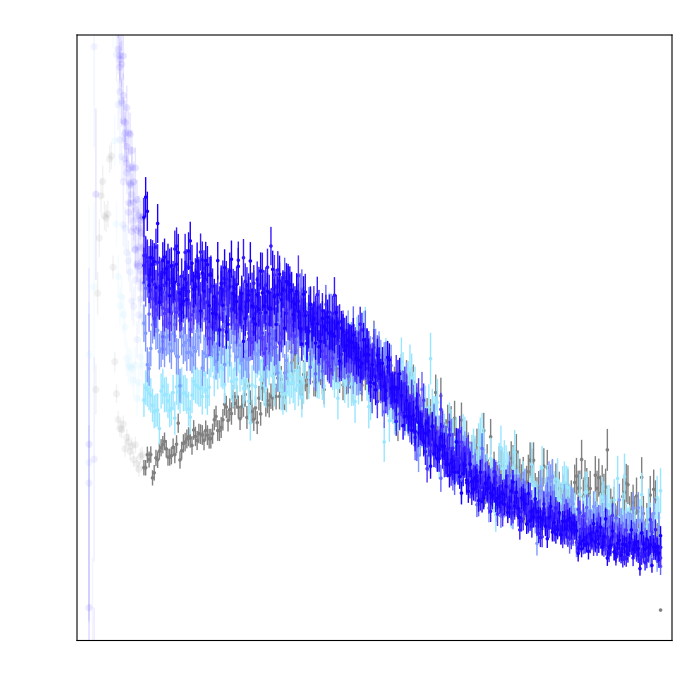
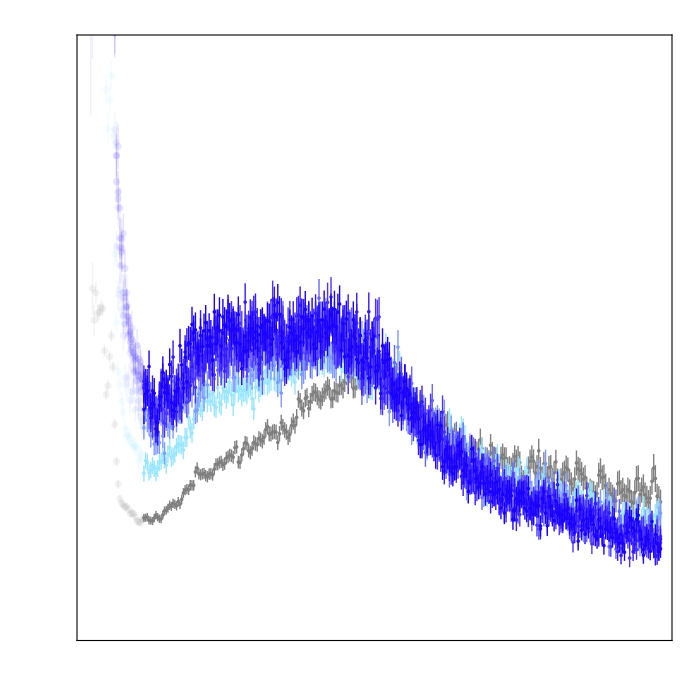
-Graphics- |  | -Graphics- | -Graphics-
-Graphics- |  | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
figurea=Import["C:\\Users\\steph\\Desktop\\Debanjan\\VectorGraphics\\Fig1aInked.pdf"][[1]];
Grid[{{atext,SpanFromLeft,dtext,etext},{figurea,SpanFromLeft,figured,figuree},{btext,ctext,ftext,gtext},{figureb,figurec,OPplot,ODplot}},Spacings->{0,0}]
```

```mathematica
(*Supplemental material things: low-frequency data.*)
(*Optimally doped*)
linelegs[label_,legs_,pos_,cols_]:=PlotLegends->Placed[LineLegend[Table[Text[Style[legs[[i]],14,FontFamily->"Times New Roman"]],{i,1,Length[legs]}],LegendLabel->Text[Style[label,14,FontFamily->"Times New Roman"]],LabelStyle->{GrayLevel[0],14},LegendLayout->{"Column",cols}],pos]
frameStyle[xlabel_,ylabel_,fsize_:14]:={Axes->None,Frame->True,FrameStyle->Black,AspectRatio->1/GoldenRatio, FrameLabel->{{Text[Style[ylabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}, {Text[Style[xlabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}},LabelStyle->{FontFamily->"Times New Roman",fsize}}
text[x0_,y0_,txt_,color_]:=Graphics[Text[Style[txt,color,FontFamily->"Times New Roman",14],{x0,y0}]]
text[x0_,y0_,txt_,color_,size_:fontSize]:=Graphics[Text[Style[txt,color,FontFamily->"Times New Roman",size],{x0,y0}],Method->{"ShrinkWrap"->True}];
Cell[StyleData["Print"],FontSize->36];
frameStyle0[xlabel_,ylabel_,fsize_:14]:={Axes->None,Frame->False,AspectRatio->1/GoldenRatio, FrameLabel->{{Text[Style[ylabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}, {Text[Style[xlabel,FontFamily->"Times New Roman",fsize]], Text[Style["",fsize]]}},LabelStyle->{FontFamily->"Times New Roman",fsize}}

ResourceFunction["MaTeXInstall"][]
<<MaTeX`
c=8/9;
r=2;
z=3;
qD= √((8π)/(3 √3));
F1=((c(3+5r))/(z qD^2 r (1+r))-(c(1+5r))/(z qD^2 (1+r)(1+2r)));
u0=((((r qD^2)/c )^((c(3+5r))/(z qD^2 r (1+r))))/((((1+2r)qD^2)/c)^((c(1+5r))/(z qD^2 (1+r)(1+2r)))))^(-1/((c(3+5r))/(z qD^2 r (1+r))-(c(1+5r))/(z qD^2 (1+r)(1+2r))));
ut[dp_]:=u0*Abs[dp];
ktappx[ωt_?NumericQ,δp_?NumericQ]:=HeavisideTheta[δp]*(Re[1/(2(1-2/z))(1+√(1-4(1-2/z)F1*Abs[Log[Abs[δp]]] ωt^2))]-I*Abs[Im[1/(2(1-2/z))(1+√(1-4(1-2/z)F1*Abs[Log[Abs[δp]]] ωt^2))]])+HeavisideTheta[-δp]*(Re[1/(2(1-2/z))(-1+√(1-4(1-2/z)F1*Abs[Log[Abs[δp]]] ωt^2))]-I*Abs[Im[1/(2(1-2/z))(-1+√(1-4(1-2/z)F1*Abs[Log[Abs[δp]]] ωt^2))]])+1/1000-1/1000 I;
kt[ωt_?NumericQ,δp_?NumericQ]:=kt/.FindRoot[{Sign[δp]-(1-2/z)kt==F1 ωt^2/kt Log[-kt/(ut[δp] ωt^2)]},{kt,ktappx[ωt,δp],-2000-2000I,2000+0I},AccuracyGoal->18,WorkingPrecision->MachinePrecision];
Π[q_?NumericQ,ω_?NumericQ,δp_?NumericQ]:=(4 q^2)/(-2 ω^2+(1+2r)*c*Abs[δp]kt[ω/δp,δp]*q^2);
χ[q_?NumericQ,ω_?NumericQ,e_?NumericQ,δp_?NumericQ]:=Π[q,ω,δp]/(1+(4π e^2)/q^2(Π[q,ω,δp]));
ImχAvg[q_?NumericQ,ω_?NumericQ,e_?NumericQ,δpc_?NumericQ,σ_?NumericQ,nsig_:3]:=Sum[NIntegrate[Im[χ[q,ω,e,δp]]*1/(√(2π σ^2))Exp[-(δp-δpc)^2/(2 σ^2)],{δp,δpc+((i-1)/3-Ceiling[nsig])*σ,δpc+(i/3-Ceiling[nsig])*σ},Method->{"GlobalAdaptive","MaxErrorIncreases"->Infinity,Method->"GaussKronrodRule"},MaxRecursion->Infinity,AccuracyGoal->16,WorkingPrecision->MachinePrecision],{i,1,3*2*Ceiling[nsig]}];
qlist={0.02,0.05,0.1,1};
colors={Red,Gray,RGBColor[0,0.5,1],Blue};
colorstrans={RGBColor[1,0,0,0.6],RGBColor[0.5,0.5,0.5,0.6],RGBColor[0,0.5,1,0.6],RGBColor[0,0,1,0.6]};
stl[n_,thick_]:=Thread[{colors[[;;n]],AbsoluteThickness@thick}];
legend=LineLegend[Directive@@@stl[4,7],{MaTeX["q=0.02",Magnification->2.5],MaTeX["q=0.05",Magnification->2.5],MaTeX["q=0.1",Magnification->2.5],MaTeX["q=1.0",Magnification->2.5]},LegendFunction->Panel];
ticks={{{{0,MaTeX["",Magnification->3.5],{0.03,0}},{0.5,MaTeX["",Magnification->3.5],{0.03,0}},{0.85,Rotate[MaTeX["-\chi''/\chi''_{0}",Magnification->3.5],π/2],{0,0}},{1,Rotate[MaTeX["",Magnification->3.5],π/2],{0.03,0}},{1.5,MaTeX["",Magnification->3.5],{0.03,0}},{2,MaTeX["",Magnification->3.5],{0.03,0}},{3,MaTeX["3",Magnification->3.5],{0.03,0}},{4,MaTeX["4",Magnification->3.5],{0.03,0}}},None},{{{0*7.1/5.1,MaTeX["0",Magnification->3.5],{0.03,0}},{1*7.1/5.1,MaTeX["1",Magnification->3.5],{0.03,0}},{2*7.1/5.1,MaTeX["",Magnification->3.5],{0.03,0}},{2.5*7.1/5.1,MaTeX["\omega/\overline{\omega}_{\star}",Magnification->3.5],{0,0}},
{3*7.1/5.1,MaTeX["",Magnification->3.5],{0.03,0}},{4*7.1/5.1,MaTeX["4",Magnification->3.5],{0.03,0}},{5*7.1/5.1,MaTeX["5",Magnification->3.5],{0.03,0}}},None}};
```

OpenWrite::noopen: Cannot open C:\Users\steph\AppData\Roaming\Mathematica\Paclets\Repository\MaTeX-1.7.9\Documentation\English\TextSearchIndex\_0.cfs.

BinaryWrite::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

General::stop: Further output of BinaryWrite::stream will be suppressed during this calculation.

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Paclet[MaTeX,1.7.9,<>]

```mathematica
image1=Plot[ImχAvg[qlist[[1]],ωt*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170,{ωt,0.7,7.1},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,PlotStyle->{colors[[1]],Thickness[0.0085]}];
```

```mathematica
image2=Plot[ImχAvg[qlist[[2]],ωt*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170,{ωt,0.7,7.1},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,PlotStyle->{colors[[2]],Thickness[0.0085]}];
```

```mathematica
image3=Plot[ImχAvg[qlist[[3]],ωt*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170,{ωt,0.7,7.1},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,PlotStyle->{colors[[3]],Thickness[0.0085]}];
```

```mathematica
image4=Plot[ImχAvg[qlist[[4]],ωt*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170,{ωt,0.7,7.1},PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,PlotStyle->{colors[[4]],Thickness[0.0085]}];
```

```mathematica
ImχAvgBad[q_?NumericQ,ω_?NumericQ,e_?NumericQ,δpc_?NumericQ,σ_?NumericQ,nsig_:3]:=Sum[NIntegrate[Im[χ[q,ω,e,δp]]*1/(√(2π σ^2))Exp[-(δp-δpc)^2/(2 σ^2)],{δp,δpc+((i-1)/3-Ceiling[nsig])*σ,δpc+(i/3-Ceiling[nsig])*σ},Method->{"GlobalAdaptive","MaxErrorIncreases"->Infinity,Method->"GaussKronrodRule"},MaxRecursion->Infinity,AccuracyGoal->7,WorkingPrecision->9],{i,1,3*2*Ceiling[nsig]}];
```

```mathematica
image1points=ListPlot[Table[{i*0.01,ImχAvgBad[qlist[[1]],i*0.01*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170},{i,1,70}],PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,Joined->True,PlotStyle->{Directive[colorstrans[[1]],PointSize[0.0085],Thickness[0.0085]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
image2points=ListPlot[Table[{i*0.01,ImχAvgBad[qlist[[2]],i*0.01*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170},{i,1,70}],PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,Joined->True,PlotStyle->{Directive[colorstrans[[2]],PointSize[0.0085],Thickness[0.0085]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
image3points=ListPlot[Table[{i*0.01,ImχAvgBad[qlist[[3]],i*0.01*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170},{i,1,70}],PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,Joined->True,PlotStyle->{Directive[colorstrans[[3]],PointSize[0.0085],Thickness[0.0085]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
image4points=ListPlot[Table[{i*0.01,ImχAvgBad[qlist[[4]],i*0.01*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170},{i,1,70}],PlotRange->{{0,7.1},{0,1.85}},ImageSize->Large,Joined->True,PlotStyle->{Directive[colorstrans[[4]],PointSize[0.0085],Thickness[0.0085]]}];
```

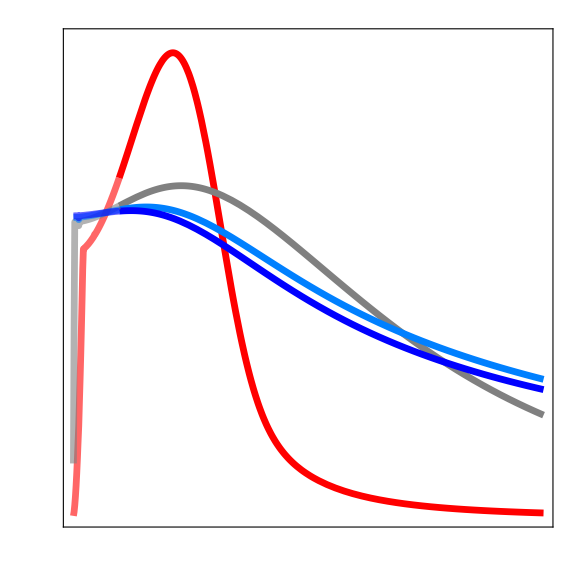

```mathematica
figuresupp=Show[Legended[{image1,image2,image3,image4,image1points,image2points,image3points,image4points},Placed[legend,{0.82,0.755}]],AspectRatio->1,frameStyle["","",50],ImageSize->Large,FrameTicks->ticks,FrameTicksStyle->{{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},{{Black,Thickness[0.005]},{Black,Thickness[0.005]}}},ImagePadding->{{60,15},{55,15}}]
```

```mathematica
image1log=LogLogPlot[ImχAvg[qlist[[1]],ωt*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170,{ωt,0.7,10^1},PlotRange->{{10^-5,10^1},{10^-1,10^1}},ImageSize->Large,PlotStyle->{colors[[1]],Thickness[0.0085]}];
```

```mathematica
image2log=LogLogPlot[ImχAvg[qlist[[2]],ωt*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170,{ωt,0.7,10^1},PlotRange->{{10^-5,10^1},{10^-1,10^1}},ImageSize->Large,PlotStyle->{colors[[2]],Thickness[0.0085]}];
```

```mathematica
image3log=LogLogPlot[ImχAvg[qlist[[3]],ωt*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170,{ωt,0.7,10^1},PlotRange->{{10^-5,10^1},{10^-1,10^1}},ImageSize->Large,PlotStyle->{colors[[3]],Thickness[0.0085]}];
```

```mathematica
image4log=LogLogPlot[ImχAvg[qlist[[4]],ωt*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170,{ωt,0.7,10^1},PlotRange->{{10^-5,10^1},{10^-1,10^1}},ImageSize->Large,PlotStyle->{colors[[4]],Thickness[0.0085]}];
```

```mathematica
image1pointslog=ListLogLogPlot[Table[{7*10^(-i/10),ImχAvgBad[qlist[[1]],7*10^(-i/10)*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170},{i,10,60}],PlotRange->{{10^-5,10^1},{10^-1,10^1}},ImageSize->Large,Joined->True,PlotStyle->{Directive[colorstrans[[1]],PointSize[0.0085],Thickness[0.0085]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
image2pointslog=ListLogLogPlot[Table[{7*10^(-i/10),ImχAvgBad[qlist[[2]],7*10^(-i/10)*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170},{i,10,60}],PlotRange->{{10^-5,10^1},{10^-1,10^1}},ImageSize->Large,Joined->True,PlotStyle->{Directive[colorstrans[[2]],PointSize[0.0085],Thickness[0.0085]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
image3pointslog=ListLogLogPlot[Table[{7*10^(-i/10),ImχAvgBad[qlist[[3]],7*10^(-i/10)*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170},{i,10,60}],PlotRange->{{10^-5,10^1},{10^-1,10^1}},ImageSize->Large,Joined->True,PlotStyle->{Directive[colorstrans[[3]],PointSize[0.0085],Thickness[0.0085]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
image4pointslog=ListLogLogPlot[Table[{7*10^(-i/10),ImχAvgBad[qlist[[4]],7*10^(-i/10)*10^-3,10^-4,1.1*10^-3,0.9*10^-3,3.5]/170},{i,10,60}],PlotRange->{{10^-5,10^1},{10^-1,10^1}},ImageSize->Large,Joined->True,PlotStyle->{Directive[colorstrans[[4]],PointSize[0.0085],Thickness[0.0085]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

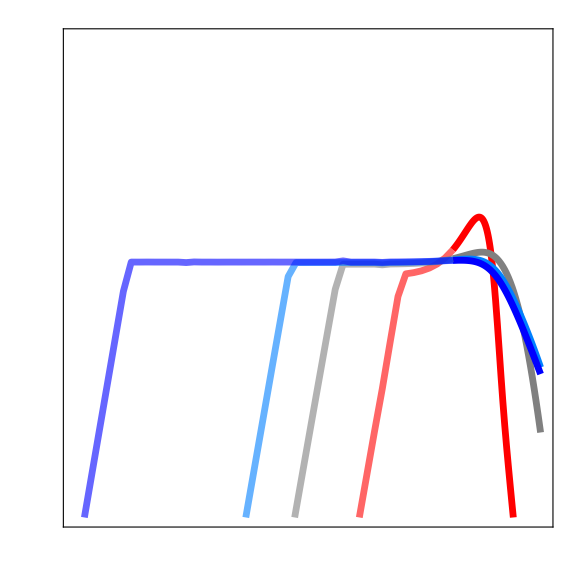

```mathematica
tickslog={{{{0,Rotate[MaTeX["-\chi''/\chi''_{0}",Magnification->3.5],π/2],{0.03,0}},{1*Log[10],MaTeX["",Magnification->3.5],{0.03,0}},{-3*Log[10],Rotate[MaTeX["",Magnification->3.5],π/2],{0.03,0}},{-2*Log[10],Rotate[MaTeX["",Magnification->3.5],π/2],{0.03,0}},
{-0.5*Log[10],Rotate[MaTeX["",Magnification->3.5],π/2],{0,0}},
{-1*Log[10],MaTeX["",Magnification->3.5],{0.03,0}},{-4*Log[10],MaTeX["",Magnification->3.5],{0.03,0}}},None},{{{0,MaTeX["10^0",Magnification->3.5],{0.03,0}},{1*Log[10],MaTeX["",Magnification->3.5],{0.03,0}},{2*Log[10]/Log[E],MaTeX["",Magnification->3.5],{0.03,0}},{-1*Log[10],MaTeX["",Magnification->3.5],{0.03,0}},{-1.5*Log[10],MaTeX["",Magnification->3.5],{0,0}},{-2*Log[10],MaTeX["\omega/\overline{\omega}_{\star}",Magnification->3.5],{0.03,0}},
{-3*Log[10],MaTeX["",Magnification->3.5],{0.03,0}},{-4*Log[10]/Log[E],MaTeX["10^{-4}",Magnification->3.5],{0.03,0}},{-5*Log[10]/Log[E],MaTeX["",Magnification->3.5],{0.03,0}}},None}};
figuresupplog=Show[Legended[{image1log,image2log,image3log,image4log,image1pointslog,image2pointslog,image3pointslog,image4pointslog},Placed[legend,{0.3,0.76}]],AspectRatio->1,frameStyle["","",50],ImageSize->Large,FrameTicks->tickslog,FrameTicksStyle->{{{Black,Thickness[0.005]},{Black,Thickness[0.005]}},{{Black,Thickness[0.005]},{Black,Thickness[0.005]}}},ImagePadding->{{90,15},{55,15}}]
```